```mathematica
(*Solution of the Hamilton equations in dimensionless form as a function of sbB and the shooting variables:*)
s0B=0;
SolveShapeEqs[sbB_,pψfBi_,prfBi_]:=NDSolve[
{ψfB'[sB]==1/(2 rfB[sB]) (pψfB[sB]-2 Sin[ψfB[sB]]),rfB'[sB]==Cos[ψfB[sB]],hfB'[sB]==Sin[ψfB[sB]],pψfB'[sB]==(pψfB[sB]/rfB[sB]- phfB[sB]) Cos[ψfB[sB]]+((2 rfB[sB])/λB^2+prfB[sB]) Sin[ψfB[sB]],prfB'[sB]==pψfB[sB]/(4 rfB[sB]^2)(pψfB[sB]-4 Sin[ψfB[sB]])+2/λB^2 (1-Cos[ψfB[sB]]),phfB'[sB]==0,
(*Initial conditions:*)
ψfB[s0B]==αB,(*0,*)
rfB[s0B]==RdomeB Sin[αB],(*Sqrt[Scap/π]/Lc,*)
hfB[s0B]==RdomeB*(1-Cos[αB]),(*0,*)
pψfB[s0B]==pψfBi,
prfB[s0B]==prfBi,
phfB[s0B]==0
},{ψfB,rfB,hfB,pψfB,prfB,phfB},{sB,s0B,sbB},Method->"ImplicitRungeKutta"];
```

```mathematica
(*Solve the Hamilton equations in dimensionless form as a function of the shooting variables, and output the boundary values of ψfB[sB] and prfB[sB] at s = sbB (these are the boundary values used to satisfy the boundary conditions at s = sbB):*)
shoot[sbB_?NumberQ,pψfBi_?NumberQ,prfBi_?NumberQ]:=First[{ψfB[sbB],prfB[sbB]}/.SolveShapeEqs[sbB,pψfBi,prfBi]];
(*Use here ?NumberQ to indicate that sbB, pψfB0, and prfB0 are numbers; This is needed for the FindRoot[] comand (see below) to work with shoot[].*)
```

```mathematica
(*Solution of the Hamilton equations in dimensionless form as a function of sbB and the shooting variables (for a fixed radial distance):*)
s0B=0;
(*CLOSED*)
SolveShapeEqs[sbB_,pψfBi_]:=NDSolve[
{ψfB'[sB]==1/(2 rfB[sB]) (pψfB[sB]-2 Sin[ψfB[sB]]),rfB'[sB]==Cos[ψfB[sB]],hfB'[sB]==Sin[ψfB[sB]],pψfB'[sB]==(pψfB[sB]/rfB[sB]- phfB[sB]) Cos[ψfB[sB]]+((2 rfB[sB])/λB^2+prfB[sB]) Sin[ψfB[sB]],prfB'[sB]==pψfB[sB]/(4 rfB[sB]^2)(pψfB[sB]-4 Sin[ψfB[sB]])+2/λB^2 (1-Cos[ψfB[sB]]),phfB'[sB]==0,
(*Initial conditions:*)
ψfB[s0B]==αB,(*0,*)
rfB[s0B]==RdomeB Sin[αB],(*Sqrt[Scap/π]/Lc,*)
hfB[s0B]==RdomeB*(1-Cos[αB]),(*0,*)
pψfB[s0B]==pψfBi,
prfB[s0B]==pψfBi/Cos[αB](-pψfBi/(4*RdomeB*Sin[αB])+1/RdomeB)+(2*RdomeB*Tan[αB])/λB^2(1-Cos[αB]),
phfB[s0B]==0
},{ψfB,rfB,hfB,pψfB,prfB,phfB},{sB,s0B,sbB},Method->"ImplicitRungeKutta"];
(*OPEN*)
(*SolveShapeEqs[sbB_,pψfBi_]:=NDSolve[
{ψfB'[sB]==1/(2 rfB[sB]) (pψfB[sB]-2 Sin[ψfB[sB]]),rfB'[sB]==Cos[ψfB[sB]],hfB'[sB]==Sin[ψfB[sB]],pψfB'[sB]==(pψfB[sB]/rfB[sB]- phfB[sB]) Cos[ψfB[sB]]+((2 rfB[sB])/λB^2+prfB[sB]) Sin[ψfB[sB]],prfB'[sB]==pψfB[sB]/(4 rfB[sB]^2)(pψfB[sB]-4 Sin[ψfB[sB]])+2/λB^2 (1-Cos[ψfB[sB]]),phfB'[sB]==0,
(*Initial conditions:*)
ψfB[s0B]==(*αB,*)0,
rfB[s0B]==(*RdomeB Sin[αB],*)Sqrt[Ap/π]/Lc,
hfB[s0B]==(*RdomeB*(1-Cos[αB]),*)0,
pψfB[s0B]==pψfBi,
prfB[s0B]==-pψfBi^2/(4Sqrt[Ap/π]/Lc),
phfB[s0B]==0
},{ψfB,rfB,hfB,pψfB,prfB,phfB},{sB,s0B,sbB},Method->"ImplicitRungeKutta"];*)
(*Solve the Hamilton equations in dimensionless form as a function of the shooting variables, and output the boundary values of ψfB[sB] and rfB[sB] at s = sbB (these are the boundary values used to satisfy the boundary conditions at s = sbB):*)
shoot[sbB_?NumberQ,pψfBi_?NumberQ]:=First[{ψfB[sbB],rfB[sbB]}/.SolveShapeEqs[sbB,pψfBi]];
```

#### Hamilton equations in zero tension limit

```mathematica
s0B=0;
SolveShapeEqs[sbB_,pψfBi_,prfBi_]:=NDSolve[
{ψfB'[sB]==1/(2 rfB[sB]) (pψfB[sB]-2 Sin[ψfB[sB]]),rfB'[sB]==Cos[ψfB[sB]],hfB'[sB]==Sin[ψfB[sB]],pψfB'[sB]==(pψfB[sB]/rfB[sB]- phfB[sB]) Cos[ψfB[sB]]+prfB[sB]* Sin[ψfB[sB]],prfB'[sB]==pψfB[sB]/(4 rfB[sB]^2)(pψfB[sB]-4 Sin[ψfB[sB]]),phfB'[sB]==0,
(*Initial conditions:*)
ψfB[s0B]==αB,(*0,*)
rfB[s0B]==RdomeB Sin[αB],(*Sqrt[Scap/π]/Lc,*)
hfB[s0B]==RdomeB*(1-Cos[αB]),(*0,*)
pψfB[s0B]==pψfBi,
prfB[s0B]==prfBi,
phfB[s0B]==0
},{ψfB,rfB,hfB,pψfB,prfB,phfB},{sB,s0B,sbB}];
(*Solve the Hamilton equations in dimensionless form as a function of the shooting variables, and output the boundary values of ψfB[sB] and prfB[sB] at s = sbB (these are the boundary values used to satisfy the boundary conditions at s = sbB):*)
shoot[sbB_?NumberQ,pψfBi_?NumberQ,prfBi_?NumberQ]:=First[{ψfB[sbB],prfB[sbB]}/.SolveShapeEqs[sbB,pψfBi,prfBi]];
(*Use here ?NumberQ to indicate that sbB, pψfB0, and prfB0 are numbers; This is needed for the FindRoot[] comand (see below) to work with shoot[].*)
```

#### Deformation profile for catenoid

```mathematica
(*NOTE FOR GENERATING THE CATENOIDAL CURVE IN THE LOW (BUT NON-ZERO) TENSION LIMIT:
For Subscript[R, p]=Subscript[R, 0], Subscript[S, cap]=450 nm^2, Subscript[K, b]=20 Subscript[k, B] T, Subscript[s, b]=20nm, Lc=Subscript[R, p] sin(α), we used the shooting parameters prfBs=-0.011193022142760635*Lc/Sqrt[Kb/0.0001] and pψfBs=-0.18187701329999983-1.5*)
```

Precision::precsm: Requested precision -1.5 is smaller than $MinPrecision. Using $MinPrecision instead.

FindRoot::jsing: Encountered a singular Jacobian at the point {pψfBi,prfBi} = {0.,-0.000296464}. Try perturbing the initial point(s).

Gm=2.78909×10^-6k_BT

β=0.106576{0.106705,-0.000285519}

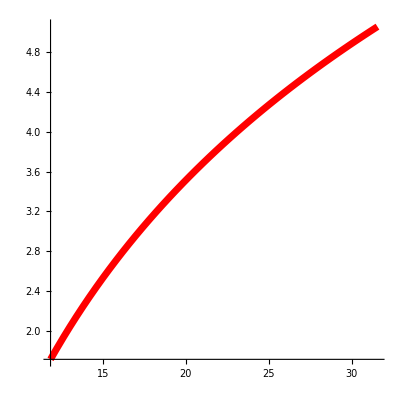

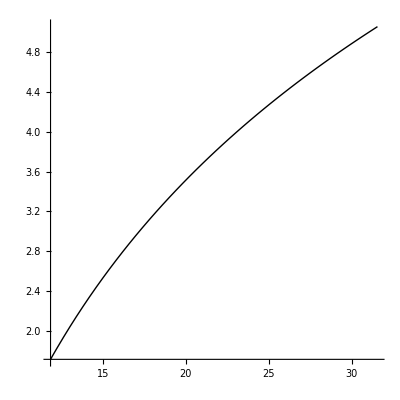

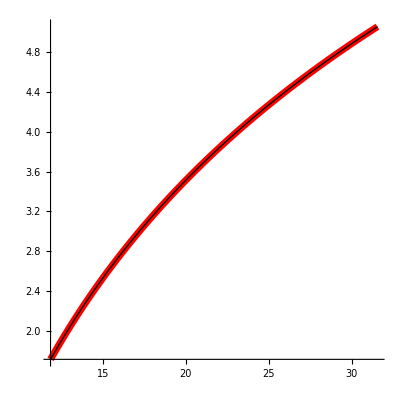

sb20_r_h_psi_gamma0.0001_LcCirc_RpR0_betaCatenoid.csv

```mathematica
Rdome=41.82077878168754;
Scap=450;
αB=ArcCos[1-Scap/(2 π*Rdome^2)];
Kb=20;
Lc=Rdome*Sin[αB];
sb=20;
sMax=sb/Lc;
γ=0.0001;
RdomeB=Rdome/Lc;
λ=Sqrt[Kb/γ];
λB=λ/Lc;
(*Shooting Parameters*)
(*Rdome=42nm, γ=1*^-4 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[α], sb=20nm, β=0^o*)
(*prfBs=-0.011193022142760635*Lc/Sqrt[Kb/0.0001];*)
(*pψfBs=-0.18187701329999983;*)
prfBs=-0.011193022142760635*Lc/Sqrt[Kb/0.0001];
pψfBs=-0.18187701329999983`-1.5;
(*γ=1e-4,sb=10nm,Lc=λ*)
(*prfBs=-3.3611638633404466*Lc/Sqrt[Kb/0.0001];
pψfBs=-0.47482543696004587;*)
β=ArcTan[RdomeB*Sin[αB]*Sin[αB]/(sMax+RdomeB*Sin[αB]*Cos[αB])];
sols=FindRoot[shoot[sMax,pψfBi,prfBi]={β,0},{pψfBi,pψfBs},{prfBi,prfBs}];

prfBs0=prfBi/.sols;
pψfBs0=pψfBi/.sols;

sSamples=Subdivide[0,sMax,9999];

ndsol=SolveShapeEqs[sMax,pψfBs0,prfBs0];
hff[s_]:=First[hfB[s]/.ndsol];
rff[s_]:=First[rfB[s]/.ndsol];
ψff[s_]:=First[ψfB[s]/.ndsol];
data=Table[{s,rff[s],hff[s],ψff[s]},{s,sSamples}];
en=Kb π rff[s]((D[ψff[s],s]+Sin[ψff[s]]/rff[s])^2); 
Gm=NIntegrate[en,{s,0,sMax}];
Print["Gm=",Gm,"k_BT"];
dummy = Evaluate[shoot[sMax,pψfBs0,prfBs0]];
Print["β=",β,dummy];
Clear[prfBi];
Clear[pψfBi];
Plot1=ParametricPlot[{rff[s]*Lc,hff[s]*Lc},{s,0,sMax},PlotRange->Full,PlotStyle->Directive[Red,AbsoluteThickness[5]],AspectRatio->1]
h0=Rdome*(1-Cos[αB]);
r0=Rdome*Sin[αB];
Ccat=r0*Sin[αB];
H=h0-Ccat*ArcSinh[Cot[αB]];
rcat[s_]:=Ccat*Sqrt[1+(s/Ccat+Cot[αB])^2];
hcat[s_]:=H+Ccat*ArcSinh[s/Ccat+Cot[αB]];
Plot2=ParametricPlot[{rcat[s],hcat[s]},{s,0,sb},PlotRange->Full,PlotStyle->Directive[Black,AbsoluteThickness[1]],AspectRatio->1]
Show[Plot1,Plot2]
Export["sb20_r_h_psi_gamma0.0001_LcCirc_RpR0_betaCatenoid.csv",data]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName[data]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName[data]]]
```

#### Sweep over rb and calculate footprint energy of hypothetical Piezo-membrane system

```mathematica
Ap=450;
Kb=20;
γ=0.0001;
Rdome=41.82077878168754;
αB=ArcCos[1-Ap/(2π*Rdome^2)];
Lc=Rdome*Sin[αB];
λ=Sqrt[Kb/γ];
λB=λ/Lc;
RdomeB=Rdome/Lc;
Hdimple=0.24; (*micron^-1*)
Hrim=-0.52; (*micron^-1*)
pψfBs=-0.175012;(*Rdome=42nm, γ=0.0001 Subscript[k, B] T/nm^2, β = Subscript[β, dimple] = 0.00072 rad, rb=32nm, Lc=Rdome*Sin[αB]*)
sMaxs=20.3405(*nm*)/Lc;
rb=30;

Timing[data0=Reap[For[rb=30,rb<=50,rb=rb+0.1,
rbB=rb/Lc;
β=N[ArcSin[Hrim*0.001*rb]];
sols=FindRoot[shoot[sbB,pψfBi]=={β,rbB},{sbB,sMaxs},{pψfBi,pψfBs}];

(*Use the values of the shooting variables determined in one interation as initial guesses for next iteration:*)
pψfBs=pψfBi/.sols;
sMaxs=sbB/.sols;

dummy=Evaluate[shoot[sMaxs,pψfBs]]; Print[γ," ", N[dummy[[1]]*180/π]," ", dummy[[2]]*Lc];
(*To check that we indeed have ψfB[sB] = 0 and prfB[sB] = 0 at s = sbB*)

(*Assemble solution using the correct values of the shooting variables:*)
ndsol=SolveShapeEqs[sMaxs,pψfBs];

(*Calculate footprint energy in units of Subscript[k, B] T:*)
ψff[s_]=First[ψfB[s]/.ndsol];
rff[s_]=First[rfB[s]/.ndsol];
en=Kb π rff[s]((D[ψff[s],s]+Sin[ψff[s]]/rff[s])^2+2/λB^2(1-Cos[ψff[s]]));
G=NIntegrate[en,{s,s0B,sMaxs}];
Sow[{rb,G}] (*Export data*);
(*Print[γ];*)
]];]
data=data0[[2]][[1]];
```

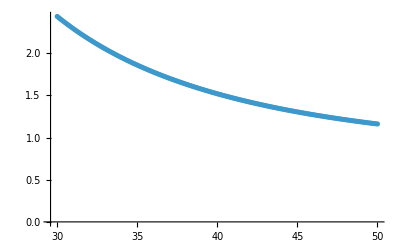

```mathematica
ListPlot[data]
```

```mathematica
Export["rb_vs_Gm_rim_gamma0p0001_RpR0.csv",data]
```

rb_vs_Gm_rim_gamma0p0001_RpR0.csv

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["rb_vs_Gm_rim_gamma0p0001_RpR0.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["rb_vs_Gm_dimple_gamma0p0001_RpR0.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["rb_vs_Gm_dimple_gamma0p0001_RpR0.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["rb_vs_Gm_rim_gamma0p0001_RpR0.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["rb_vs_Gm_rim_gamma0p0001_RpR0.csv"]]]
```

#### Single Deformation Profile

sbsolved = 18.3289

pψfBisolved = -0.20239

Checking hfB at s=0: 0.144578

Expected hfB at s=0: 0.144578

Checking psiB at s=0: 0.287166

Expected psiB at s=0: 0.287166

psif[sb] = 0.00072 rb = 30.

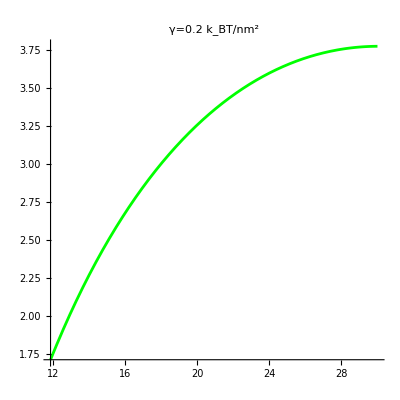

rb30_r_h_psi_gamma0.2_LcCirc_Rpflat_beta-5deg.csv

```mathematica
Ap=450;
Kb=20;
γ=0.0001;
Rdome=41.82077878168754;
αB=ArcCos[1-Ap/(2π*Rdome^2)];
Lc=Rdome*Sin[αB];
λ=Sqrt[Kb/γ];
λB=λ/Lc;
RdomeB=Rdome/Lc;
rb=30;
β=N[ArcSin[Hdimple*0.0001*rb]];
(*Rdome=42nm, γ=0.5 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[α], sb=20nm*)
pψfBs=-0.2023901635283968;(*Rdome=42nm, γ=0.0001 Subscript[k, B] T/nm^2, β=0, rb=30nm, Lc=Rdome*Sin[αB]*)
sMaxs=18.328879463744403(*nm*)/Lc;
sols=FindRoot[shoot[sbB,pψfBi]=={β,30/Lc},{sbB,sMaxs},{pψfBi,pψfBs}];

sbBsolved = sbB /.sols;
pψfBs0=pψfBi/.sols;
Print["sbsolved = ",sbBsolved*Lc];
Print["pψfBisolved = ",pψfBs0];

sSamples=Subdivide[0,sbBsolved,9999];

ndsol=SolveShapeEqs[sbBsolved,pψfBs0];
hff[s_]:=First[hfB[s]/.ndsol];
rff[s_]:=First[rfB[s]/.ndsol];
ψff[s_]:=First[ψfB[s]/.ndsol];
data=Table[{s,rff[s],hff[s],ψff[s]},{s,sSamples}];

Print["Checking hfB at s=0: ",hff[s0B]];
Print["Expected hfB at s=0: ",RdomeB*(1-Cos[αB])];
Print["Checking psiB at s=0: ",ψff[s0B]];
Print["Expected psiB at s=0: ",αB];
dummy=Evaluate[shoot[sbBsolved,pψfBs0]];
Print["psif[sb] = ",dummy[[1]]," rb = ",dummy[[2]]*Lc];

p1=ParametricPlot[{rff[s]*Lc,hff[s]*Lc},{s,0,sbBsolved},PlotRange->Full,AspectRatio->1,PlotStyle->Green,PlotLabel->"γ=0.2 k_BT/nm^2"]
Export["rb30_r_h_psi_gamma0.2_LcCirc_Rpflat_beta-5deg.csv",data]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["rb30_r_h_psi_gamma0.2_LcCirc_Rpflat_beta-5deg.csv"]]]
```

psif[sb] = -5. rb = 30. β = -5.deg.

#### Deformation profiles

sbsolved = 42.9033

pψfBisolved = -1.2879

Checking hfB at s=0: 0.144578

Expected hfB at s=0: 0.144578

Checking psiB at s=0: 0.287166

Expected psiB at s=0: 0.287166

psif[sb] = -1.5708 rb = 52. β = 0.deg.

Gamma = 0.5

sbsolved = 44.0512

pψfBisolved = -0.880219

Gamma = 0.0001

sbsolved = 66.2324

pψfBisolved = -1.06897

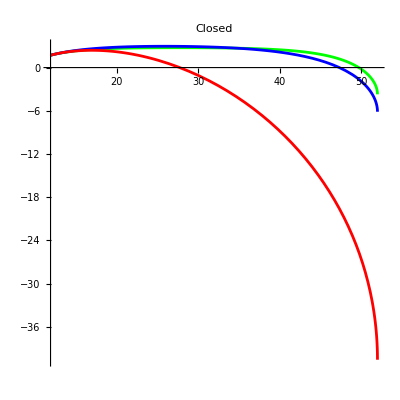

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

sbsolved = 42.704

pψfBisolved = -0.00241854

Checking hfB at s=0: 0.

Expected hfB at s=0: 0.144578

Checking psiB at s=0: -2.11758×10^-22

Expected psiB at s=0: 0.287166

psif[sb] = -1.5708 rb = 52. β = 0.deg.

Gamma = 0.5

sbsolved = 43.8377

pψfBisolved = -0.022815

Gamma = 0.0001

sbsolved = 67.6991

pψfBisolved = -1.01969

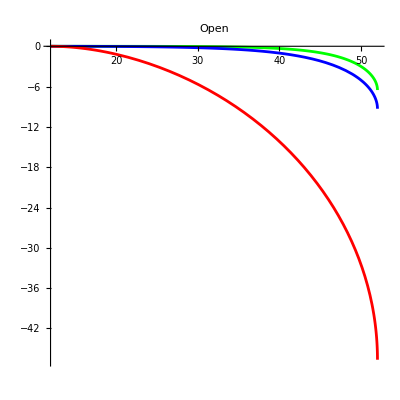

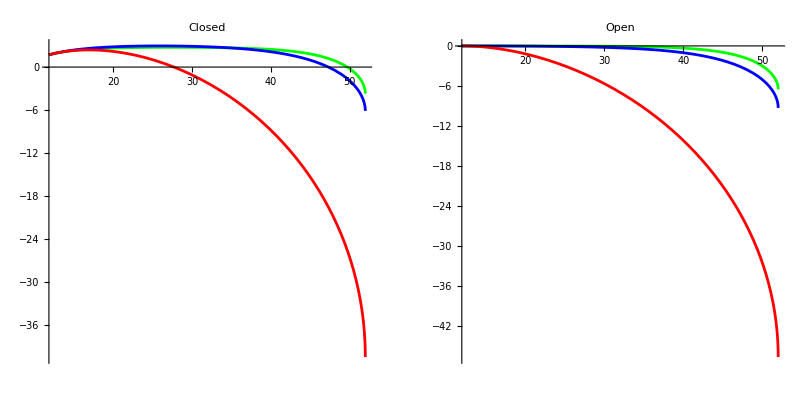

```mathematica
Rdome=41.82077878168754;
Ap=450;
αB=ArcCos[1-Ap/(2 π*Rdome^2)];
Kb=20;
γ=1;
Lc=Rdome*Sin[αB];
(*sMax=40/Lc;*)
λ=Sqrt[Kb/γ];
λB=λ/Lc;
RdomeB=Rdome/Lc;
β=-N[π/2];(*Subscript[β, min]*)
(*---Old guesses (commented properly,no nesting)---prfBs=-0.12212504367809182;(*For Rdome=42nm,Gamma=0.5,Lc=Lambda,Kb=20,Scap=450,sb=5nm*)pψfBs=-1.3863582387063256;*)

(*Piezo dome curve*)
(*p1=ParametricPlot[{Rdome*Sin[θ],Rdome*(1-Cos[θ])},{θ,0,αB},PlotStyle->Directive[Gray,AbsoluteThickness[4]],Ticks->None,PlotRange->Full,Axes->False,AspectRatio->1];*)

(*Updated shooting parameters for this run*)
(*Rdome=42nm,γ=0.5,Lc=λ,Kb=20,Scap=450,sb=5nm*)
(*prfBs=-0.12212504367809182*Lc/Sqrt[Kb/0.5];
pψfBs=-1.3863582387063256;*)
(*(*For Rdome = 42 nm, γ = 0.0001, Lc = λ, sb = 5nm/Lc, ψfB[sb]=0*)
prfBs=-3.3611638633404466*Lc/Sqrt[Kb/0.0001];
pψfBs=0;*)
(*(*Rdome=42nm, γ=0.5 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[α], sb=20nm*)
prfBs=-0.042722133935570485;
pψfBs=-0.862220153582393;*)
(*Rdome=41.82077878168754 nm, γ=0.5, Lc=λ, Kb=20, Scap=450, sb=10 nm, β=0*)
(*(*Rdome=42nm, γ=0.5 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[α], sb=40nm*)
prfBs=-0.04255780280600476;
pψfBs=-0.8589721478725089;*)
(*(*Rdome=42nm, γ=1 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[α], sb=40nm*)
prfBs=-0.06145416264381031;
pψfBs=-1.2856797874440211;*)
(*(*Rdome=42nm, γ=1*^-4 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[α], sb=40nm*)
prfBs=-0.004281797587261707;
pψfBs=-0.06201089738701742;*)
(*prfBs=-68.35010304211565;(*Rdome=42nm, γ=0.5 Subscript[k, B] T/nm^2, β=-90^o, sb=40nm, Lc=Rdome*Sin[αB] FAILED*)
pψfBs=-16.383519164439758;*)
(*prfBs=-0.04255780280600476;(*Rdome=42nm, γ=0.5 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[α], sb=40nm*)
pψfBs=-0.8589721478725089;*)
(*pψfBs=-3.802839410388579;(*Rdome=42nm, γ=0.5 Subscript[k, B] T/nm^2, β=-π/2, rb=20nm, Lc=Rdome*Sin[α]*)
sMaxs=11.261529405695308(*nm*);*)
(*pψfBs=-3.4630539821311377;(*Rdome=42nm, γ=1 Subscript[k, B] T/nm^2, β=-π/2, rb=20nm, Lc=Rdome*Sin[α]*)
sMaxs=10.580821963364368(*nm*)/Lc;*)
(*pψfBs=-4.74441648434265(*Rdome=42nm, γ=0.0001 Subscript[k, B] T/nm^2, β=-π/2, rb=20nm*);
sMaxs=14.5621/Lc (*nm*)*)
(*pψfBs=-1.06897(*Rdome=42nm, γ=0.0001 Subscript[k, B] T/nm^2, β=-π/2, rb=52nm*);
sMaxs=66.2324(*nm*)/Lc;*)
(*pψfBs=-0.8803091959539351;(*Rdome=42nm, γ= 0.5 Subscript[k, B] T/nm^2, β=-π/2, rb=52nm, Lc=Rdome*Sin[α]*)
sMaxs=44.0508056423154(*nm*)/Lc;*)
(*pψfBs=-1.2879047049924437;(*Rdome=42nm, γ = 1 Subscript[k, B] T/nm^2, β=-π/2, rb=52nm, Lc=Rdome*Sin[α]*)
sMaxs=42.90325225854652(*nm*)/Lc;*)
(*pψfBs=-2.04418(*Rdome=42nm, γ=0.0001 Subscript[k, B] T/nm^2, β=-π/2, rb=32nm*);
sMaxs=34.3149(*nm*)/Lc;*)
(*pψfBs=-3.86798(*Rdome=42nm, γ=0.0001 Subscript[k, B] T/nm^2, β=-π/2, rb=22nm*);
sMaxs=17.9244(*nm*)/Lc;*)
(*pψfBs=-2.9058153790279;(*Rdome=42nm, γ = 0.5 Subscript[k, B] T/nm^2, β=-π/2, rb=22nm, Lc=Rdome*Sin[αB]*)
sMaxs=13.491616317415508(*nm*)/Lc;*)
(*pψfBs=-7.28892(*Rdome=42nm, γ=0.0001 Subscript[k, B] T/nm^2, β=-π/2, rb=17nm, Lc=Rdome*Sin[αB]*);
sMaxs=9.41781(*nm*)/Lc;*)
(*pψfBs=-6.464252794594437;(*Rdome=42nm, γ = 0.5 Subscript[k, B] T/nm^2, β=-π/2, rb=17nm, Lc=Rdome*Sin[αB]*)
sMaxs=7.70125505983806(*nm*)/Lc;*)
(*pψfBs=-6.036734962959053;(*Rdome=42nm, γ = 1 Subscript[k, B] T/nm^2, β=-π/2, rb=17nm, Lc=Rdome*Sin[αB]*)
sMaxs=7.246693499252439(*nm*)/Lc;*)
(*pψfBs=-1.01969(*Rdome=Open, γ=0.0001 Subscript[k, B] T/nm^2, β=-π/2, rb=52nm, Lc=Rdome*Sin[αB]*);
sMaxs=67.6991(*nm*)/Lc;*)
(*pψfBs=-0.022815(*Rdome=Open, γ=0.5 Subscript[k, B] T/nm^2, β=-π/2, rb=52nm, Lc=Rdome*Sin[αB]*);
sMaxs=43.8377(*nm*)/Lc;*)
(*pψfBs=-0.00241854(*Rdome=Open, γ=1 Subscript[k, B] T/nm^2, β=-π/2, rb=52nm, Lc=Rdome*Sin[αB]*);
sMaxs=42.704(*nm*)/Lc;*)
(*pψfBs=-1.89846(*Rdome=Open, γ=0.0001 Subscript[k, B] T/nm^2, β=-π/2, rb=32nm*);
sMaxs=35.48(*nm*)/Lc;*)
(*pψfBs=-0.437036(*Rdome=Open, γ=0.5 Subscript[k, B] T/nm^2, β=-π/2, rb=32nm*);
sMaxs=23.8507(*nm*)/Lc;*)
(*pψfBs=-0.168842(*Rdome=Open, γ=1 Subscript[k, B] T/nm^2, β=-π/2, rb=32nm*);
sMaxs=22.7294(*nm*)/Lc;*)
(*pψfBs=-3.51099(*Rdome=Open, γ=0.0001 Subscript[k, B] T/nm^2, β=-π/2, rb=22nm*);
sMaxs=18.7181(*nm*)/Lc;*)
(*pψfBs=-2.01175(*Rdome=Open, γ=0.5 Subscript[k, B] T/nm^2, β=-π/2, rb=22nm*);
sMaxs=13.5525(*nm*)/Lc;*)
(*pψfBs=-1.3898(*Rdome=Open, γ=1 Subscript[k, B] T/nm^2, β=-π/2, rb=22nm*);
sMaxs=12.6611(*nm*)/Lc;*)
(*pψfBs=-6.52877(*Rdome=Open, γ=0.0001 Subscript[k, B] T/nm^2, β=-π/2, rb=17nm, Lc=Rdome*Sin[αB]*);
sMaxs=9.88211(*nm*)/Lc;*)
(*pψfBs=-5.30618(*Rdome=Open, γ=0.5 Subscript[k, B] T/nm^2, β=-π/2, rb=17nm, Lc=Rdome*Sin[αB]*);
sMaxs=7.80851(*nm*)/Lc;*)
(*pψfBs=-4.5989(*Rdome=Open, γ=1 Subscript[k, B] T/nm^2, β=-π/2, rb=17nm, Lc=Rdome*Sin[αB]*);
sMaxs=7.28123(*nm*)/Lc;*)
(*pψfBs=-1.04855;(*Rdome=42nm, γ=0.0001 Subscript[k, B] T/nm^2, β=0, rb=17nm, Lc=Rdome*Sin[αB]*)
sMaxs=5.21915;*)
(*pψfBs=-0.451952;(*Rdome=42nm, γ=0.0001 Subscript[k, B] T/nm^2, β=0, rb=22nm, Lc=Rdome*Sin[αB]*)
sMaxs=10.2686(*nm*)/Lc;*)
(*pψfBs=-0.175012;(*Rdome=42nm, γ=0.0001 Subscript[k, B] T/nm^2, β=0, rb=32nm, Lc=Rdome*Sin[αB]*)
sMaxs=20.3405(*nm*)/Lc;*)
(*pψfBs=-0.060278;(*Rdome=42nm, γ=0.0001 Subscript[k, B] T/nm^2, β=0, rb=52nm, Lc=Rdome*Sin[αB]*)
sMaxs=40.425(*nm*)/Lc;*)
(*pψfBs=0.00442796;(*Rdome=42nm, γ=0.0001 Subscript[k, B] T/nm^2, β=4 deg, rb=52nm, Lc=Rdome*Sin[αB]*)
sMaxs=40.5427(*nm*)/Lc;*)
s0B=0;
(*CLOSED*)
SolveShapeEqs[sbB_,pψfBi_]:=NDSolve[
{ψfB'[sB]==1/(2 rfB[sB]) (pψfB[sB]-2 Sin[ψfB[sB]]),rfB'[sB]==Cos[ψfB[sB]],hfB'[sB]==Sin[ψfB[sB]],pψfB'[sB]==(pψfB[sB]/rfB[sB]- phfB[sB]) Cos[ψfB[sB]]+((2 rfB[sB])/λB^2+prfB[sB]) Sin[ψfB[sB]],prfB'[sB]==pψfB[sB]/(4 rfB[sB]^2)(pψfB[sB]-4 Sin[ψfB[sB]])+2/λB^2 (1-Cos[ψfB[sB]]),phfB'[sB]==0,
(*Initial conditions:*)
ψfB[s0B]==αB,(*0,*)
rfB[s0B]==RdomeB Sin[αB],(*Sqrt[Scap/π]/Lc,*)
hfB[s0B]==RdomeB*(1-Cos[αB]),(*0,*)
pψfB[s0B]==pψfBi,
prfB[s0B]==pψfBi/Cos[αB](-pψfBi/(4*RdomeB*Sin[αB])+1/RdomeB)+(2*RdomeB*Tan[αB])/λB^2(1-Cos[αB]),
phfB[s0B]==0
},{ψfB,rfB,hfB,pψfB,prfB,phfB},{sB,s0B,sbB},Method->"ImplicitRungeKutta"];
shoot[sbB_?NumberQ,pψfBi_?NumberQ]:=First[{ψfB[sbB],rfB[sbB]}/.SolveShapeEqs[sbB,pψfBi]];

pψfBs=-1.2879047049924437;(*Rdome=42nm, γ = 1 Subscript[k, B] T/nm^2, β=-π/2, rb=52nm, Lc=Rdome*Sin[α]*)
sMaxs=42.90325225854652(*nm*)/Lc;

(*sols=FindRoot[shoot[sMax,pψfBi,prfBi]=={β,0},{pψfBi,pψfBs},{prfBi,prfBs}];*)
sols=FindRoot[shoot[sbB,pψfBi]=={-N[π/2],52/Lc},{sbB,sMaxs},{pψfBi,pψfBs}];

sbBsolved = sbB /. sols;
pψfBs0=pψfBi/. sols;
Print["sbsolved = ",sbBsolved*Lc];
Print["pψfBisolved = ",pψfBs0];
(*sSamples=Subdivide[0,sMax,9999];*)

ndsol=SolveShapeEqs[sbBsolved,pψfBs0];

hPlot=hfB/. First[ndsol];
rPlot=rfB/. First[ndsol];
psiPlot=ψfB/. First[ndsol];
(*hff[s_]:=First[hfB[s]/. ndsol];
rff[s_]:=First[rfB[s]/. ndsol];
ψff[s_]:=First[ψfB[s]/. ndsol];*)


(*You can also explicitly check your ICs*)
Print["Checking hfB at s=0: ",hPlot[s0B]];
Print["Expected hfB at s=0: ",RdomeB*(1-Cos[αB])];
Print["Checking psiB at s=0: ",psiPlot[s0B]];
Print["Expected psiB at s=0: ",αB];
dummy=Evaluate[shoot[sbBsolved,pψfBs0]];
Print["psif[sb] = ",dummy[[1]]," rb = ",dummy[[2]]*Lc," β = ",N[β*180/π],"deg."];

p1=ParametricPlot[{rPlot[s]*Lc,hPlot[s]*Lc},{s,0,sbBsolved},PlotRange->Full,AspectRatio->1,PlotStyle->Green,PlotLabel->"γ=1 k_BT/nm^2"];
(*NEW*)

γ=0.5;
λ=Sqrt[Kb/γ];
λB=λ/Lc;
pψfBs=-0.8803091959539351;(*Rdome=42nm, γ= 0.5 Subscript[k, B] T/nm^2, β=-π/2, rb=52nm, Lc=Rdome*Sin[α]*)
sMaxs=44.0508056423154(*nm*)/Lc;

sols=FindRoot[shoot[sbB,pψfBi]=={-N[π/2],52/Lc},{sbB,sMaxs},{pψfBi,pψfBs}];

sbBsolved = sbB /. sols;
pψfBs0=pψfBi/. sols;
Print["Gamma = ",γ];
Print["sbsolved = ",sbBsolved*Lc];
Print["pψfBisolved = ",pψfBs0];
(*sSamples=Subdivide[0,sMax,9999];*)

ndsol=SolveShapeEqs[sbBsolved,pψfBs0];

hPlot=hfB/. First[ndsol];
rPlot=rfB/. First[ndsol];
psiPlot=ψfB/. First[ndsol];
p2=ParametricPlot[{rPlot[s]*Lc,hPlot[s]*Lc},{s,0,sbBsolved},PlotRange->Full,AspectRatio->1,PlotStyle->Blue,PlotLabel->"γ=0.5 k_BT/nm^2"];

γ=0.0001;
λ=Sqrt[Kb/γ];
λB=λ/Lc;
pψfBs=-1.06897(*Rdome=42nm, γ=0.0001 Subscript[k, B] T/nm^2, β=-π/2, rb=52nm*);
sMaxs=66.2324(*nm*)/Lc;

sols=FindRoot[shoot[sbB,pψfBi]=={-N[π/2],52/Lc},{sbB,sMaxs},{pψfBi,pψfBs}];

sbBsolved = sbB /. sols;
pψfBs0=pψfBi/. sols;
Print["Gamma = ",γ];
Print["sbsolved = ",sbBsolved*Lc];
Print["pψfBisolved = ",pψfBs0];
(*sSamples=Subdivide[0,sMax,9999];*)

ndsol=SolveShapeEqs[sbBsolved,pψfBs0];

hPlot=hfB/. First[ndsol];
rPlot=rfB/. First[ndsol];
psiPlot=ψfB/. First[ndsol];
p3=ParametricPlot[{rPlot[s]*Lc,hPlot[s]*Lc},{s,0,sbBsolved},PlotRange->Full,AspectRatio->1,PlotStyle->Red,PlotLabel->"γ=10^-4 k_BT/nm^2"];

p11=Show[p1,p2,p3,PlotRange->All,PlotLabel->"Closed"]

(*Open profiles*)
SolveShapeEqs[sbB_,pψfBi_]:=NDSolve[
{ψfB'[sB]==1/(2 rfB[sB]) (pψfB[sB]-2 Sin[ψfB[sB]]),rfB'[sB]==Cos[ψfB[sB]],hfB'[sB]==Sin[ψfB[sB]],pψfB'[sB]==(pψfB[sB]/rfB[sB]- phfB[sB]) Cos[ψfB[sB]]+((2 rfB[sB])/λB^2+prfB[sB]) Sin[ψfB[sB]],prfB'[sB]==pψfB[sB]/(4 rfB[sB]^2)(pψfB[sB]-4 Sin[ψfB[sB]])+2/λB^2 (1-Cos[ψfB[sB]]),phfB'[sB]==0,
(*Initial conditions:*)
ψfB[s0B]==(*αB,*)0,
rfB[s0B]==(*RdomeB Sin[αB],*)Sqrt[Ap/π]/Lc,
hfB[s0B]==(*RdomeB*(1-Cos[αB]),*)0,
pψfB[s0B]==pψfBi,
prfB[s0B]==-pψfBi^2/(4Sqrt[Ap/π]/Lc),
phfB[s0B]==0
},{ψfB,rfB,hfB,pψfB,prfB,phfB},{sB,s0B,sbB},Method->"ImplicitRungeKutta"];
shoot[sbB_?NumberQ,pψfBi_?NumberQ]:=First[{ψfB[sbB],rfB[sbB]}/.SolveShapeEqs[sbB,pψfBi]];

γ=1;
λ=Sqrt[Kb/γ];
λB=λ/Lc;
pψfBs=-0.00241854(*Rdome=Open, γ=1 Subscript[k, B] T/nm^2, β=-π/2, rb=52nm, Lc=Rdome*Sin[αB]*);
sMaxs=42.704(*nm*)/Lc;

(*sols=FindRoot[shoot[sMax,pψfBi,prfBi]=={β,0},{pψfBi,pψfBs},{prfBi,prfBs}];*)
sols=FindRoot[shoot[sbB,pψfBi]=={-N[π/2],52/Lc},{sbB,sMaxs},{pψfBi,pψfBs}];

sbBsolved = sbB /. sols;
pψfBs0=pψfBi/. sols;
Print["sbsolved = ",sbBsolved*Lc];
Print["pψfBisolved = ",pψfBs0];
(*sSamples=Subdivide[0,sMax,9999];*)

ndsol=SolveShapeEqs[sbBsolved,pψfBs0];

hPlot=hfB/. First[ndsol];
rPlot=rfB/. First[ndsol];
psiPlot=ψfB/. First[ndsol];
(*hff[s_]:=First[hfB[s]/. ndsol];
rff[s_]:=First[rfB[s]/. ndsol];
ψff[s_]:=First[ψfB[s]/. ndsol];*)


(*You can also explicitly check your ICs*)
Print["Checking hfB at s=0: ",hPlot[s0B]];
Print["Expected hfB at s=0: ",RdomeB*(1-Cos[αB])];
Print["Checking psiB at s=0: ",psiPlot[s0B]];
Print["Expected psiB at s=0: ",αB];
dummy=Evaluate[shoot[sbBsolved,pψfBs0]];
Print["psif[sb] = ",dummy[[1]]," rb = ",dummy[[2]]*Lc," β = ",N[β*180/π],"deg."];

p10=ParametricPlot[{rPlot[s]*Lc,hPlot[s]*Lc},{s,0,sbBsolved},PlotRange->Full,AspectRatio->1,PlotStyle->Green,PlotLabel->"γ=1 k_BT/nm^2"];
(*NEW*)

γ=0.5;
λ=Sqrt[Kb/γ];
λB=λ/Lc;
pψfBs=-0.022815(*Rdome=Open, γ=0.5 Subscript[k, B] T/nm^2, β=-π/2, rb=52nm, Lc=Rdome*Sin[αB]*);
sMaxs=43.8377(*nm*)/Lc;

sols=FindRoot[shoot[sbB,pψfBi]=={-N[π/2],52/Lc},{sbB,sMaxs},{pψfBi,pψfBs}];

sbBsolved = sbB /. sols;
pψfBs0=pψfBi/. sols;
Print["Gamma = ",γ];
Print["sbsolved = ",sbBsolved*Lc];
Print["pψfBisolved = ",pψfBs0];
(*sSamples=Subdivide[0,sMax,9999];*)

ndsol=SolveShapeEqs[sbBsolved,pψfBs0];

hPlot=hfB/. First[ndsol];
rPlot=rfB/. First[ndsol];
psiPlot=ψfB/. First[ndsol];
p20=ParametricPlot[{rPlot[s]*Lc,hPlot[s]*Lc},{s,0,sbBsolved},PlotRange->Full,AspectRatio->1,PlotStyle->Blue,PlotLabel->"γ=0.5 k_BT/nm^2"];

γ=0.0001;
λ=Sqrt[Kb/γ];
λB=λ/Lc;
pψfBs=-1.01969(*Rdome=Open, γ=0.0001 Subscript[k, B] T/nm^2, β=-π/2, rb=52nm, Lc=Rdome*Sin[αB]*);
sMaxs=67.6991(*nm*)/Lc;

sols=FindRoot[shoot[sbB,pψfBi]=={-N[π/2],52/Lc},{sbB,sMaxs},{pψfBi,pψfBs}];

sbBsolved = sbB /. sols;
pψfBs0=pψfBi/. sols;
Print["Gamma = ",γ];
Print["sbsolved = ",sbBsolved*Lc];
Print["pψfBisolved = ",pψfBs0];
(*sSamples=Subdivide[0,sMax,9999];*)

ndsol=SolveShapeEqs[sbBsolved,pψfBs0];

hPlot=hfB/. First[ndsol];
rPlot=rfB/. First[ndsol];
psiPlot=ψfB/. First[ndsol];
p30=ParametricPlot[{rPlot[s]*Lc,hPlot[s]*Lc},{s,0,sbBsolved},PlotRange->Full,AspectRatio->1,PlotStyle->Red,PlotLabel->"γ=10^-4 k_BT/nm^2"];

p12=Show[p10,p20,p30,PlotRange->All,PlotLabel->"Open"]

GraphicsRow[{p11,p12}]

(*ParametricPlot[{rPlot[s]*Lc,hPlot[s]*Lc},{s,0,sMax},PlotRange->Full,AspectRatio->1]*)
(*ParametricPlot[{rff[s]*Lc,hff[s]*Lc},{s,0,sMax},PlotRange->Full,AspectRatio->1]*)
(*data=Table[{s,rff[s],hff[s],ψff[s]},{s,sSamples}];*)
(*Export["sb40_r_h_psi_gamma0.5_LcCirc_RpR0_beta-90deg.csv",data]*)

(*pψfBs=-0.9(*nm, for Rdome=42nm, γ=0.5 Subscript[k, B] T/nm^2, β=-π/2, rb=47.5nm - Checked!!!*);
sMaxs=39.5496 (*nm*)*)
(*pψfBs=-0.986227(*nm, for Rdome=42nm, γ=0.5 Subscript[k, B] T/nm^2, β=-π/2, rb=40nm*);
sMaxs=32.0304 (*nm*)*)
(*pψfBs=-1.49493(*Rdome=42nm, γ=0.0001 Subscript[k, B] T/nm^2, β=-π/2, rb=40nm*);
sMaxs=47.1664 (*nm*);*)
(*pψfBs=-1.31(*Rdome=42nm, γ=1 Subscript[k, B] T/nm^2, β=-π/2, rb=40nm*);
sMaxs=30.9087 (*nm*);*)
(*pψfBs=-0.0312656(*Rdome=Open, γ=1 Subscript[k, B] T/nm^2, β=-π/2, rb=40nm*);
sMaxs=30.7179 (*nm*);*)
(*pψfBs=-0.135056(*Rdome=Open, γ=0.5 Subscript[k, B] T/nm^2, β=-π/2, rb=40nm*);
sMaxs=31.8581 (*nm*);*)
(*pψfBs=-1.4026(*Rdome=Open, γ=0.0001 Subscript[k, B] T/nm^2, β=-π/2, rb=40nm*);
sMaxs=48.4746 (*nm*);*)
```

```mathematica
Export["C:\\Users\\avish\\OneDrive\\Documents\\USC_PhD\\Spring 2025\\Piezo_Arclength_Data\\Datasets_for_paper_Topic1\\Po_vs_beta\\Deformations_OpenClosed_rb52nm_beta-90deg.pdf",%809,"PDF"]
```

C:\Users\avish\OneDrive\Documents\USC_PhD\Spring 2025\Piezo_Arclength_Data\Datasets_for_paper_Topic1\Po_vs_beta\Deformations_OpenClosed_rb52nm_beta-90deg.pdf

```mathematica
First[data]
```

{0.,1.0104,0.,0.}

```mathematica
Print["r_0^Closed = ",Rdome*Sin[αB]," nm"];
Print["r_0^Open = ",N[Sqrt[Ap/π]]," nm"];
```

r_0^Closed = 11.8451 nm

r_0^Open = 11.9683 nm

```mathematica
Export["sb40_r_h_psi_gamma1_LcCirc_Rpflat_beta-90deg.csv",data]
```

sb40_r_h_psi_gamma1_LcCirc_Rpflat_beta-90deg.csv

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["sb40_r_h_psi_gamma1_LcCirc_Rpflat_beta-90deg.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["sb40_r_h_psi_gamma0.5_LcCirc_Rpflat_beta-90deg.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["sb40_r_h_psi_gamma0.0001_LcCirc_Rpflat_beta-90deg.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["sb40_r_h_psi_gamma0.0001_LcCirc_RpR0_beta-90deg.csv"]]]
```

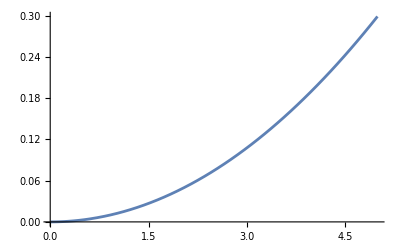

```mathematica
Show[%234,AspectRatio->1/GoldenRatio]
```

```mathematica
x=Subdivide[0,40,9];
Print[x]
```

{0,40/9,80/9,40/3,160/9,200/9,80/3,280/9,320/9,40}

```mathematica
Export["legend.pdf",BarLegend[{ColorData["RedBlueTones"],{0,1}},{{0,"Min"},{1,"Max"}}]]
```

legend.pdf

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["legend.pdf"]]]
```

```mathematica
Export["/Users/avishuma/Library/CloudStorage/OneDrive-Personal/Documents/USC_PhD/Spring 2025/Piezo_Arclength_Data/Datasets_for_paper_Topic1/Gm_behavior_vs_beta/Deformation_profiles/Plot_with_colorbar1.svg",%1921,"SVG"]
```

/Users/avishuma/Library/CloudStorage/OneDrive-Personal/Documents/USC_PhD/Spring 2025/Piezo_Arclength_Data/Datasets_for_paper_Topic1/Gm_behavior_vs_beta/Deformation_profiles/Plot_with_colorbar1.svg

16.7992

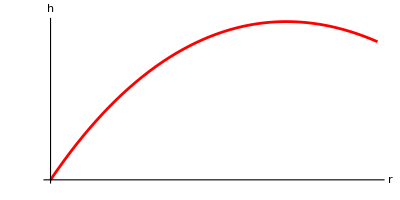

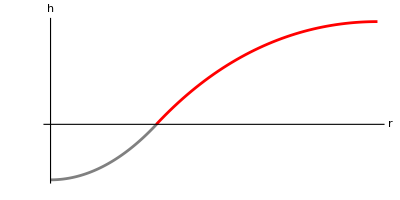

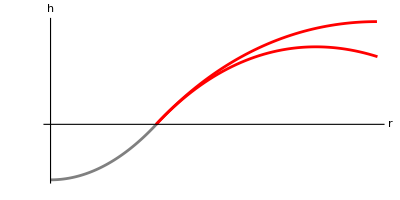

16.7641

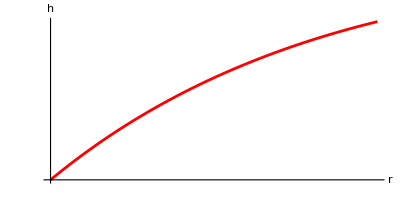

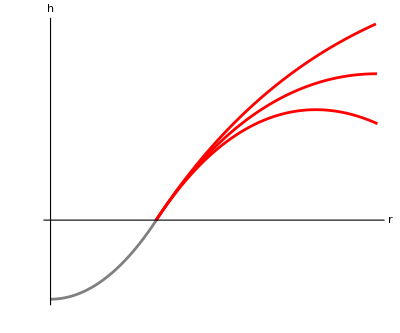

```mathematica
(*Negative*)
prfBs=-0.12212504367809182;(*Rdome=41.82077878168754 nm, γ=0.5, Lc=λ, Kb=20, Scap=450, sb=5 nm*)
pψfBs=-1.3863582387063256;
sols=FindRoot[shoot[sMax,pψfBi,prfBi]=={-5*π/180,0},{pψfBi,pψfBs},{prfBi,prfBs}];
prfBs=prfBi/.sols;
pψfBs=pψfBi/.sols;
ndsol=SolveShapeEqs[sMax,pψfBs,prfBs];
hff[s_]:=First[hfB[s]/.ndsol];
rff[s_]:=First[rfB[s]/.ndsol];
Print[rff[sMax]*Lc];
p3=ParametricPlot[{rff[s]*Lc/R0-9.48/R0,hff[s]*Lc/R0},{s,0,sMax},PlotRange->Full,PlotStyle->Red,LabelStyle->Opacity[5],Ticks->None,PlotStyle->AbsoluteThickness[5],AxesLabel->{"r","h"},AspectRatio->1/2,Axes->True]
Show[p1,p2,PlotRange->Full,PlotStyle->AbsoluteThickness[0.5],AspectRatio->1/2,AxesLabel->{r,h}]
Show[p1,p2,p3,PlotRange->Full,PlotStyle->AbsoluteThickness[0.5],AspectRatio->1/2,AxesLabel->{r,h}]
(*Positive*)
prfBs=-0.12212504367809182;(*Rdome=41.82077878168754 nm, γ=0.5, Lc=λ, Kb=20, Scap=450, sb=5 nm*)
pψfBs=-1.3863582387063256;
sols=FindRoot[shoot[sMax,pψfBi,prfBi]=={5π/180,0},{pψfBi,pψfBs},{prfBi,prfBs}];
prfBs=prfBi/.sols;
pψfBs=pψfBi/.sols;
ndsol=SolveShapeEqs[sMax,pψfBs,prfBs];
hff[s_]:=First[hfB[s]/.ndsol];
rff[s_]:=First[rfB[s]/.ndsol];
Print[rff[sMax]*Lc];p4=ParametricPlot[{rff[s]*Lc/R0-9.48/R0,hff[s]*Lc/R0},{s,0,sMax},PlotRange->Full,PlotStyle->Red,LabelStyle->Opacity[5],Ticks->None,PlotStyle->AbsoluteThickness[5],AxesLabel->{"r","h"},AspectRatio->1/2,Axes->True]
Show[p1,p2,p3,p4,PlotRange->Full,PlotStyle->AbsoluteThickness[0.5],AspectRatio->1/1.2,AxesLabel->{r,h}]
```

```mathematica
Export["C:\\Users\\avish\\OneDrive\\Documents\\USC_PhD\\APS 2025\\schematic_beta_trends.svg",%169,"SVG"]
```

C:\Users\avish\OneDrive\Documents\USC_PhD\APS 2025\schematic_beta_trends.svg

#### Vary γ to get new pψfBi, sbB

```mathematica
Rdome=41.82077878168754;(*nm*)
Ap=450;(*nm^2*)
αB=ArcCos[1-Ap/(2π*Rdome^2)];
Kb=20;(*Subscript[k, B] T*)
(*γ=0.5;(*Subscript[k, B] T/nm^2*)*)
Clear[γ];
λ=(Kb/γ)^(1/2);(*nm*)
Lc=Rdome*Sin[αB];
RdomeB=Rdome/Lc;
λB=λ/Lc;
(*--------------Code Starts------------*)
(*pψfBs=-0.9;(*Rdome=42nm, γ=0.5 Subscript[k, B] T/nm^2, β=-π/2, rb=47.5nm, Lc=Rdome*Sin[αB]*)
sMaxs=40/Lc;(*nm*)*)
(*pψfBs=-7.28892(*Rdome=42nm, γ=0.0001 Subscript[k, B] T/nm^2, β=-π/2, rb=17nm, Lc=Rdome*Sin[αB]*);
sMaxs=9.41781(*nm*)/Lc;*)
(*pψfBs=-6.464252794594437;(*Rdome=42nm, γ = 0.5 Subscript[k, B] T/nm^2, β=-π/2, rb=17nm, Lc=Rdome*Sin[αB]*)
sMaxs=7.70125505983806(*nm*)/Lc;*)
pψfBs=-6.464252794594437;(*Rdome=42nm, γ = 0.5 Subscript[k, B] T/nm^2, β=-π/2, rb=17nm, Lc=Rdome*Sin[αB]*)
sMaxs=7.70125505983806(*nm*)/Lc;
Timing[data0=Reap[For[γ=0.5,γ<=1,γ=γ+0.001,
sols=FindRoot[shoot[sbB,pψfBi]=={-N[π/2],17/Lc},{sbB,sMaxs},{pψfBi,pψfBs}];

(*Use the values of the shooting variables determined in one interation as initial guesses for next iteration:*)
pψfBs=pψfBi/.sols;
sMaxs=sbB/.sols;

dummy=Evaluate[shoot[sMaxs,pψfBs]]; Print[γ,N[dummy[[1]]*180/π],dummy[[2]]*Lc];
(*To check that we indeed have ψfB[sB] = 0 and prfB[sB] = 0 at s = sbB*)

(*Assemble solution using the correct values of the shooting variables:*)
ndsol=SolveShapeEqs[sMaxs,pψfBs];

(*Calculate bending energy in units of Subscript[k, B] T:*)
(*ψff[s_]=First[ψfB[s]/.ndsol];
rff[s_]=First[rfB[s]/.ndsol];
en=Kb π rff[s]((D[ψff[s],s]+Sin[ψff[s]]/rff[s])^2+2/λB^2(1-Cos[ψff[s]])); 
G=NIntegrate[en,{s,s0B,sMax}];

Sow[{γ,G}] (*Export data*);*)
(*Print[γ];*)
Sow[{γ,sMaxs,pψfBs}];
]];]
data=data0[[2]][[1]];
```

0.995-90.17.

0.996-90.17.

0.997-90.17.

0.998-90.17.

0.999-90.17.

1.-90.17.

{56.9219,Null}

```mathematica
(*Print[-1.5708*180/π," ",3.37692*Lc]*)
data[[-1]][[1]]
data[[-1]][[2]]*Lc
data[[-1]][[3]]
```

1.

7.24669

-6.03673

```mathematica
(*pψfBs=-6.036734962959053;(*Rdome=42nm, γ = 1 Subscript[k, B] T/nm^2, β=-π/2, rb=17nm, Lc=Rdome*Sin[αB]*)
sMaxs=7.246693499252439(*nm*)/Lc;*)
```

#### Fixed rb, Gm vs β

```mathematica
Rdome=41.82077878168754; (*Radius of curvature of the Piezo dome in units of nm, associated with raw and smoothed data*)
Ap=450;(*Membrane midplane area of the Piezo dome in units of nm^2*)
αB=ArcCos[1-Ap/(2 Pi Rdome^2)]; (*Fix Piezo dome-membrane contact angle*)
Kb=20; (*Lipid bilayer bending rigidity in units of Subscript[k, B] T*)
γ=0.0001;
Clear[β];
λ=(Kb/γ)^(1/2) ;(*Characteristic decay length of membrane shape deformations in units of nm*)
Lc=Rdome*Sin[αB]; (*Characteristic length used to obtain dimensionless equations*)
RdomeB=Rdome/Lc;
λB=λ/Lc;
(*pψfBs=-0.9(*nm, for Rdome=42nm, γ=0.5 Subscript[k, B] T/nm^2, β=-π/2, rb=47.5nm - Checked!!!*);
sMaxs=39.5496 (*nm*)*)
(*pψfBs=-0.986227(*nm, for Rdome=42nm, γ=0.5 Subscript[k, B] T/nm^2, β=-π/2, rb=40nm*);
sMaxs=32.0304 (*nm*)*)
(*pψfBs=-1.49493(*Rdome=42nm, γ=0.0001 Subscript[k, B] T/nm^2, β=-π/2, rb=40nm*);
sMaxs=47.1664 (*nm*);*)
(*pψfBs=-1.31(*Rdome=42nm, γ=1 Subscript[k, B] T/nm^2, β=-π/2, rb=40nm*);
sMaxs=30.9087 (*nm*);*)
(*pψfBs=-0.0312656(*Rdome=Open, γ=1 Subscript[k, B] T/nm^2, β=-π/2, rb=40nm*);
sMaxs=30.7179 (*nm*);*)
(*pψfBs=-0.135056(*Rdome=Open, γ=0.5 Subscript[k, B] T/nm^2, β=-π/2, rb=40nm*);
sMaxs=31.8581 (*nm*);*)
(*pψfBs=-1.4026(*Rdome=Open, γ=0.0001 Subscript[k, B] T/nm^2, β=-π/2, rb=40nm*);
sMaxs=48.4746 (*nm*);*)
(*pψfBs=-4.74441648434265(*Rdome=42nm, γ=0.0001 Subscript[k, B] T/nm^2, β=-π/2, rb=20nm*);
sMaxs=14.5621/Lc (*nm*)*)
(*pψfBs=-3.802839410388579;(*Rdome=42nm, γ=0.5 Subscript[k, B] T/nm^2, β=-π/2, rb=20nm, Lc=Rdome*Sin[α]*)
sMaxs=11.261529405695308(*nm*);*)
(*pψfBs=-3.4630539821311377;(*Rdome=42nm, γ=1 Subscript[k, B] T/nm^2, β=-π/2, rb=20nm, Lc=Rdome*Sin[α]*)
sMaxs=10.580821963364368(*nm*)/Lc;*)
(*pψfBs=-1.06897(*Rdome=42nm, γ=0.0001 Subscript[k, B] T/nm^2, β=-π/2, rb=52nm, Lc=Rdome*Sin[αB]*);
sMaxs=66.2324(*nm*)/Lc;*)
(*pψfBs=-0.8803091959539351;(*Rdome=42nm, γ= 0.5 Subscript[k, B] T/nm^2, β=-π/2, rb=52nm, Lc=Rdome*Sin[α]*)
sMaxs=44.0508056423154(*nm*)/Lc;*)
(*pψfBs=-1.2879047049924437;(*Rdome=42nm, γ = 1 Subscript[k, B] T/nm^2, β=-π/2, rb=52nm, Lc=Rdome*Sin[α]*)
sMaxs=42.90325225854652(*nm*)/Lc;*)
(*pψfBs=-2.04418(*Rdome=42nm, γ=0.0001 Subscript[k, B] T/nm^2, β=-π/2, rb=32nm, Lc=Rdome*Sin[αB]*);
sMaxs=34.3149(*nm*)/Lc;*)
(*pψfBs=-1.2798383640847093;(*Rdome=42nm, γ = 0.5 Subscript[k, B] T/nm^2, β=-π/2, rb=32nm, Lc=Rdome*Sin[αB]*)
sMaxs=23.94815311366538(*nm*)/Lc;*)
(*pψfBs=-1.4433524232620234;(*Rdome=42nm, γ = 1 Subscript[k, B] T/nm^2, β=-π/2, rb=32nm, Lc=Rdome*Sin[αB]*)
sMaxs=22.89090902880599(*nm*)/Lc;*)
(*pψfBs=-3.86798(*Rdome=42nm, γ=0.0001 Subscript[k, B] T/nm^2, β=-π/2, rb=22nm, Lc=Rdome*Sin[αB]*);
sMaxs=17.9244(*nm*)/Lc;*)
(*pψfBs=-2.9058153790279;(*Rdome=42nm, γ = 0.5 Subscript[k, B] T/nm^2, β=-π/2, rb=22nm, Lc=Rdome*Sin[αB]*)
sMaxs=13.491616317415508(*nm*)/Lc;*)
(*pψfBs=-2.654329203704334;(*Rdome=42nm, γ = 1 Subscript[k, B] T/nm^2, β=-π/2, rb=22nm, Lc=Rdome*Sin[αB]*)
sMaxs=12.700897544425674(*nm*)/Lc;*)
(*pψfBs=-7.28892(*Rdome=42nm, γ=0.0001 Subscript[k, B] T/nm^2, β=-π/2, rb=17nm, Lc=Rdome*Sin[αB]*);
sMaxs=9.41781(*nm*)/Lc;*)
(*pψfBs=-6.464252794594437;(*Rdome=42nm, γ = 0.5 Subscript[k, B] T/nm^2, β=-π/2, rb=17nm, Lc=Rdome*Sin[αB]*)
sMaxs=7.70125505983806(*nm*)/Lc;*)
(*pψfBs=-6.036734962959053;(*Rdome=42nm, γ = 1 Subscript[k, B] T/nm^2, β=-π/2, rb=17nm, Lc=Rdome*Sin[αB]*)
sMaxs=7.246693499252439(*nm*)/Lc;*)
(*pψfBs=-1.01969(*Rdome=Open, γ=0.0001 Subscript[k, B] T/nm^2, β=-π/2, rb=52nm, Lc=Rdome*Sin[αB]*);
sMaxs=67.6991(*nm*)/Lc;*)
(*pψfBs=-0.022815(*Rdome=Open, γ=0.5 Subscript[k, B] T/nm^2, β=-π/2, rb=52nm, Lc=Rdome*Sin[αB]*);
sMaxs=43.8377(*nm*)/Lc;*)
(*pψfBs=-0.00241854(*Rdome=Open, γ=1 Subscript[k, B] T/nm^2, β=-π/2, rb=52nm, Lc=Rdome*Sin[αB]*);
sMaxs=42.704(*nm*)/Lc;*)
(*pψfBs=-1.89846(*Rdome=Open, γ=0.0001 Subscript[k, B] T/nm^2, β=-π/2, rb=32nm, Lc=Rdome*Sin[αB]*);
sMaxs=35.48(*nm*)/Lc;*)
(*pψfBs=-0.437036(*Rdome=Open, γ=0.5 Subscript[k, B] T/nm^2, β=-π/2, rb=32nm, Lc=Rdome*Sin[αB]*);
sMaxs=23.8507(*nm*)/Lc;*)
(*pψfBs=-0.168842(*Rdome=Open, γ=1 Subscript[k, B] T/nm^2, β=-π/2, rb=32nm, Lc=Rdome*Sin[αB]*);
sMaxs=22.7294(*nm*)/Lc;*)
(*pψfBs=-3.51099(*Rdome=Open, γ=0.0001 Subscript[k, B] T/nm^2, β=-π/2, rb=22nm, Lc=Rdome*Sin[αB]*);
sMaxs=18.7181(*nm*)/Lc;*)
(*pψfBs=-2.01175(*Rdome=Open, γ=0.5 Subscript[k, B] T/nm^2, β=-π/2, rb=22nm, Lc=Rdome*Sin[αB]*);
sMaxs=13.5525(*nm*)/Lc;*)
(*pψfBs=-1.3898(*Rdome=Open, γ=1 Subscript[k, B] T/nm^2, β=-π/2, rb=22nm, Lc=Rdome*Sin[αB]*);
sMaxs=12.6611(*nm*)/Lc;*)
(*pψfBs=-6.52877(*Rdome=Open, γ=0.0001 Subscript[k, B] T/nm^2, β=-π/2, rb=17nm, Lc=Rdome*Sin[αB]*);
sMaxs=9.88211(*nm*)/Lc;*)
(*pψfBs=-5.30618(*Rdome=Open, γ=0.5 Subscript[k, B] T/nm^2, β=-π/2, rb=17nm, Lc=Rdome*Sin[αB]*);
sMaxs=7.80851(*nm*)/Lc;*)
(*pψfBs=-4.5989(*Rdome=Open, γ=1 Subscript[k, B] T/nm^2, β=-π/2, rb=17nm, Lc=Rdome*Sin[αB]*);
sMaxs=7.28123(*nm*)/Lc;*)
pψfBs=-0.060278;(*Rdome=42nm, γ=0.0001 Subscript[k, B] T/nm^2, β=0, rb=52nm, Lc=Rdome*Sin[αB]*)
sMaxs=40.425(*nm*)/Lc;
Timing[data0=Reap[For[β=0,β>=-N[π/2],β=β-0.005,
sols=FindRoot[shoot[sbB,pψfBi]=={β,52/Lc},{sbB,sMaxs},{pψfBi,pψfBs}];
(*Use the values of the shooting variables determined in one interation as initial guesses for next iteration:*)
pψfBs=pψfBi/.sols;
sMaxs=sbB/.sols;

dummy=Evaluate[shoot[sMaxs,pψfBs]]; Print[β*N[180/π],dummy];
(*To check that we indeed have ψfB[sB] = 0 and prfB[sB] = 0 at s = sbB*)

(*Assemble solution using the correct values of the shooting variables:*)
ndsol=SolveShapeEqs[sMaxs,pψfBs];

(*Calculate bending energy in units of Subscript[k, B] T:*)
ψff[s_]=First[ψfB[s]/.ndsol];
rff[s_]=First[rfB[s]/.ndsol];
en=Kb π rff[s]((D[ψff[s],s]+Sin[ψff[s]]/rff[s])^2+2/λB^2(1-Cos[ψff[s]])); 
G=NIntegrate[en,{s,s0B,sMaxs}];

Sow[{β,G}] (*Export data*);
]];]
(*Sow[{β*N[180/π],pψfBs,sMaxs*Lc}];
]];]*)
data=data0[[2]][[1]];
```

{27.0156,Null}

```mathematica
Print[data[[-2]],data[[-1]]]
```

{-89.6679,-1.06895,65.9366}{-89.9544,-1.06897,66.1916}

```mathematica
(*pψfBs=-1.0689707878746049;(*Rdome=42nm, γ=0.0001 Subscript[k, B] T/nm^2, β=-π/2, rb=52nm, Lc=Rdome*Sin[αB]*)
sMaxs=66.19161863344647(*nm*)/Lc;*)
```

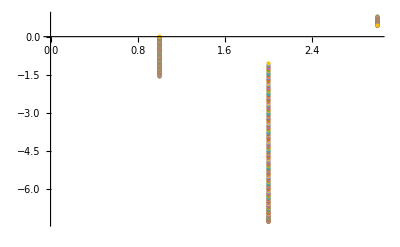

```mathematica
ListPlot[data]
```

```mathematica
Export["beta_vs_Gm_RpR0_gamma0.0001_rb17nm.csv",data]
```

beta_vs_Gm_RpR0_gamma0.0001_rb17nm.csv

#### Fixed rb, Gm vs γ

```mathematica
Rdome=41.82077878168754; (*Radius of curvature of the Piezo dome in units of nm, associated with raw and smoothed data*)
Ap=450;(*Membrane midplane area of the Piezo dome in units of nm^2*)
αB=ArcCos[1-Ap/(2 Pi Rdome^2)]; (*Fix Piezo dome-membrane contact angle*)
Kb=20; (*Lipid bilayer bending rigidity in units of Subscript[k, B] T*)
β=-N[π/2](*0, N[π/90], N[π/45], N[π/30]*);
Clear[γ];
λ=(Kb/γ)^(1/2) ;(*Characteristic decay length of membrane shape deformations in units of nm*)
Lc=Rdome*Sin[αB]; (*Characteristic length used to obtain dimensionless equations*)
RdomeB=Rdome/Lc;
λB=λ/Lc;
(*pψfBs=-0.060278;(*Rdome=42nm, γ=0.0001 Subscript[k, B] T/nm^2, β=0, rb=52nm, Lc=Rdome*Sin[αB]*)
sMaxs=40.425(*nm*)/Lc;*)
(*pψfBs=-0.125195;(*Rdome=42nm, γ=0.0001 Subscript[k, B] T/nm^2, β=-4 deg, rb=52nm, Lc=Rdome*Sin[αB]*)
sMaxs=40.3806(*nm*)/Lc;*)
(*pψfBs=0.00442796;(*Rdome=42nm, γ=0.0001 Subscript[k, B] T/nm^2, β=4 deg, rb=52nm, Lc=Rdome*Sin[αB]*)
sMaxs=40.5427(*nm*)/Lc;*)
(*pψfBs=0.0366238;(*Rdome=42nm, γ=0.0001 Subscript[k, B] T/nm^2, β=6 deg, rb=52nm, Lc=Rdome*Sin[αB]*)
sMaxs=40.6291(*nm*)/Lc;*)
(*pψfBs=-0.157655;(*Rdome=42nm, γ=0.0001 Subscript[k, B] T/nm^2, β=-6 deg, rb=52nm, Lc=Rdome*Sin[αB]*)
sMaxs=40.3857(*nm*)/Lc;*)
(*pψfBs=-1.0689707878746049;(*Rdome=42nm, γ=0.0001 Subscript[k, B] T/nm^2, β=-π/2, rb=52nm, Lc=Rdome*Sin[αB]*)
sMaxs=66.19161863344647(*nm*)/Lc;*)
(*pψfBs=-0.175012;(*Rdome=42nm, γ=0.0001 Subscript[k, B] T/nm^2, β=0, rb=32nm, Lc=Rdome*Sin[αB]*)
sMaxs=20.3405(*nm*)/Lc;*)
(*pψfBs=-0.23327;(*Rdome=42nm, γ=0.0001 Subscript[k, B] T/nm^2, β=-2 deg, rb=32nm, Lc=Rdome*Sin[αB]*)
sMaxs=20.3184(*nm*)/Lc;*)
(*pψfBs=-0.116814;(*Rdome=42nm, γ=0.0001 Subscript[k, B] T/nm^2, β=2 deg, rb=32nm, Lc=Rdome*Sin[αB]*)
sMaxs=20.372(*nm*)/Lc;*)
(*pψfBs=-0.0587237;(*Rdome=42nm, γ=0.0001 Subscript[k, B] T/nm^2, β=4 deg, rb=32nm, Lc=Rdome*Sin[αB]*)
sMaxs=20.4128(*nm*)/Lc;*)
(*pψfBs=-0.291541;(*Rdome=42nm, γ=0.0001 Subscript[k, B] T/nm^2, β=-4 deg, rb=32nm, Lc=Rdome*Sin[αB]*)
sMaxs=20.3056(*nm*)/Lc;*)
(*pψfBs=-0.349777;(*Rdome=42nm, γ=0.0001 Subscript[k, B] T/nm^2, β=-6 deg, rb=32nm, Lc=Rdome*Sin[αB]*)
sMaxs=20.302(*nm*)/Lc;*)
(*pψfBs=-0.00078863;(*Rdome=42nm, γ=0.0001 Subscript[k, B] T/nm^2, β=6 deg, rb=32nm, Lc=Rdome*Sin[αB]*)
sMaxs=20.463(*nm*)/Lc;*)
(*pψfBs=-0.451952;(*Rdome=42nm, γ=0.0001 Subscript[k, B] T/nm^2, β=0, rb=22nm, Lc=Rdome*Sin[αB]*)
sMaxs=10.2686(*nm*)/Lc;*)
(*pψfBs=-0.348634;(*Rdome=42nm, γ=0.0001 Subscript[k, B] T/nm^2, β=2 deg, rb=22nm, Lc=Rdome*Sin[αB]*)
sMaxs=10.2866(*nm*)/Lc;*)
(*pψfBs=-0.55532;(*Rdome=42nm, γ=0.0001 Subscript[k, B] T/nm^2, β=-2 deg, rb=22nm, Lc=Rdome*Sin[αB]*)
sMaxs=10.2552(*nm*)/Lc;*)
(*pψfBs=-0.658666;(*Rdome=42nm, γ=0.0001 Subscript[k, B] T/nm^2, β=-4 deg, rb=22nm, Lc=Rdome*Sin[αB]*)
sMaxs=10.2465(*nm*)/Lc;*)
(*pψfBs=-0.245438;(*Rdome=42nm, γ=0.0001 Subscript[k, B] T/nm^2, β=4 deg, rb=22nm, Lc=Rdome*Sin[αB]*)
sMaxs=10.3093(*nm*)/Lc;*)
(*pψfBs=-0.142438;(*Rdome=42nm, γ=0.0001 Subscript[k, B] T/nm^2, β=6 deg, rb=22nm, Lc=Rdome*Sin[αB]*)
sMaxs=10.3367(*nm*)/Lc;*)
(*pψfBs=-0.761916;(*Rdome=42nm, γ=0.0001 Subscript[k, B] T/nm^2, β=-6 deg, rb=22nm, Lc=Rdome*Sin[αB]*)
sMaxs=10.2424(*nm*)/Lc;*)
(*pψfBs=-1.04855;(*Rdome=42nm, γ=0.0001 Subscript[k, B] T/nm^2, β=0, rb=17nm, Lc=Rdome*Sin[αB]*)
sMaxs=5.21915(*nm*)/Lc;*)
(*pψfBs=-0.863621;(*Rdome=42nm, γ=0.0001 Subscript[k, B] T/nm^2, β=2 deg, rb=17nm, Lc=Rdome*Sin[αB]*)
sMaxs=5.2288(*nm*)/Lc;*)
(*pψfBs=-0.678839;(*Rdome=42nm, γ=0.0001 Subscript[k, B] T/nm^2, β=4 deg, rb=17nm, Lc=Rdome*Sin[αB]*)
sMaxs=5.24078(*nm*)/Lc;*)
(*pψfBs=-1.23352;(*Rdome=42nm, γ=0.0001 Subscript[k, B] T/nm^2, β=-2 deg, rb=17nm, Lc=Rdome*Sin[αB]*)
sMaxs=5.2118(*nm*)/Lc;*)
(*pψfBs=-1.4184;(*Rdome=42nm, γ=0.0001 Subscript[k, B] T/nm^2, β=-4 deg, rb=17nm, Lc=Rdome*Sin[αB]*)
sMaxs=5.20675(*nm*)/Lc;*)
(*pψfBs=-1.60308;(*Rdome=42nm, γ=0.0001 Subscript[k, B] T/nm^2, β=-6 deg, rb=17nm, Lc=Rdome*Sin[αB]*)
sMaxs=5.20397(*nm*)/Lc;*)
(*pψfBs=-0.157655;(*Rdome=42nm, γ=0.0001 Subscript[k, B] T/nm^2, β=-6 deg, rb=52nm, Lc=Rdome*Sin[αB]*)
sMaxs=40.3857(*nm*)/Lc;*)
pψfBs=-1.01969(*Rdome=Open, γ=0.0001 Subscript[k, B] T/nm^2, β=-π/2, rb=52nm, Lc=Rdome*Sin[αB]*);
sMaxs=67.6991(*nm*)/Lc;
(*pψfBs=-1.0689707878746049;(*Rdome=42nm, γ=0.0001 Subscript[k, B] T/nm^2, β=-π/2, rb=52nm, Lc=Rdome*Sin[αB]*)
sMaxs=66.19161863344647(*nm*)/Lc;*)
Timing[data0=Reap[For[γ=0.0001,γ<=1.1,γ=γ+0.0005,
sols=FindRoot[shoot[sbB,pψfBi]=={β,52/Lc},{sbB,sMaxs},{pψfBi,pψfBs}];
(*Use the values of the shooting variables determined in one interation as initial guesses for next iteration:*)
pψfBs=pψfBi/.sols;
sMaxs=sbB/.sols;

dummy=Evaluate[shoot[sMaxs,pψfBs]]; Print[γ,dummy];
(*To check that we indeed have ψfB[sB] = 0 and prfB[sB] = 0 at s = sbB*)

(*Assemble solution using the correct values of the shooting variables:*)
ndsol=SolveShapeEqs[sMaxs,pψfBs];

(*Calculate bending energy in units of Subscript[k, B] T:*)
ψff[s_]=First[ψfB[s]/.ndsol];
rff[s_]=First[rfB[s]/.ndsol];
enBend=Kb π rff[s](D[ψff[s],s]+Sin[ψff[s]]/rff[s])^2;
enTension=2π γ rff[s](1-Cos[ψff[s]]);
GmBend=NIntegrate[enBend,{s,s0B,sMaxs}];
GmTension=NIntegrate[enTension,{s,s0B,sMaxs}];
Sow[{γ,GmBend,GmTension}];

(*en=Kb π rff[s]((D[ψff[s],s]+Sin[ψff[s]]/rff[s])^2+2/λB^2(1-Cos[ψff[s]]));
G=NIntegrate[en,{s,s0B,sMaxs}];

Sow[{γ,G}] (*Export data*);*)
]];]
data=data0[[2]][[1]];
```

{932.297,Null}

```mathematica
data[[-1]]
```

{1.0996,998.487,6.43045}

```mathematica
ListPlot[data]
```

```mathematica
Export["gamma_GmBend_GmTension_Rpflat_beta-90deg_rb52nm.csv",data];
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["gamma_GmBend_GmTension_Rpflat_beta-90deg_rb52nm.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["gamma_GmBend_GmTension_RpR0_beta-90deg_rb52nm.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["gamma_vs_Gm_Rpflat_beta-90deg_rb52nm.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["gamma_vs_Gm_RpR0_beta-90deg_rb52nm.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["gamma_vs_Gm_Rpflat_beta-6deg_rb52nm.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["gamma_vs_Gm_Rpflat_beta-4deg_rb52nm.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["gamma_vs_Gm_Rpflat_beta-2deg_rb52nm.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["gamma_vs_Gm_Rpflat_beta6deg_rb52nm.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["gamma_vs_Gm_Rpflat_beta4deg_rb52nm.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["gamma_vs_Gm_Rpflat_beta2deg_rb52nm.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["gamma_vs_Gm_Rpflat_beta-6deg_rb32nm.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["gamma_vs_Gm_Rpflat_beta-4deg_rb32nm.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["gamma_vs_Gm_Rpflat_beta-2deg_rb32nm.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["gamma_vs_Gm_Rpflat_beta6deg_rb32nm.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["gamma_vs_Gm_Rpflat_beta4deg_rb32nm.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["gamma_vs_Gm_Rpflat_beta2deg_rb32nm.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["gamma_vs_Gm_Rpflat_beta-6deg_rb22nm.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["gamma_vs_Gm_Rpflat_beta-4deg_rb22nm.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["gamma_vs_Gm_Rpflat_beta-2deg_rb22nm.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["gamma_vs_Gm_Rpflat_beta6deg_rb22nm.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["gamma_vs_Gm_Rpflat_beta4deg_rb22nm.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["gamma_vs_Gm_Rpflat_beta2deg_rb22nm.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["gamma_vs_Gm_Rpflat_beta-6deg_rb17nm.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["gamma_vs_Gm_Rpflat_beta-4deg_rb17nm.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["gamma_vs_Gm_Rpflat_beta-2deg_rb17nm.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["gamma_vs_Gm_Rpflat_beta6deg_rb17nm.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["gamma_vs_Gm_Rpflat_beta4_rb17nm.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["gamma_vs_Gm_Rpflat_beta2_rb17nm.csv"]]]
```

#### Gm as a function of β and γ

```mathematica
Rdome=41.82077878168754; (*Radius of curvature of the Piezo dome in units of nm, associated with raw and smoothed data*)
Scap=450;(*Membrane midplane area of the Piezo dome in units of nm^2*)
αB=ArcCos[1-Scap/(2 Pi Rdome^2)]; (*Fix Piezo dome-membrane contact angle*)
Kb=20; (*Lipid bilayer bending rigidity in units of Subscript[k, B] T*)
γ=0.0001;
Clear[γ] (*Membrane tension in units of Subscript[k, B] T/nm^2*)
λ=(Kb/γ)^(1/2) ;(*Characteristic decay length of membrane shape deformations in units of nm*)
Lc=Rdome*Sin[αB];(*Characteristic length used to obtain dimensionless equations*)
(*Lc=λ;*)
(*ri=Sqrt[Scap/π];
Lc=ri;
ri=ri/Lc;*)
RdomeB=Rdome/Lc;
λB=λ/Lc;
```

```mathematica
Clear[γ];
sMax=10/Lc;
prfBs=-3.3611638633404466*Lc/Sqrt[Kb/0.0001];(*Rdome=41.82077878168754 nm, γ=1*^-4, Lc=λ, sb=10 nm *)
pψfBs=-0.47482543696004587;
(*prfBs=-7.09017*Lc/Sqrt[Kb/0.0001];(*For Rdome=42nm, γ=0.0001, Lc=λ, sb=5nm/Lc*)
pψfBs=-1.11485;*)
(*prfBs=-3.3611638633404466*Lc/Sqrt[Kb/0.0001];(*Rdome=41.82077878168754 nm, γ=1*^-4, Lc=λ, sb=10 nm *)
pψfBs=-0.47482543696004587;*)
(*prfBs=-0.011193022142760635;(*Rdome=42nm, γ=1*^-4 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[α], sb=20nm*)
pψfBs=-0.18187701329999983;*)
(*prfBs=-0.004281797587261707;(*Rdome=42nm, γ=1*^-4 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[α], sb=40nm*)
pψfBs=-0.06201089738701742;*)
Timing[data0=Reap[For[β=N[-π/2],(*γ≥0.00009*)β<=N[π/2],β=(*γ-0.0001*)β+0.01,
prfBs=-7.09017*Lc/Sqrt[Kb/0.0001];(*For Rdome=42nm, γ=0.0001, Lc=λ, sb=5nm/Lc*)
pψfBs=-1.11485;
For[γ=(*0.01*)0.0001,(*γ≥0.00009*)γ<=1.1,γ=(*γ-0.0001*)γ+0.0005,
(*Adjust the dimensionless shooting variables so as to satisfy boundary conditions on ψ[s] and pr[s] at s = sb:*)
sols=FindRoot[shoot[sMax,pψfBi,prfBi]=={β,0},{pψfBi,pψfBs},{prfBi,prfBs}];

(*Use the values of the shooting variables determined in one interation as initial guesses for next iteration:*)
pψfBs=pψfBi/.sols;
prfBs=prfBi/.sols;

(*dummy=Evaluate[shoot[sMax,pψfBs,prfBs]]; Print[γ,dummy];*)
(*To check that we indeed have ψfB[sB] = 0 and prfB[sB] = 0 at s = sbB*)

(*Assemble solution using the correct values of the shooting variables:*)
ndsol=SolveShapeEqs[sMax,pψfBs,prfBs];

(*Calculate bending energy in units of Subscript[k, B] T:*)
ψff[s_]=First[ψfB[s]/.ndsol];
rff[s_]=First[rfB[s]/.ndsol];
en=Kb π rff[s]((D[ψff[s],s]+Sin[ψff[s]]/rff[s])^2+2/λB^2(1-Cos[ψff[s]])); 
G=NIntegrate[en,{s,s0B,sMax}];

Sow[{β,γ,G}] (*Export data*);
(*Print[γ];
Sow[{γ,prfBs,pψfBs}];*)
(*Sow[{γ,1/2*(ψff'[sMax]+Sin[ψff[sMax]]/rff[sMax])/Lc}]*)
]]];]

data=data0[[2]][[1]];
```

#### Gm as a function of β and γ for fixed rb

```mathematica
(* ==========================================================*)
(*1. WORKER FUNCTION (Physics& Logic Encapsulated)*)
(* ==========================================================*)
Rdome=41.82077878168754;Ap=450;alphaClosed=ArcCos[1-Ap/(2π Rdome^2)];Lc=Rdome*Sin[alphaClosed];
RunSweepChunk[taskSpec_]:=Module[{
(*Extraction of Task Parameters*)
rbNM=taskSpec[["Rb"]],gammaStart=taskSpec[["GammaStart"]],gammaEnd=taskSpec[["GammaEnd"]],numGammaPoints=taskSpec[["NumGamma"]],startSb=taskSpec[["GuessSb"]],startPPsi=taskSpec[["GuessPPsi"]],
(*Physics Constants*)
Rdome=41.82077878168754,Ap=450.0,Kb=20.0,alphaClosed,Lc,RdomeB,rbTarget,
(*Solver Variables*)
getPr0,pSol,shootErr,getEnergy,gammaList,betaList,currSb,currPPsi,currentBetas,sol,en,i,gam,beta,chunkData},
(*---A.GEOMETRY SETUP---*)
alphaClosed=ArcCos[1-Ap/(2 Pi Rdome^2)];
Lc=Rdome*Sin[alphaClosed];
RdomeB=Rdome/Lc;
rbTarget=rbNM/Lc;
(*---B.PHYSICS DEFINITIONS (Local to Kernel)---*)
(*H=0 Constraint Helper*)
getPr0[pPsi_,g_]:=Module[{lambdaBsq,sinA,cosA,tanA},lambdaBsq=(Kb/g)/Lc^2;
sinA=Sin[alphaClosed];cosA=Cos[alphaClosed];tanA=Tan[alphaClosed];
(pPsi/cosA)*(-(pPsi/(4*RdomeB*sinA))+1/RdomeB)+(2*RdomeB*tanA/lambdaBsq)*(1-cosA)];
(*COMPILED PARAMETRIC SOLVER*)
(*Normalized domain t in[0,1] via s=t*sb*)pSol=ParametricNDSolveValue[{psi'[t]==sb*(pPsi[t]-2 Sin[psi[t]])/(2 r[t]),r'[t]==sb*Cos[psi[t]],h'[t]==sb*Sin[psi[t]],pPsi'[t]==sb*((pPsi[t]/r[t])*Cos[psi[t]]+((2 r[t])/((Kb/g)/Lc^2)+pr[t])*Sin[psi[t]]),pr'[t]==sb*((pPsi[t]/(4 r[t]^2))*(pPsi[t]-4 Sin[psi[t]])+(2/((Kb/g)/Lc^2))*(1-Cos[psi[t]])),
(*Energy Integration*)
En'[t]==sb*Kb*Pi*r[t]*(((pPsi[t]-2 Sin[psi[t]])/(2 r[t])+Sin[psi[t]]/r[t])^2+(2/((Kb/g)/Lc^2))*(1-Cos[psi[t]])),
(*ICs*)
psi[0]==alphaClosed,r[0]==RdomeB*Sin[alphaClosed],h[0]==RdomeB*(1-Cos[alphaClosed]),pPsi[0]==pPsi0,pr[0]==getPr0[pPsi0,g],En[0]==0},{psi[1],r[1],En[1]},{t,0,1},{sb,pPsi0,g},Method->"StiffnessSwitching",PrecisionGoal->6,AccuracyGoal->6];
shootErr[sb_,pPsi_,g_,bT_]:=Module[{res},res=pSol[sb,pPsi,g];
{res[[1]]-bT,res[[2]]-rbTarget}];
getEnergy[sb_,pPsi_,g_]:=Last[pSol[sb,pPsi,g]];
(*---C.EXECUTION---*)
(*Define Grids*)
(*Gamma:Linear Chunk*)
gammaList=Subdivide[gammaStart,gammaEnd,numGammaPoints-1];
(*Beta:-90 to 90 (Linear)*)
betaList=Subdivide[N[-Pi/2],N[Pi/2],1000];
(*Initialize Guess*)
currSb=startSb;
currPPsi=startPPsi;
(*Run Serpentine Loop*)
(*Returns list of {beta,gamma,energy}*)
chunkData=Reap[Do[
(*1. Determine Direction*)
(*Since we ALWAYS start with a valid guess for Beta=-90 (index 1),The first row (i=1) MUST go Forward.Odd rows=Forward,Even rows=Backward.*)
currentBetas=If[OddQ[i],betaList,Reverse[betaList]];
(*2. Inner Loop over Beta*)
Do[
sol=Check[FindRoot[shootErr[sb,pPsi,gam,b]=={0,0},{{sb,currSb},{pPsi,currPPsi}},AccuracyGoal->6,PrecisionGoal->6],$Failed];
If[sol=!=$Failed,currSb=sb/. sol;
currPPsi=pPsi/. sol;
en=getEnergy[currSb,currPPsi,gam];
Sow[{b*180/Pi,gam,en}];,
(*Convergence Failure Handling*)
(*Keep old guess,skip point.*)
Null];,{b,currentBetas}];,{i,1,Length[gammaList]} 
(*Gamma Loop*),
{gam,gammaList}];][[2]];
(*Flatten the Reap structure if necessary and return*)
If[chunkData==={},{},chunkData[[1]]]];


(* ==========================================================*)
(*2. CONFIGURATION:TASK LIST*)
(* ==========================================================*)

(*INPUT INSTRUCTIONS:Replace the "REPLACE_SB" and "REPLACE_PPS" placeholders below with your actual numerical values for Beta=-90 deg.Total Gammas desired:1100. Chunk 1:0.0001 to 0.5 (~500 pts) Chunk 2:0.5 to 1.0 (~500 pts) Chunk 3:1.0 to 1.1 (~100 pts)*)

taskParams={(*---Rb=17 nm---*)
<|"Rb"->17,"GammaStart"->0.0001,"GammaEnd"->0.5,"NumGamma"->500,"GuessSb"->9.41781/Lc,"GuessPPsi"->-7.28892|>,<|"Rb"->17,"GammaStart"->0.5,"GammaEnd"->1.0,"NumGamma"->500,"GuessSb"->7.70125505983806/Lc,"GuessPPsi"->-6.464252794594437|>,<|"Rb"->17,"GammaStart"->1.0,"GammaEnd"->1.1,"NumGamma"->100,"GuessSb"->REPLACE_SB_17_HIGH,"GuessPPsi"->REPLACE_PPS_17_HIGH|>,
(*---Rb=22 nm---*)
<|"Rb"->22,"GammaStart"->0.0001,"GammaEnd"->0.5,"NumGamma"->500,"GuessSb"->REPLACE_SB_22_LOW,"GuessPPsi"->REPLACE_PPS_22_LOW|>,<|"Rb"->22,"GammaStart"->0.5,"GammaEnd"->1.0,"NumGamma"->500,"GuessSb"->REPLACE_SB_22_MID,"GuessPPsi"->REPLACE_PPS_22_MID|>,<|"Rb"->22,"GammaStart"->1.0,"GammaEnd"->1.1,"NumGamma"->100,"GuessSb"->REPLACE_SB_22_HIGH,"GuessPPsi"->REPLACE_PPS_22_HIGH|>,
(*---Rb=32 nm---*)
<|"Rb"->32,"GammaStart"->0.0001,"GammaEnd"->0.5,"NumGamma"->500,"GuessSb"->REPLACE_SB_32_LOW,"GuessPPsi"->REPLACE_PPS_32_LOW|>,<|"Rb"->32,"GammaStart"->0.5,"GammaEnd"->1.0,"NumGamma"->500,"GuessSb"->REPLACE_SB_32_MID,"GuessPPsi"->REPLACE_PPS_32_MID|>,<|"Rb"->32,"GammaStart"->1.0,"GammaEnd"->1.1,"NumGamma"->100,"GuessSb"->REPLACE_SB_32_HIGH,"GuessPPsi"->REPLACE_PPS_32_HIGH|>,
(*---Rb=52 nm---*)
<|"Rb"->52,"GammaStart"->0.0001,"GammaEnd"->0.5,"NumGamma"->500,"GuessSb"->REPLACE_SB_52_LOW,"GuessPPsi"->REPLACE_PPS_52_LOW|>,<|"Rb"->52,"GammaStart"->0.5,"GammaEnd"->1.0,"NumGamma"->500,"GuessSb"->REPLACE_SB_52_MID,"GuessPPsi"->REPLACE_PPS_52_MID|>,<|"Rb"->52,"GammaStart"->1.0,"GammaEnd"->1.1,"NumGamma"->100,"GuessSb"->REPLACE_SB_52_HIGH,"GuessPPsi"->REPLACE_PPS_52_HIGH|>};


(* ==========================================================*)
(*3. EXECUTION& EXPORT*)
(* ==========================================================*)

(*Launch Kernels if not already running*)
If[Length[Kernels[]]<Length[taskParams],LaunchKernels[]];

Print["Distributing ",Length[taskParams]," tasks to parallel kernels..."];

(*Run Parallel Map*)
(*This sends each Task Association to a worker kernel*)
rawResults=ParallelMap[RunSweepChunk,taskParams];

Print["Computation Complete. Processing and saving files..."];

(*Organize and Export*)
(*We group by Rb value to combine the chunks back into single files*)

uniqueRbs=DeleteDuplicates[taskParams[[All,"Rb"]]];

Do[(*Select all results matching this Rb*)
currentRb=uniqueRbs[[i]];
(*Identify which tasks corresponded to this Rb*)
indices=Flatten[Position[taskParams,_?(#["Rb"]==currentRb&)]];
(*Join the data from the chunks*)
combinedData=Join@@Part[rawResults,indices];
(*Sort:First by Gamma,Then by Beta*)
sortedData=SortBy[combinedData,{#[[2]],#[[1]]}&];
(*Export*)
fileName="Piezo_Landscape_Rb_"<>ToString[currentRb]<>".csv";
Export[fileName,Prepend[sortedData,{"Beta(deg)","Gamma","Gm(kT)"}]];
Print["Saved: ",fileName];,{i,1,Length[uniqueRbs]}];

Print["All done."];
```

```mathematica
(*pψfBs=-1.06897(*Rdome=42nm, γ=0.0001 Subscript[k, B] T/nm^2, β=-π/2, rb=52nm, Lc=Rdome*Sin[αB]*);
sMaxs=66.2324(*nm*)/Lc;*)
(*pψfBs=-0.8803091959539351;(*Rdome=42nm, γ= 0.5 Subscript[k, B] T/nm^2, β=-π/2, rb=52nm, Lc=Rdome*Sin[α]*)
sMaxs=44.0508056423154(*nm*)/Lc;*)
(*pψfBs=-1.2879047049924437;(*Rdome=42nm, γ = 1 Subscript[k, B] T/nm^2, β=-π/2, rb=52nm, Lc=Rdome*Sin[α]*)
sMaxs=42.90325225854652(*nm*)/Lc;*)
(*pψfBs=-2.04418(*Rdome=42nm, γ=0.0001 Subscript[k, B] T/nm^2, β=-π/2, rb=32nm, Lc=Rdome*Sin[αB]*);
sMaxs=34.3149(*nm*)/Lc;*)
(*pψfBs=-1.2798383640847093;(*Rdome=42nm, γ = 0.5 Subscript[k, B] T/nm^2, β=-π/2, rb=32nm, Lc=Rdome*Sin[αB]*)
sMaxs=23.94815311366538(*nm*)/Lc;*)
(*pψfBs=-1.4433524232620234;(*Rdome=42nm, γ = 1 Subscript[k, B] T/nm^2, β=-π/2, rb=32nm, Lc=Rdome*Sin[αB]*)
sMaxs=22.89090902880599(*nm*)/Lc;*)
(*pψfBs=-3.86798(*Rdome=42nm, γ=0.0001 Subscript[k, B] T/nm^2, β=-π/2, rb=22nm, Lc=Rdome*Sin[αB]*);
sMaxs=17.9244(*nm*)/Lc;*)
(*pψfBs=-2.9058153790279;(*Rdome=42nm, γ = 0.5 Subscript[k, B] T/nm^2, β=-π/2, rb=22nm, Lc=Rdome*Sin[αB]*)
sMaxs=13.491616317415508(*nm*)/Lc;*)
(*pψfBs=-2.654329203704334;(*Rdome=42nm, γ = 1 Subscript[k, B] T/nm^2, β=-π/2, rb=22nm, Lc=Rdome*Sin[αB]*)
sMaxs=12.700897544425674(*nm*)/Lc;*)
(*pψfBs=-7.28892(*Rdome=42nm, γ=0.0001 Subscript[k, B] T/nm^2, β=-π/2, rb=17nm, Lc=Rdome*Sin[αB]*);
sMaxs=9.41781(*nm*)/Lc;*)
(*pψfBs=-6.464252794594437;(*Rdome=42nm, γ = 0.5 Subscript[k, B] T/nm^2, β=-π/2, rb=17nm, Lc=Rdome*Sin[αB]*)
sMaxs=7.70125505983806(*nm*)/Lc;*)
(*pψfBs=-6.036734962959053;(*Rdome=42nm, γ = 1 Subscript[k, B] T/nm^2, β=-π/2, rb=17nm, Lc=Rdome*Sin[αB]*)
sMaxs=7.246693499252439(*nm*)/Lc;*)
```

### G as a function of γ

```mathematica
Rdome=41.82077878168754 (*1/2*)(*2*); (*Radius of curvature of the Piezo dome in units of nm, associated with raw and smoothed data*)
Scap=450(*1.0 450*) (*1/2*)(*2/3*);(*Membrane midplane area of the Piezo dome in units of nm^2*)
αB=ArcCos[1-Scap/(2 Pi Rdome^2)]; (*Fix Piezo dome-membrane contact angle*)
Kb=20(*20*); (*Lipid bilayer bending rigidity in units of Subscript[k, B] T*)
γ=0.0001;
Clear[γ] (*Membrane tension in units of Subscript[k, B] T/nm^2*)
λ=(Kb/γ)^(1/2) ;(*Characteristic decay length of membrane shape deformations in units of nm*)
Lc=Rdome*Sin[αB];(*Characteristic length used to obtain dimensionless equations*)
(*Lc=λ;*)
(*ri=Sqrt[Scap/π];
Lc=ri;
ri=ri/Lc;*)
RdomeB=Rdome/Lc;
λB=λ/Lc;
```

```mathematica
Clear[γ]
sMax=5λB;

(*(*Reference values of shooting variables at γ = 0.01 k_B T/nm^2, Kb = 20 k_B T, Rdome = 41.82077878168754 nm:*)
pψfBs=-0.06293440963285328(*-0.063*);
prfBs=-0.013627638563264753(*-0.014*);*)
(*prfBs=-0.004281797587261707;(*Rdome=42nm, γ=1*^-4 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[α], sb=40nm*)
pψfBs=-0.06201089738701742;*)
(*prfBs=-3.3611638633404466;(*Rdome=41.82077878168754 nm, γ=1*^-4, Lc=λ, Kb=20, Scap=450, sb=10 nm *)
pψfBs=-0.47482543696004587;*)
(*prfBs=-1.2556527712579473;(*Rdome=41.82077878168754nm,γ=0.001,Lc=γ,sb=8.36263nm,β=0,Scap=450*)
-0.5747516686830932;*)
(*prfBs=-4.108436527829742;(*Rdome=42nm, γ=0.0001, Lc=λ, sb=8.36263nm, β=0, Scap=450*)
pψfBs=-0.597554489955383;*)
(*prfBs=-51.5374517525355;(*Rdome=10.2nm, γ=0.0001, Lc=λ, sb=10nm/Lc, β=0, Scap=390, Kb=20*)
pψfBs=-1.186700336372705;*)
(*prfBs=-113.92832616214437;(*Rdome=10.2nm, γ=0.0001, Lc=λ, sb=5nm/Lc, β=0, Scap=390, Kb=20*)
pψfBs=-3.1638807366783825;*)
(*prfBs=-0.16199996730878755*Lc/Sqrt[20/0.0001];(*Rdome = 10.2nm, γ=0.0001, Lc=λ, Kb=20, Scap=450*)
pψfBs=-0.0018310328584764197;*)
(*prfBs=-7.09017*Lc/Sqrt[Kb/0.0001];(*For Rdome = 42 nm, γ = 0.0001, Lc = λ, sb = 5nm/Lc, ψfB[sb]=0*)
pψfBs=-1.11485;*)
(*prfBs=-0.013862379662330653;(*At Rdome=42nm,γ=0.0001 Subscript[k, B] T/nm^2,Scap=450,Lc=λ,sb=5λB*)
pψfBs=-0.0014491702075504717;*)
(*pψfBs=-0.0026847801542390403;(*For Rdome=15.020778781687616, γ=0.0001, Lc=λ, Scap=450*)
prfBs=-0.09438408558121254*Lc/Sqrt[Kb/0.0001];*)
(*prfBs=-0.0006283880508549116;(*Rdome = 199nm, γ=0.0001, Lc=λ*)
pψfBs=-0.0003217377869996564;*)
(*prfBs=-0.00011104983460904045;(*Rdome = 199nm, γ=0.001, Lc=Rdome Sin[αB]*)
pψfBs=-0.0022533960244748973;*)
(*prfBs=-0.01147162257762087;(*Rdome=10.2nm, Kb=10, γ=0.0001, Scap=390, Lc=Sqrt[Scap]*)
pψfBs=-0.0035226970842228314;*)
(*prfBs=-0.0043832794094487895;(*Rdome=10.2nm, Kb=30, γ=0.0001, Scap=390, Lc=Sqrt[Scap]*)
pψfBs=-0.0012914601235777836;*)
(*prfBs=-0.1257739159081641;(*Rdome=11.2nm, γ=0.0001, Lc=λ, Scap=390, Kb=20*)
pψfBs=-0.0021256213359914134*)
(*prfBs=-0.04773170860792694;(*Rdome=20nm, γ=0.0001, Lc=λ, Scap=390, Kb=20*)
pψfBs=-0.0021322858270209828;*)
(*prfBs=-0.04773170860792694*Lc/Sqrt[20/0.0001];(*Rdome=20nm, γ=0.0001, Lc=λ, Scap=390, Kb=20*)
pψfBs=-0.0021322858270209828;*)
(*prfBs=-113.92832616214437;(*Rdome=10.2nm, γ=0.0001, Lc=λ, sb=5nm/Lc, β=0, Scap=390, Kb=20*)
pψfBs=-3.1638807366783825;*)
(*prfBs=-0.12212504367809182;(*Rdome=41.82077878168754 nm, γ=0.5, Lc=λ, Kb=20, Scap=450, sb=5 nm*)
pψfBs=-1.3863582387063256;*)
(*prfBs=-0.10010918178645983;(*Rdome=41.82077878168754 nm, γ=1, Lc=λ, Kb=20, Scap=450, sb=5 nm*)
pψfBs=-1.634174411417485;*)
(*prfBs=-0.030140548096101002;(*Rdome=2 Subscript[R, 0], γ=0.5, Lc=λ, Kb=20, Scap=450, sb=5 nm*)
pψfBs=-0.6968623379284999;*)
(*prfBs=-0.4929072737018563;(*Rdome=Subscript[R, 0]/2, γ=0.5, Lc=λ, Kb=20, Scap=450, sb=5 nm*)
pψfBs-2.6536847174496305;*)
(*prfBs=-12.137881353010519;(*Rdome=41.82077878168754 nm, γ=1*^-4, Lc=λ, Kb=20, Scap=450, sb=3 nm*)
pψfBs=-2.0087397262594147;*)
(*prfBs=-150.45715835263985;(*Rdome=41.82077878168754 nm, γ=1*^-4, Lc=λ, Kb=20, Scap=450, sb=10 nm, β=-π/2*)
pψfBs=-5.30586732314229;*)
(*prfBs=-3.3611638633404466;(*Rdome=41.82077878168754 nm, γ=1*^-4, Lc=λ, Kb=20, Scap=450, sb=10 nm *)
pψfBs=-0.47482543696004587;*)
(*prfBs=-0.011193022142760635;(*Rdome=42nm, γ=1*^-4 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[α], sb=20nm*)
pψfBs=-0.18187701329999983;*)
(*prfBs=-0.004281797587261707;(*Rdome=42nm, γ=1*^-4 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[α], sb=40nm*)
pψfBs=-0.06201089738701742;*)
(*prfBs=-0.013862379662330653;(*At Rdome=42nm,γ=0.0001 Subscript[k, B] T/nm^2,Scap=450,Lc=λ,sb=5λB*)
pψfBs=-0.0014491702075504717;*)
(*prfBs=-0.19101576480798957;(*Rdome = 42nm, γ=0.5, Scap = 450, Lc=RdomeSin[αB],sb=5λB,β=-π/2*)
pψfBs=-0.8702873848031721;*)
(*prfBs=-0.06292359832663419;(*Rdome=42nm,γ=0.0001 Subscript[k, B] T/nm^2,Scap=450 nm^2,Lc=RdomeSin[α],sb=5λB,β=-π/2*)
pψfBs=0.0035115598073522953;*)
(*prfBs=-0.2742278649951508;(*Rdome=42nm,γ=1,Scap=450,Lc=RdomeSin[αB],sb=5λB,β=-π/2*)
pψfBs=-1.3001846970180722;*)
(*prfBs=-0.04773170860792694;(*Rdome=20nm, γ=0.0001, Lc=λ, Scap=390, Kb=20*)
pψfBs=-0.0021322858270209828;*)
(*prfBs=-0.04773170860792694*Lc/Sqrt[Kb/0.0001];(*Rdome=20nm, γ=0.0001, Lc=λ, Scap=390, Kb=20*)
pψfBs=-0.0021322858270209828;*)
(*prfBs=-68.35010304211565;(*Rdome=42nm, γ=0.5 Subscript[k, B] T/nm^2, β=-90^o, sb=40nm, Lc=Rdome*Sin[αB]*)
pψfBs=-16.383519164439758;*)
(*prfBs=-32.72;(*Rdome=42nm, γ=0.0001 Subscript[k, B] T/nm^2, β=-90^o, Lc=Rdome*Sin[αB], sb=40nm*)
pψfBs=-1.59;*)
prfBs=-0.01386;(*At Rdome=42nm,γ=0.0001 Subscript[k, B] T/nm^2,Scap=450,Lc=λ,sb=5λB*)
pψfBs=-0.00145;
Timing[data0=Reap[For[γ=(*0.01*)0.0001,(*γ≥0.00009*)γ<=1.1(*0.50001*),γ=(*γ-0.0001*)γ+0.0005,
(*Adjust the dimensionless shooting variables so as to satisfy boundary conditions on ψ[s] and pr[s] at s = sb:*)
sols=FindRoot[shoot[sMax,pψfBi,prfBi]=={0,0},{pψfBi,pψfBs},{prfBi,prfBs}];

(*Use the values of the shooting variables determined in one interation as initial guesses for next iteration:*)
pψfBs=pψfBi/.sols;
prfBs=prfBi/.sols;

dummy=Evaluate[shoot[sMax,pψfBs,prfBs]]; Print[γ,dummy];
(*To check that we indeed have ψfB[sB] = 0 and prfB[sB] = 0 at s = sbB*)

(*Assemble solution using the correct values of the shooting variables:*)
ndsol=SolveShapeEqs[sMax,pψfBs,prfBs];

(*Calculate bending energy in units of Subscript[k, B] T:*)
ψff[s_]=First[ψfB[s]/.ndsol];
rff[s_]=First[rfB[s]/.ndsol];
en=Kb π rff[s]((D[ψff[s],s]+Sin[ψff[s]]/rff[s])^2+2/λB^2(1-Cos[ψff[s]])); 
G=NIntegrate[en,{s,s0B,sMax}];
Sow[{γ,G}] (*Export data*);
(*dA=2π*rff[s]*(1-Cos[ψff[s]]);
DeltaAmClosed=NIntegrate[dA,{s,s0B,sMax}];
Sow[{γ,DeltaAmClosed}];*)
(*Print[γ];
Sow[{γ,prfBs,pψfBs}];*)
(*Sow[{γ,1/2*(ψff'[sMax]+Sin[ψff[sMax]]/rff[sMax])/Lc}]*)
]];]

data=data0[[2]][[1]];
```

{240.516,Null}

```mathematica
data[[-1]]
```

{1.0996,492.183}

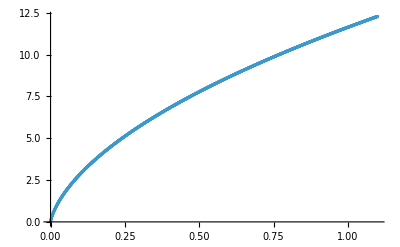

```mathematica
ListPlot[data,PlotRange->Full]
```

```mathematica
Export["gamma_vs_Gm_RpR0_beta0_asymp.csv",data]
```

gamma_vs_Gm_RpR0_beta0_asymp.csv

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["gamma_vs_Gm_RpR0_beta0_asymp.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["gamma_vs_DeltaAproj_Closed_beta0_asymp.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["gamma_vs_Gm_RpR0_beta-45deg_sb40.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["gamma_vs_Gm_Rpflat_beta-45deg_sb40.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["gamma_vs_Gm_Rpflat_beta-90deg_sb40.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["gamma_vs_Gm_RpR0_beta-90deg_sb40.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["gamma_vs_Gm_Rpflat_beta-90deg_sb40.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["gamma_vs_Gm_RpR0_beta-90deg_sb40.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["gamma_vs_Gm_Rpflat_beta-0.1_sb20.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["gamma_vs_Gm_RpR0_beta-0.1_sb20.csv"]]]
```

```mathematica
Export["C:\\Users\\avish\\OneDrive\\Documents\\USC_PhD\\Spring 2025\\Piezo_Arclength_Data\\Datasets_for_paper_Topic1\\Po_vs_gamma\\H_vs_gamma(Rp_beta_sb)\\gamma_vs_H_RpR0_beta0.15_sb40.csv",data]
```

C:\Users\avish\OneDrive\Documents\USC_PhD\Spring 2025\Piezo_Arclength_Data\Datasets_for_paper_Topic1\Po_vs_gamma\H_vs_gamma(Rp_beta_sb)\gamma_vs_H_RpR0_beta0.15_sb40.csv

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["C:\\Users\\avish\\OneDrive\\Documents\\USC_PhD\\Spring 2025\\Piezo_Arclength_Data\\Datasets_for_paper_Topic1\\Po_vs_gamma\\gamma_vs_Gm_gating(R0_beta_sb)\\gamma_vs_Gm_RpR0.1_beta0_sb40.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["gamma_vs_Gm_RpR0_beta0.1_sb20.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["gamma_vs_Gm_RpR0_beta-0.15_asymp.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["gamma_vs_Gm_Rpflat_beta-0.15_sb5.csv"]]]
```

```mathematica
(*pψfBs = -0.0007573743166639671; (*At Rdome = 83.72077878168916, γ = 0.0001, Scap = 450, Lc = λ*)
prfBs = -0.003545399972874482;*)
```

#### Gm^bending as a function of β

```mathematica
Rdome=41.82077878168754 (*1/2*)(*2*); (*Radius of curvature of the Piezo dome in units of nm, associated with raw and smoothed data*)
Scap=450(*1.0 450*) (*1/2*)(*2/3*);(*Membrane midplane area of the Piezo dome in units of nm^2*)
αB=ArcCos[1-Scap/(2 Pi Rdome^2)]; (*Fix Piezo dome-membrane contact angle*)
Kb=20(*20*); (*Lipid bilayer bending rigidity in units of Subscript[k, B] T*)
γ=1; (*Membrane tension in units of Subscript[k, B] T/nm^2*)
Clear[β];
λ=(Kb/γ)^(1/2) ;(*Characteristic decay length of membrane shape deformations in units of nm*)
Lc=Rdome*Sin[αB];(*Characteristic length used to obtain dimensionless equations*)
(*Lc=λ;*)
(*ri=Sqrt[Scap/π];
Lc=ri;
ri=ri/Lc;*)
sMax=40/Lc;
RdomeB=Rdome/Lc;
λB=λ/Lc;
(*prfBs=-0.004281797587261707;(*Rdome=42nm, γ=1*^-4 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[α], sb=40nm*)
pψfBs=-0.06201089738701742;*)
(*prfBs=-0.04255780280600476;(*Rdome=42nm, γ=0.5 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[α], sb=40nm*)
pψfBs=-0.8589721478725089;*)
(*prfBs=-0.06145416264381031;(*Rdome=42nm, γ=1 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[α], sb=40nm*)
pψfBs=-1.2856797874440211;*)
(*prfBs=-0.06147113404434905;(*Rdome=42nm, γ=1 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[α], sb=20nm*)
pψfBs=-1.2860276250989393;*)
(*prfBs=-0.042722133935570485;(*Rdome=42nm, γ=0.5 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[α], sb=20nm*)
pψfBs=-0.862220153582393;*)
(*prfBs=-0.011193022142760635;(*Rdome=42nm, γ=1*^-4 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[α], sb=20nm*)
pψfBs=-0.18187701329999983;*)
(*prfBs=-150.45715835263985;(*Rdome=41.82077878168754 nm, γ=1*^-4, Lc=λ, sb=10 nm, β=-π/2*)
pψfBs=-5.30586732314229;*)
(*prfBs=-3.3611638633404683;(*Rdome=41.82077878168754 nm, γ=0.5, Lc=λ, sb=10 nm, β=0*)
pψfBs=-0.47482543696005286;*)
(*prfBs=-0.06296972443818921;(*Rdome=42nm, γ=1, Lc=λ, Kb=20, Scap=450, sb=10 nm*)
pψfBs=-1.3180316779063612;*)
(*prfBs=-0.10010918178645983;(*Rdome=42nm, γ=1, Lc=λ, Kb=20, Scap=450, sb=5 nm*)
pψfBs=-1.634174411417485;*)
(*prfBs=-0.12212504367809182;(*Rdome=42nm, γ=0.5, Lc=λ, Kb=20, Scap=450, sb=5 nm*)
pψfBs=-1.3863582387063256;*)
(*prfBs=-7.09017*Lc/Sqrt[Kb/0.0001];(*For Rdome=42 nm, γ=0.0001, Lc=λ, Kb=20, Scap=450, sb=5 nm, β=0*)
pψfBs=-1.11485;*)
prfBs=-0.06145416264381031;(*Rdome=42nm, γ=1 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[α], sb=40nm*)
pψfBs=-1.2856797874440211;
Timing[data0=Reap[For[β=N[-π/2],(*γ≥0.00009*)β<=N[π/2],β=(*γ-0.0001*)β+0.001,

(*Adjust the dimensionless shooting variables so as to satisfy boundary conditions on ψ[s] and pr[s] at s = sb:*)
sols=FindRoot[shoot[sMax,pψfBi,prfBi]=={β,0},{pψfBi,pψfBs},{prfBi,prfBs}];

(*Use the values of the shooting variables determined in one interation as initial guesses for next iteration:*)
pψfBs=pψfBi/.sols;
prfBs=prfBi/.sols;

dummy=Evaluate[shoot[sMax,pψfBs,prfBs]]; Print[β,dummy];
(*To check that we indeed have ψfB[sB] = 0 and prfB[sB] = 0 at s = sbB*)

(*Assemble solution using the correct values of the shooting variables:*)
ndsol=SolveShapeEqs[sMax,pψfBs,prfBs];

(*Calculate bending energy in units of Subscript[k, B] T:*)
ψff[s_]=First[ψfB[s]/.ndsol];
rff[s_]=First[rfB[s]/.ndsol];
en=Kb π rff[s](D[ψff[s],s]+Sin[ψff[s]]/rff[s])^2;
Gm=NIntegrate[en,{s,s0B,sMax}];

Sow[{β,Gm}] (*Export data*); 
(*Sow[{γ,First[rfB[sMax]/.ndsol]*Lc}];*)
(*Print[β]*)
(*Sow[{β,pψfBs,prfBs}]*)
]];]
```

{1311.25,Null}

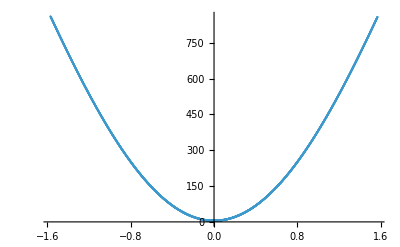

```mathematica
ListPlot[data0[[2]][[1]]]
```

```mathematica
data=data0[[2]][[1]];
Export["beta_vs_Gmbend_RpR0_gamma1_sb40.csv",data];
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["beta_vs_Gmbend_RpR0_gamma1_sb40.csv"]]]
```

#### Gm^γ (γ(A_flat-A_proj)) as a function of β

```mathematica
Rdome=41.82077878168754 (*1/2*)(*2*); (*Radius of curvature of the Piezo dome in units of nm, associated with raw and smoothed data*)
Scap=450(*1.0 450*) (*1/2*)(*2/3*);(*Membrane midplane area of the Piezo dome in units of nm^2*)
αB=ArcCos[1-Scap/(2 Pi Rdome^2)]; (*Fix Piezo dome-membrane contact angle*)
Kb=20(*20*); (*Lipid bilayer bending rigidity in units of Subscript[k, B] T*)
γ=0.0001; (*Membrane tension in units of Subscript[k, B] T/nm^2*)
Clear[β];
λ=(Kb/γ)^(1/2) ;(*Characteristic decay length of membrane shape deformations in units of nm*)
Lc=Rdome*Sin[αB];(*Characteristic length used to obtain dimensionless equations*)
(*Lc=λ;*)
(*ri=Sqrt[Scap/π];
Lc=ri;
ri=ri/Lc;*)
sMax=40/Lc;
RdomeB=Rdome/Lc;
λB=λ/Lc;
(*prfBs=-0.004281797587261707;(*Rdome=42nm, γ=1*^-4 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[α], sb=40nm*)
pψfBs=-0.06201089738701742;*)
(*prfBs=-0.04255780280600476;(*Rdome=42nm, γ=0.5 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[α], sb=40nm*)
pψfBs=-0.8589721478725089;*)
(*prfBs=-0.06145416264381031;(*Rdome=42nm, γ=1 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[α], sb=40nm*)
pψfBs=-1.2856797874440211;*)
(*prfBs=-0.06147113404434905;(*Rdome=42nm, γ=1 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[α], sb=20nm*)
pψfBs=-1.2860276250989393;*)
(*prfBs=-0.042722133935570485;(*Rdome=42nm, γ=0.5 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[α], sb=20nm*)
pψfBs=-0.862220153582393;*)
(*prfBs=-0.011193022142760635;(*Rdome=42nm, γ=1*^-4 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[α], sb=20nm*)
pψfBs=-0.18187701329999983;*)
(*prfBs=-150.45715835263985;(*Rdome=41.82077878168754 nm, γ=1*^-4, Lc=λ, sb=10 nm, β=-π/2*)
pψfBs=-5.30586732314229;*)
(*prfBs=-3.3611638633404683;(*Rdome=41.82077878168754 nm, γ=0.5, Lc=λ, sb=10 nm, β=0*)
pψfBs=-0.47482543696005286;*)
(*prfBs=-0.06296972443818921;(*Rdome=42nm, γ=1, Lc=λ, Kb=20, Scap=450, sb=10 nm*)
pψfBs=-1.3180316779063612;*)
(*prfBs=-0.10010918178645983;(*Rdome=42nm, γ=1, Lc=λ, Kb=20, Scap=450, sb=5 nm*)
pψfBs=-1.634174411417485;*)
(*prfBs=-0.12212504367809182;(*Rdome=42nm, γ=0.5, Lc=λ, Kb=20, Scap=450, sb=5 nm*)
pψfBs=-1.3863582387063256;*)
(*prfBs=-7.09017*Lc/Sqrt[Kb/0.0001];(*For Rdome=42 nm, γ=0.0001, Lc=λ, Kb=20, Scap=450, sb=5 nm, β=0*)
pψfBs=-1.11485;*)
prfBs=-0.004281797587261707;(*Rdome=42nm, γ=1*^-4 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[α], sb=40nm*)
pψfBs=0;
Timing[data0=Reap[For[β=N[-π/2],(*γ≥0.00009*)β<=N[π/2],β=(*γ-0.0001*)β+0.001,

(*Adjust the dimensionless shooting variables so as to satisfy boundary conditions on ψ[s] and pr[s] at s = sb:*)
sols=FindRoot[shoot[sMax,pψfBi,prfBi]=={β,0},{pψfBi,pψfBs},{prfBi,prfBs}];

(*Use the values of the shooting variables determined in one interation as initial guesses for next iteration:*)
pψfBs=pψfBi/.sols;
prfBs=prfBi/.sols;

dummy=Evaluate[shoot[sMax,pψfBs,prfBs]]; Print[β,dummy];
(*To check that we indeed have ψfB[sB] = 0 and prfB[sB] = 0 at s = sbB*)

(*Assemble solution using the correct values of the shooting variables:*)
ndsol=SolveShapeEqs[sMax,pψfBs,prfBs];

(*Calculate bending energy in units of Subscript[k, B] T:*)
ψff[s_]=First[ψfB[s]/.ndsol];
rff[s_]=First[rfB[s]/.ndsol];
en=Kb π rff[s](2/λB^2(1-Cos[ψff[s]])); 
Gm=NIntegrate[en,{s,s0B,sMax}];

Sow[{β,Gm}] (*Export data*); 
(*Sow[{γ,First[rfB[sMax]/.ndsol]*Lc}];*)
(*Print[β]*)
(*Sow[{β,pψfBs,prfBs}]*)
]];]
```

{462.375,Null}

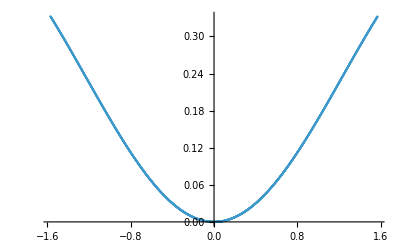

```mathematica
ListPlot[data0[[2]][[1]]]
```

```mathematica
data=data0[[2]][[1]];
Export["beta_vs_Gmgamma_Rpflat_gamma0.0001_sb40.csv",data];
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["beta_vs_Gmgamma_Rpflat_gamma0.0001_sb40.csv"]]]
```

#### Iterating over K_b

```mathematica
Rdome=10.2;
Scap=390;
αB=ArcCos[1-Scap/(2π*Rdome^2)];
γ=0.0001;
Clear[Kb];
λ=Sqrt[Kb/γ];
Lc=Sqrt[Scap];
λB=λ/Lc;
RdomeB=Rdome/Lc;
```

```mathematica
sMax=5*λB;
(*prfBs=-0.16199996730878755*Lc/Sqrt[Kb/0.0001];(*Rdome = 10.2nm, γ=0.0001, Lc=λ*)
pψfBs=-0.0018310328584764197;*)
(*prfBs=-0.01147162257762087;(*Rdome=10.2nm, Kb=10, γ=0.0001, Scap=390, Lc=Sqrt[Scap]*)
pψfBs=-0.0035226970842228314;*)
(*prfBs=-51.5374517525355;(*Rdome=10.2nm, Kb=20, γ=0.0001, Scap=390, Lc=λ, sb=10nm, β=0*)
pψfBs=-1.186700336372705;*)
Timing[data0=Reap[For[Kb=(*0.01*)10,(*γ≥0.00009*)Kb<=20,Kb=(*γ-0.0001*)Kb+0.1,

(*Adjust the dimensionless shooting variables so as to satisfy boundary conditions on ψ[s] and pr[s] at s = sb:*)
sols=FindRoot[shoot[sMax,pψfBi,prfBi]=={0,0},{pψfBi,pψfBs},{prfBi,prfBs}];

(*Use the values of the shooting variables determined in one interation as initial guesses for next iteration:*)
pψfBs=pψfBi/.sols;
prfBs=prfBi/.sols;

(*dummy=Evaluate[shoot[sMax,pψfBs,prfBs]]; Print[dummy];
(*To check that we indeed have ψfB[sB] = 0 and prfB[sB] = 0 at s = sbB*)*)

(*Assemble solution using the correct values of the shooting variables:*)
ndsol=SolveShapeEqs[sMax,pψfBs,prfBs];

(*(*Calculate bending energy in units of Subscript[k, B] T:*)
ψff[s_]=First[ψfB[s]/.ndsol];
rff[s_]=First[rfB[s]/.ndsol];
en=Kb π rff[s]((D[ψff[s],s]+Sin[ψff[s]]/rff[s])^2+2/λB^2(1-Cos[ψff[s]])); 
G=NIntegrate[en,{s,s0B,sMax}];

Sow[{γ,G}] (*Export data*); *)
(*Sow[{γ,First[rfB[sMax]/.ndsol]*Lc}];*)
Sow[{Kb,prfBs,pψfBs}];
(*Print[Kb]*)
]];]

data=data0[[2]][[1]];
```

{2.0625,Null}

```mathematica
data[[-1]]
```

{30.,-0.00438328,-0.00129146}

#### Iterating over s_b

```mathematica
Rdome=41.82077878168754;
Scap=450;
αB=ArcCos[1-Scap/(2π*Rdome^2)];
Kb=20;
Clear[sMax];
γ=1;
λ=Sqrt[Kb/γ];
Lc=Rdome;
RdomeB=Rdome/Lc;
λB=λ/Lc;
```

```mathematica
Clear[sMax];
(*prfBs=-113.92832616214437;(*Rdome=10.2nm, γ=0.0001, Lc=λ, sb=5nm/Lc, β=0, Scap=390, Kb=20*)
pψfBs=-3.1638807366783825;*)
(*prfBs=-7.09017;(*For Rdome = 42 nm, γ = 0.0001, Lc = λ, sb = 5nm/Lc, β=0*)
pψfBs=-1.11485;*)
(*prfBs=-4.108436527829742;(*Rdome=42nm, γ=0.0001, Lc=λ, sb=8.36263nm, β=0, Scap=450*)
pψfBs=-0.597554489955383;*)
(*prfBs=-0.12212504367809182;(*Rdome=41.82077878168754 nm, γ=0.5, Lc=λ, Kb=20, Scap=450, sb=5 nm*)
pψfBs=-1.3863582387063256;*)
(*prfBs=-12.137881353010519;(*Rdome=41.82077878168754 nm, γ=1*^-4, Lc=λ, Kb=20, Scap=450, sb=3 nm*)
pψfBs=-2.0087397262594147;*)
(*prfBs=-3.3611638633404466;(*Rdome=41.82077878168754 nm, γ=1*^-4, Lc=λ, Kb=20, Scap=450, sb=10 nm *)
pψfBs=-0.47482543696004587;*)
(*prfBs=-0.011193022142760635;(*Rdome=42nm, γ=1*^-4 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[α], sb=20nm*)
pψfBs=-0.18187701329999983;*)
(*prfBs=-0.004281797587261707;(*Rdome=42nm, γ=1*^-4 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[α], sb=40nm*)
pψfBs=-0.06201089738701742;*)
(*prfBs=-0.18450477530600914;(*Rdome=41.82077878168754 nm, γ=0.5, Lc=λ, Kb=20, Scap=450, sb=3 nm*)
pψfBs=-2.174122801029579;*)
(*prfBs=-0.08574863537564927;(*Rdome=41.82077878168754 nm, γ=0.5, Lc=λ, Kb=20, Scap=450, sb=10 nm *)
pψfBs=-0.9446325621940705;*)
(*prfBs=-0.042722133935570485;(*Rdome=42nm, Lc=Rdome*Sin[α], γ=0.5 Subscript[k, B] T/nm^2, sb=20nm*)
pψfBs=-0.862220153582393;*)
(*prfBs=-0.04255780280600476;(*Rdome=42nm, Lc=Rdome*Sin[α], γ=0.5 Subscript[k, B] T/nm^2, sb=40nm*)
pψfBs=-0.8589721478725089;*)
(*prfBs=-0.10010918178645983;(*Rdome=41.82077878168754 nm, γ=1, Lc=λ, Kb=20, Scap=450, sb=5 nm*)
pψfBs=-1.634174411417485;*)
(*prfBs=-0.10719734525599271;(*Rdome=41.82077878168754 nm, γ=1, Lc=λ, Kb=20, Scap=450, sb=3 nm*)
pψfBs=-2.3348979962336864;*)
(*prfBs=-0.06296972443818921;(*Rdome=41.82077878168754 nm, γ=1, Lc=λ, Kb=20, Scap=450, sb=10 nm*)
pψfBs=-1.3180316779063612;*)
(*prfBs=-0.06147113404434905;(*Rdome=42nm, Lc=Rdome*Sin[α], γ=1 Subscript[k, B] T/nm^2, sb=20nm*)
pψfBs=-1.2860276250989393;*)
(*prfBs=-0.06145416264381031;(*Rdome=42nm, Lc=Rdome*Sin[α], γ=1 Subscript[k, B] T/nm^2, sb=40nm*)
pψfBs=-1.2856797874440211;*)
(*prfBs=-0.005338267731682237;(*Rdome=42nm, γ=0.0001, Lc=λ, sb=10 λB, β=0, Scap=450*)
pψfBs=-0.07911618668138443;*)
(*prfBs=-0.042559208413802466;(*Rdome=42nm, γ=0.5, Lc=λ, sb=10 λB, β=0, Scap=450, Kb=20*)
pψfBs=-0.8589992441893428;*)
(*prfBs=-0.061454187225603585;(*Rdome=42nm, γ=1, Lc=λ, sb=10 λB, β=0, Scap=450, Kb=20*)
pψfBs=-1.2856802807528585;*)
(*prfBs=-0.004281797587261707;(*Rdome=42nm, γ=1*^-4 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[α], sb=40nm*)
pψfBs=-0.06201089738701742;*)
(*prfBs=-0.00791153699660939*Lc/(Rdome*Sin[αB]);(*Rdome=42nm, γ=1*^-4 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[αB], Subscript[s, b]=60nm*)
pψfBs=-0.031537260448121905;*)
(*prfBs=-0.004983587442175796*Lc/(Rdome*Sin[αB]);(*Rdome=42nm, γ=1*^-4 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[αB], Subscript[s, b]=80nm*)
pψfBs=-0.019273702988486033;*)
(*prfBs=-0.14646895060722487;(*Rdome=42nm, γ=0.5 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[αB], sb=60nm*)
pψfBs=-0.8589666960845027;*)
(*prfBs=-0.14646894887974285;(*Rdome=42nm, γ=0.5 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[αB], sb=80nm*)
pψfBs=-0.8589666865360124;*)
(*prfBs=-0.06145416264381031;(*Rdome=42nm, γ=1 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[α], sb=40nm*)
pψfBs=-1.2856797874440211;*)
(*prfBs=-6.412629270377944;(*Rdome=42nm, γ=1 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[αB], sb=60nm*)
pψfBs=-0.9813584816663744;*)
prfBs=-6.412629270377944*Lc/(Rdome*Sin[αB]);(*Rdome=42nm, γ=1 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[αB], sb=60nm*)
pψfBs=-0.9813584816663744;
Timing[data0=Reap[For[sMax=60/Lc,sMax<=80/Lc,sMax=sMax+1/Lc,

(*Adjust the dimensionless shooting variables so as to satisfy boundary conditions on ψ[s] and pr[s] at s = sb:*)
sols=FindRoot[shoot[sMax,pψfBi,prfBi]=={0,0},{pψfBi,pψfBs},{prfBi,prfBs}];

(*Use the values of the shooting variables determined in one interation as initial guesses for next iteration:*)
pψfBs=pψfBi/.sols;
prfBs=prfBi/.sols;

dummy=Evaluate[shoot[sMax,pψfBs,prfBs]]; Print[dummy];
(*To check that we indeed have ψfB[sB] = 0 and prfB[sB] = 0 at s = sbB*)

(*Assemble solution using the correct values of the shooting variables:*)
ndsol=SolveShapeEqs[sMax,pψfBs,prfBs];

(*(*Calculate bending energy in units of Subscript[k, B] T:*)
ψff[s_]=First[ψfB[s]/.ndsol];
rff[s_]=First[rfB[s]/.ndsol];
en=Kb π rff[s]((D[ψff[s],s]+Sin[ψff[s]]/rff[s])^2+2/λB^2(1-Cos[ψff[s]])); 
G=NIntegrate[en,{s,s0B,sMax}];

Sow[{γ,G}] (*Export data*); *)
(*Sow[{γ,First[rfB[sMax]/.ndsol]*Lc}];*)
Sow[{sMax*Lc,prfBs,pψfBs}]
(*Print[γ]*)
]];]
data=data0[[2]][[1]];
```

```mathematica
data[[-1]]
```

{60.,-6.41263,-0.981358}

#### Iterate over β

```mathematica
Rdome=41.82077878168754 (*1/2*)(*2*); (*Radius of curvature of the Piezo dome in units of nm, associated with raw and smoothed data*)
Scap=1.0 450 (*1/2*)(*2/3*);(*Membrane midplane area of the Piezo dome in units of nm^2*)
αB=ArcCos[1-Scap/(2 Pi Rdome^2)]; (*Fix Piezo dome-membrane contact angle*)
(*ri=Sqrt[Scap/π];*)
Kb=20; (*Lipid bilayer bending rigidity in units of Subscript[k, B] T*)
γ=0.0001;(*Membrane tension in units of Subscript[k, B] T/nm^2*)
λ=(Kb/γ)^(1/2) ;(*Characteristic decay length of membrane shape deformations in units of nm*)
Lc=λ;(*Characteristic length used to obtain dimensionless equations*)
(*Lc=ri*)
RdomeB=Rdome/Lc;
λB=λ/Lc;
(*riB=ri/Lc;*)
```

```mathematica
sMax=40/Lc;

(*Reference values of shooting variables at γ = 0.01 k_B T/nm^2, Kb = 20 k_B T, Rdome = 41.82077878168754 nm:*)
(*pψfBs=-0.06293440963285328(*-0.063*);
prfBs=-0.013627638563264753(*-0.014*);*)
(*prfBs=-0.12212504367809182;(*Rdome=41.82077878168754 nm, γ=0.5, Lc=λ, Kb=20, Scap=450, sb=5 nm*)
pψfBs=-1.3863582387063256;*)
(*prfBs=-0.10010918178645983;(*Rdome=41.82077878168754 nm, γ=1, Lc=λ, Kb=20, Scap=450, sb=5 nm*)
pψfBs=-1.634174411417485;*)
(*prfBs=-0.030140548096101002;(*Rdome=2 Subscript[R, 0], γ=0.5, Lc=λ, Kb=20, Scap=450, sb=5 nm*)
pψfBs=-0.6968623379284999;*)
(*prfBs=-0.4929072737018563;(*Rdome=Subscript[R, 0]/2, γ=0.5, Lc=λ, Kb=20, Scap=450, sb=5 nm*)
pψfBs-2.6536847174496305;*)
(*pψfBs=-0.0026847801542390403;(*For Rdome=15.020778781687616, γ=0.0001, Lc=λ, Scap=450*)
prfBs=-0.09438408558121254*Lc/Sqrt[Kb/0.0001];*)
(*prfBs=-3.3611638633404683;(*Rdome=41.82077878168754 nm, γ=0.5, Lc=λ, Kb=20, Scap=450, sb=10 nm*)
pψfBs=-0.47482543696005286;*)
(*prfBs=-12.137881353010519;(*Rdome=41.82077878168754 nm, γ=1*^-4, Lc=λ, Kb=20, Scap=450, sb=3 nm, β=0*)
pψfBs=-2.0087397262594147;*)
(*prfBs=-512.6636373145604;(*Rdome=41.82077878168754 nm, γ=1*^-4, Lc=λ, Kb=20, Scap=450, sb=3 nm, β=-π/2*)
pψfBs=-15.769426972500778;*)
(*prfBs=-7.09017*Lc/Sqrt[Kb/0.0001];(*For Rdome=42 nm, γ=0.0001, Lc=λ, Kb=20, Scap=450, sb=5 nm, β=0*)
pψfBs=-1.11485;*)
(*prfBs=-3.3611638633404466;(*Rdome=41.82077878168754 nm, γ=1*^-4, Lc=λ, Kb=20, Scap=450, sb=10 nm, β=0*)
pψfBs=-0.47482543696004587;*)
(*prfBs=-150.45715835263985;(*Rdome=41.82077878168754 nm, γ=1*^-4, Lc=λ, Kb=20, Scap=450, sb=10 nm, β=-π/2*)
pψfBs=-5.30586732314229;*)
(*prfBs=-0.10719734525599271;(*Rdome=41.82077878168754 nm, γ=1, Lc=λ, Kb=20, Scap=450, sb=3 nm, β=0*)
pψfBs=-2.3348979962336864;*)
(*prfBs=-14.660224820342123;(*Rdome=41.82077878168754 nm, γ=1, Lc=λ, Kb=20, Scap=450, sb=3 nm, β=-π/2*)
pψfBs=-15.237825770556698;*)
(*prfBs=-14.660224820342123;(*Rdome=open; γ=1*^-4; Lc=Sqrt[Scap/π],Kb=20,Scap=450,sb=7λB,β=-π/2*)
pψfBs=-15.237825770556698;*)
(*prfBs=0;(*Rdome=42nm, γ=0.0001, Lc=λ, sb=10 λB, β=0, Scap=450, Kb=20*)
pψfBs=0;*)
(*prfBs=-0.06292359832663419;(*Rdome=42nm,γ=0.0001 Subscript[k, B] T/nm^2,Scap=450 nm^2,Lc=RdomeSin[α],sb=5λB*)
pψfBs=0.0035115598073522953;*)
(*prfBs=-0.14646894887974285*Lc/(Rdome*Sin[αB]);(*Rdome=42nm, γ=0.5 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[αB], sb=80nm*)
pψfBs=-0.8589666865360124;*)
(*prfBs=-0.14646894887974285*Lc/(Rdome*Sin[αB]);(*Rdome=42nm, γ=0.5 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[αB], sb=80nm*)
pψfBs=-0.8589666865360124;*)
(*prfBs=-32.72;(*Rdome=42nm, γ=0.0001 Subscript[k, B] T/nm^2, β=-90^o, Lc=Rdome*Sin[αB], sb=40nm*)
pψfBs=-1.59;*)
prfBs=-0.004281797587261707;(*Rdome=42nm, γ=1*^-4 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[α], sb=40nm, β=0*)
pψfBs=-0.06201089738701742;

Timing[data0=Reap[For[β=(*0.01*)0,(*γ≥0.00009*)β>=N[-π/2],β=(*γ-0.0001*)β-0.001,

(*Adjust the dimensionless shooting variables so as to satisfy boundary conditions on ψ[s] and pr[s] at s = sb:*)
sols=FindRoot[shoot[sMax,pψfBi,prfBi]=={β,0},{pψfBi,pψfBs},{prfBi,prfBs}];

(*Use the values of the shooting variables determined in one interation as initial guesses for next iteration:*)
pψfBs=pψfBi/.sols;
prfBs=prfBi/.sols;

dummy=Evaluate[shoot[sMax,pψfBs,prfBs]]; Print[β,dummy];
(*To check that we indeed have ψfB[sB] = 0 and prfB[sB] = 0 at s = sbB*)

(*Assemble solution using the correct values of the shooting variables:*)
ndsol=SolveShapeEqs[sMax,pψfBs,prfBs];

(*(*Calculate bending energy in units of Subscript[k, B] T:*)
ψff[s_]=First[ψfB[s]/.ndsol];
rff[s_]=First[rfB[s]/.ndsol];
en=Kb π rff[s]((D[ψff[s],s]+Sin[ψff[s]]/rff[s])^2+2/λB^2(1-Cos[ψff[s]])); 
Gm=NIntegrate[en,{s,s0B,sMax}];

Sow[{β,Gm}] (*Export data*); 
(*Sow[{γ,First[rfB[sMax]/.ndsol]*Lc}];*)*)
Sow[{β,prfBs,pψfBs}]
(*Print[β]*)
]];]

data=data0[[2]][[1]];
```

{155.875,Null}

```mathematica
data[[-1]]
```

{-1.57,-32.7236,-1.5924}

#### G as a function of γ in a finite compartment (sb=5nm) and with 0 gradient at outer boundary in closed conformation

```mathematica
Rdome=41.82077878168754 (*1/2*)(*2*); (*Radius of curvature of the Piezo dome in units of nm, associated with raw and smoothed data*)
Scap=1.0 450 (*1/2*)(*2/3*);(*Membrane midplane area of the Piezo dome in units of nm^2*)
αB=ArcCos[1-Scap/(2 Pi Rdome^2)]; (*Fix Piezo dome-membrane contact angle*)
Kb=20; (*Lipid bilayer bending rigidity in units of Subscript[k, B] T*)
Clear[γ] (*Membrane tension in units of Subscript[k, B] T/nm^2*)
λ=(Kb/γ)^(1/2) ;(*Characteristic decay length of membrane shape deformations in units of nm*)
Lc=Rdome Sin[αB];(*Characteristic length used to obtain dimensionless equations*)

RdomeB=Rdome/Lc;
λB=λ/Lc;
```

```mathematica
Clear[γ]
sMax=5/Lc (*10*) (* λ/Lc*);

(*Reference values of shooting variables at γ = 0.01 k_B T/nm^2, Kb = 20 k_B T, Rdome = 41.82077878168754 nm:*)
(*pψfBs=-0.06293440963285328(*-0.063*);
prfBs=-0.013627638563264753(*-0.014*);*)

(*pψfBs=-0.0026847801542390403;(*For Rdome=15.020778781687616, γ=0.0001, Lc=λ, Scap=450*)
prfBs=-0.09438408558121254*Lc/Sqrt[Kb/0.0001];*)
prfBs=-7.09017*Lc/Sqrt[Kb/0.0001];(*For Rdome = 42 nm, γ = 0.0001, Lc = λ, sb = 5nm/Lc, ψfB[sb]=0*)
pψfBs=-1.11485;

Timing[data0=Reap[For[γ=(*0.01*)0.0001,(*γ≥0.00009*)γ≤1.1,γ=(*γ-0.0001*)γ+0.0005,

(*Adjust the dimensionless shooting variables so as to satisfy boundary conditions on ψ[s] and pr[s] at s = sb:*)
sols=FindRoot[shoot[sMax,pψfBi,prfBi]=={0,0},{pψfBi,pψfBs},{prfBi,prfBs}];

(*Use the values of the shooting variables determined in one interation as initial guesses for next iteration:*)
pψfBs=pψfBi/.sols;
prfBs=prfBi/.sols;

(*dummy=Evaluate[shoot[sMax,pψfBs,prfBs]]; Print[dummy];
(*To check that we indeed have ψfB[sB] = 0 and prfB[sB] = 0 at s = sbB*)*)

(*Assemble solution using the correct values of the shooting variables:*)
ndsol=SolveShapeEqs[sMax,pψfBs,prfBs];

(*(*Calculate bending energy in units of Subscript[k, B] T:*)
ψff[s_]=First[ψfB[s]/.ndsol];
rff[s_]=First[rfB[s]/.ndsol];
en=Kb π rff[s]((D[ψff[s],s]+Sin[ψff[s]]/rff[s])^2+2/λB^2(1-Cos[ψff[s]])); 
G=NIntegrate[en,{s,s0B,sMax}];

Sow[{γ,G}] (*Export data*); *)
Sow[{γ,First[rfB[sMax]/.ndsol]*Lc}];
Print[γ]
]];]

data=data0[[2]][[1]];
```

{32.375,Null}

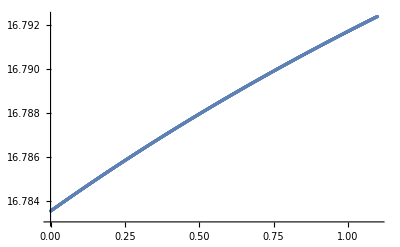

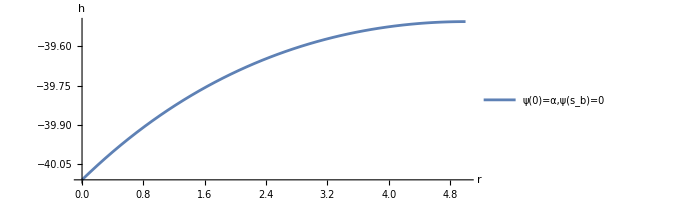

```mathematica
ListPlot[data,PlotRange->Full]
ParametricPlot[{First[rfB[sB]]*Lc,First[hfB[sB]/.ndsol]*Lc},{sB,0,sMax},AxesLabel->{"r","h"},PlotRange->Full,PlotLegends->{"ψ(0)=α,ψ(s_b)=0"}]
```

```mathematica
Export["gamma_vs_r2_R0_Ap_Kp_sb5nm_flat.csv",data]
```

gamma_vs_r2_R0_Ap_Kp_sb5nm_flat.csv

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["gamma_vs_r2_R0_Ap_Kp_sb5nm_flat.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["gamma_vs_r2_R0_Ap_Kp_sb5nm_flat.csv"]]]
```

```mathematica
Export["gamma_vs_Gm_R0_Ap_Kp_sb5nm_flat.csv",data]
```

gamma_vs_Gm_R0_Ap_Kp_sb5nm_flat.csv

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["gamma_vs_Gm_R0_Ap_Kp_sb5nm_flat.csv"]]]
```

InterpolatingFunction[…]

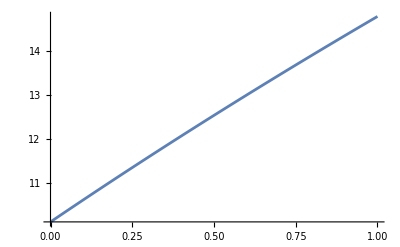

```mathematica
GammaGmPsi0=Import["C:\\Users\\avish\\OneDrive\\Documents\\USC_PhD\\Spring 2025\\Piezo_Arclength_Data\\gamma_vs_Gm_R0_Ap_Kp_sb5nm_flat.csv"];
Gm=Interpolation[GammaGmPsi0]
Plot[Gm[γ],{γ,0.0001,1},PlotRange->Full]
```

#### G as a function of γ in a finite compartment (sb=5nm) and with non-zero gradient at outer boundary in closed conformation

```mathematica
Rdome=41.82077878168754 (*1/2*)(*2*); (*Radius of curvature of the Piezo dome in units of nm, associated with raw and smoothed data*)
Scap=1.0 450 (*1/2*)(*2/3*);(*Membrane midplane area of the Piezo dome in units of nm^2*)
αB=ArcCos[1-Scap/(2 Pi Rdome^2)]; (*Fix Piezo dome-membrane contact angle*)
Kb=20; (*Lipid bilayer bending rigidity in units of Subscript[k, B] T*)
Clear[γ] (*Membrane tension in units of Subscript[k, B] T/nm^2*)
λ=(Kb/γ)^(1/2) ;(*Characteristic decay length of membrane shape deformations in units of nm*)
Lc=Rdome Sin[αB];(*Characteristic length used to obtain dimensionless equations*)

RdomeB=Rdome/Lc;
λB=λ/Lc;
```

```mathematica
sMax=5/Lc (*10*) (* λ/Lc*);

(*Reference values of shooting variables at γ = 0.01 k_B T/nm^2, Kb = 20 k_B T, Rdome = 41.82077878168754 nm:*)
(*pψfBs=-0.06293440963285328(*-0.063*);
prfBs=-0.013627638563264753(*-0.014*);*)

(*pψfBs=-0.0026847801542390403;(*For Rdome=15.020778781687616, γ=0.0001, Lc=λ, Scap=450*)
prfBs=-0.09438408558121254*Lc/Sqrt[Kb/0.0001];*)
prfBs=-7.09017*Lc/Sqrt[Kb/0.0001];(*For Rdome = 42 nm, γ = 0.0001, Lc = λ, sb = 5nm/Lc, ψfB[sb]=0*)
pψfBs=-1.11485;

Timing[data0=Reap[For[γ=(*0.01*)0.0001,(*γ≥0.00009*)γ≤1.1,γ=(*γ-0.0001*)γ+0.0005,

(*Adjust the dimensionless shooting variables so as to satisfy boundary conditions on ψ[s] and pr[s] at s = sb:*)
sols=FindRoot[shoot[sMax,pψfBi,prfBi]=={0.32,0},{pψfBi,pψfBs},{prfBi,prfBs}];

(*Use the values of the shooting variables determined in one interation as initial guesses for next iteration:*)
pψfBs=pψfBi/.sols;
prfBs=prfBi/.sols;

(*dummy=Evaluate[shoot[sMax,pψfBs,prfBs]]; Print[dummy];
(*To check that we indeed have ψfB[sB] = 0 and prfB[sB] = 0 at s = sbB*)*)

(*Assemble solution using the correct values of the shooting variables:*)
ndsol=SolveShapeEqs[sMax,pψfBs,prfBs];

(*(*Calculate bending energy in units of Subscript[k, B] T:*)
ψff[s_]=First[ψfB[s]/.ndsol];
rff[s_]=First[rfB[s]/.ndsol];
en=Kb π rff[s]((D[ψff[s],s]+Sin[ψff[s]]/rff[s])^2+2/λB^2(1-Cos[ψff[s]])); 
G=NIntegrate[en,{s,s0B,sMax}];

Sow[{γ,G}] (*Export data*); *)
Sow[{γ,First[rfB[sMax]/.ndsol]*Lc}];
(*Print[γ]*)
]];]

data=data0[[2]][[1]];
```

{26.6875,Null}

#### Gm as a function of β for finite s_b

```mathematica
Scap=1.0 450 (*1/2*)(*2/3*);(*Membrane midplane area of the Piezo dome in units of nm^2*)
Rdome=41.82077878168754 (*1/2*)(*2*); (*Radius of curvature of the Piezo dome in units of nm, associated with raw and smoothed data*)
αB=ArcCos[1-Scap/(2 Pi Rdome^2)]; (*Fix Piezo dome-membrane contact angle*)
Clear[β];
(*Lc=ri=Sqrt[Scap/π];*)
Kb=20; (*Lipid bilayer bending rigidity in units of Subscript[k, B] T*)
γ=0.5;(*Membrane tension in units of Subscript[k, B] T/nm^2*)
λ=(Kb/γ)^(1/2) ;(*Characteristic decay length of membrane shape deformations in units of nm*)
Lc=Rdome*Sin[αB];(*Characteristic length used to obtain dimensionless equations*)
(*Lc=λ;*)
(*riB=ri/Lc;*)
RdomeB=Rdome/Lc;
λB=λ/Lc;
```

```mathematica
sMax=80/Lc(*5*λB*);

(*Reference values of shooting variables at γ = 0.01 k_B T/nm^2, Kb = 20 k_B T, Rdome = 41.82077878168754 nm:*)
(*pψfBs=-0.06293440963285328(*-0.063*);
prfBs=-0.013627638563264753(*-0.014*);*)
(*Infinite compartment*)
(*prfBs=-0.005338267731682237;(*Rdome=42nm, γ=0.0001, Lc=λ, sb=10 λB, β=0, Scap=450*)
pψfBs=-0.07911618668138443;*)
(*prfBs=-0.042559208413802466;(*Rdome=42nm, γ=0.5, Lc=λ, sb=10 λB, β=0, Scap=450, Kb=20*)
pψfBs=-0.8589992441893428;*)
(*prfBs=-0.061454187225603585;(*Rdome=42nm, γ=1, Lc=λ, sb=10 λB, β=0, Scap=450, Kb=20*)
pψfBs=-1.2856802807528585;*)

(*prfBs=-0.12212504367809182;(*Rdome=41.82077878168754 nm, γ=0.5, Lc=λ, Kb=20, Scap=450, sb=5 nm*)
pψfBs=-1.3863582387063256;*)
(*prfBs=-0.10010918178645983;(*Rdome=41.82077878168754 nm, γ=1, Lc=λ, Kb=20, Scap=450, sb=5 nm*)
pψfBs=-1.634174411417485;*)
(*prfBs=-0.030140548096101002;(*Rdome=2 Subscript[R, 0], γ=0.5, Lc=λ, Kb=20, Scap=450, sb=5 nm*)
pψfBs=-0.6968623379284999;*)
(*prfBs=-0.4929072737018563;(*Rdome=Subscript[R, 0]/2, γ=0.5, Lc=λ, Kb=20, Scap=450, sb=5 nm*)
pψfBs-2.6536847174496305;*)
(*pψfBs=-0.0026847801542390403;(*For Rdome=15.020778781687616, γ=0.0001, Lc=λ, Scap=450*)
prfBs=-0.09438408558121254*Lc/Sqrt[Kb/0.0001];*)
(*prfBs=-12.137881353010519;(*Rdome=41.82077878168754 nm, γ=1*^-4, Lc=λ, Kb=20, Scap=450, sb=3 nm, β=0*)
pψfBs=-2.0087397262594147;*)
(*prfBs=-7.09017*Lc/Sqrt[Kb/0.0001];(*For Rdome=42 nm, γ=0.0001, Lc=λ, Kb=20, Scap=450, sb=5 nm, β=0*)
pψfBs=-1.11485;*)
(*prfBs=-512.6636373145604;(*Rdome=41.82077878168754 nm, γ=1*^-4, Lc=λ, Kb=20, Scap=450, sb=3 nm, β=-π/2*)
pψfBs=-15.769426972500778;*)
(*prfBs=-150.45715835263985;(*Rdome=41.82077878168754 nm, γ=1*^-4, Lc=λ, Kb=20, Scap=450, sb=10 nm, β=-π/2*)
pψfBs=-5.30586732314229;*)
(*prfBs=-14.660224820342123;(*Rdome=41.82077878168754 nm, γ=1, Lc=λ, Kb=20, Scap=450, sb=3 nm, β=-π/2*)
pψfBs=-15.237825770556698;*)
(*prfBs=-3.3611638633404683;(*Rdome=41.82077878168754 nm, γ=0.5, Lc=λ, Kb=20, Scap=450, sb=10 nm, β=0*)
pψfBs=-0.47482543696005286;*)
(*prfBs=-0.004281797587261707;(*Rdome=42nm, γ=1*^-4 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[α], sb=40nm*)
pψfBs=-0.06201089738701742;*)
(*prfBs=-0.042722133935570485;(*Rdome=42nm, γ=0.5 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[α], sb=20nm*)
pψfBs=-0.862220153582393;*)
(*prfBs=-0.04255780280600476;(*Rdome=42nm, γ=0.5 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[α], sb=40nm*)
pψfBs=-0.8589721478725089;*)
(*prfBs=-0.6253487330343569;(*Rdome=Subscript[R, 0]/2, γ=0.5 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[αB], sb=10nm*)
pψfBs=-1.7906345998146649;*)
(*prfBs=-0.03998298167868952;(*Rdome=2 Subscript[R, 0], γ=0.5 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[αB], sb=10nm*)
pψfBs=-0.47592483746738257;*)
(*prfBs=-0.03662051104364146;(*Rdome=2 Subscript[R, 0], γ=0.5 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[αB], sb=20nm*)
pψfBs=-0.4347041543672748;*)
(*prfBs=-0.5716485198094204;(*Rdome=Subscript[R, 0]/2, γ=0.5 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[αB], sb=20nm*)
pψfBs=-1.6296659525190518;*)
(*prfBs=-0.5694083472790459;(*Rdome=Subscript[R, 0]/2, γ=0.5 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[αB], sb=40nm*)
pψfBs=-1.6233429221939621;*)
(*prfBs=-0.03648029652950334;(*Rdome=2 Subscript[R, 0], γ=0.5 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[αB], sb=40nm*)
pψfBs=-0.43307837716181136;*)
(*prfBs=-0.06296972443818921;(*Rdome=42nm, γ=1, Lc=λ, Kb=20, Scap=450, sb=10 nm*)
pψfBs=-1.3180316779063612;*)
(*prfBs=-0.06147113404434905;(*Rdome=42nm, γ=1 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[α], sb=20nm*)
pψfBs=-1.2860276250989393;*)
(*prfBs=-0.06145416264381031;(*Rdome=42nm, γ=1 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[α], sb=40nm*)
pψfBs=-1.2856797874440211;*)
(*prfBs=-14.660224820342123;(*Rdome=open; γ=1*^-4; Lc=Sqrt[Scap/π],Kb=20,Scap=450,sb=7λB,β=-π/2*)
pψfBs=-15.237825770556698;*)
(*prfBs=-0.06292359832663419;(*Rdome=42nm,γ=0.0001 Subscript[k, B] T/nm^2,Scap=450 nm^2,Lc=RdomeSin[α],sb=5λB,β=-π/2*)
pψfBs=0.0035115598073522953;*)
(*prfBs=-0.19101576480798957;(*Rdome = 42nm, γ=0.5, Scap = 450, Lc=RdomeSin[αB],sb=5λB,β=-π/2*)
pψfBs=-0.8702873848031721;*)
(*prfBs=-0.2742278649951508;(*Rdome=42nm,γ=1,Scap=450,Lc=RdomeSin[αB],sb=5λB,β=-π/2*)
pψfBs=-1.3001846970180722;*)
(*prfBs=-0.06292359832663419;(*Rdome=42nm,γ=0.0001 Subscript[k, B] T/nm^2,Scap=450 nm^2,Lc=RdomeSin[α],sb=5λB*)
pψfBs=0.0035115598073522953;*)
(*prfBs=-0.011193022142760635;(*Rdome=42nm, γ=1*^-4 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[α], sb=20nm*)
pψfBs=-0.18187701329999983;*)
(*pψfBs=-0.2411439402439811;(*Rdome=42nm, γ=0.5 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[αB], sb=20nm, β=-2°*)
prfBs=-0.05339888993483363;*)
(*prfBs=-0.04773170860792694*Lc/Sqrt[Kb/0.0001];(*Rdome=20nm, γ=0.0001, Lc=λ, Scap=390, Kb=20*)
pψfBs=-0.0021322858270209828;*)
(*prfBs=-0.04773170860792694*Lc/Sqrt[Kb/0.0001];(*Rdome=20nm, γ=0.0001, Lc=λ, Scap=390, Kb=20*)
pψfBs=-0.0021322858270209828;*)
(*prfBs=-0.00791153699660939*Lc/(Rdome*Sin[αB]);(*Rdome=42nm, γ=1*^-4 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[αB], Subscript[s, b]=60nm*)
pψfBs=-0.031537260448121905;*)
(*prfBs=-0.004983587442175796*Lc/(Rdome*Sin[αB]);(*Rdome=42nm, γ=1*^-4 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[αB], Subscript[s, b]=80nm*)
pψfBs=-0.019273702988486033;*)
(*prfBs=-0.14646895060722487;(*Rdome=42nm, γ=0.5 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[αB], sb=60nm*)
pψfBs=-0.8589666960845027;*)
(*prfBs=-0.14646894887974285;(*Rdome=42nm, γ=0.5 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[αB], sb=80nm*)
pψfBs=-0.8589666865360124;*)
prfBs=-2.416865603461473*Lc/(Rdome*Sin[αB]);(*Rdome=42nm, γ=0.5 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[αB], sb=80nm, β=-π/2*)
pψfBs=-0.568575447554004;

Timing[data0=Reap[For[β=N[-π/2],(*γ≥0.00009*)β<=N[π/2],β=(*γ-0.0001*)β+0.001,

(*Adjust the dimensionless shooting variables so as to satisfy boundary conditions on ψ[s] and pr[s] at s = sb:*)
sols=FindRoot[shoot[sMax,pψfBi,prfBi]=={β,0},{pψfBi,pψfBs},{prfBi,prfBs}];

(*Use the values of the shooting variables determined in one interation as initial guesses for next iteration:*)
pψfBs=pψfBi/.sols;
prfBs=prfBi/.sols;

dummy=Evaluate[shoot[sMax,pψfBs,prfBs]]; Print[β,dummy];
(*To check that we indeed have ψfB[sB] = 0 and prfB[sB] = 0 at s = sbB*)

(*Assemble solution using the correct values of the shooting variables:*)
ndsol=SolveShapeEqs[sMax,pψfBs,prfBs];

(*Calculate bending energy in units of Subscript[k, B] T:*)
ψff[s_]=First[ψfB[s]/.ndsol];
rff[s_]=First[rfB[s]/.ndsol];
en=Kb π rff[s]((D[ψff[s],s]+Sin[ψff[s]]/rff[s])^2+2/λB^2(1-Cos[ψff[s]])); 
Gm=NIntegrate[en,{s,s0B,sMax}];

Sow[{β,Gm}] (*Export data*); 
(*Sow[{γ,First[rfB[sMax]/.ndsol]*Lc}];*)
(*Print[β]*)
(*Sow[{β,pψfBs,prfBs}]*)
]];]

data=data0[[2]][[1]];
```

{7409.14,Null}

```mathematica
Print[γ]
```

0.0001

```mathematica
data[[-1]]
```

{1.5702,1679.41}

```mathematica
Export["beta_vs_Gm_RpR0_gamma0.5_sb60.csv",data]
```

beta_vs_Gm_RpR0_gamma0.5_sb60.csv

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["beta_vs_Gm_RpR0_gamma0.5_sb60.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["beta_vs_Gm_Rpflat_gamma0.0001_sb80.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["beta_vs_Gm_Rpflat_gamma0.0001_sb60.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["beta_vs_Gm_Rpflat_gamma0.5_sb60.csv"]]]
```

```mathematica
Print[N[-0.0349*180/π]]
```

-1.99962

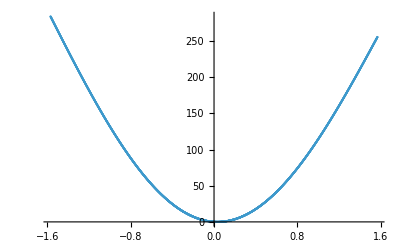

```mathematica
ListPlot[data,PlotRange->Full]
```

```mathematica
Export["beta_vs_Gm_RpR0times2_gamma0.0001_sb40.csv",data]
```

beta_vs_Gm_RpR0times2_gamma0.0001_sb40.csv

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["beta_vs_Gm_RpR0times2_gamma0.0001_sb40.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["beta_vs_Gm_RpR0by2_gamma0.0001_sb40.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["beta_vs_Gm_RpR0times2_gamma0.0001_sb20.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["beta_vs_Gm_RpR0by2_gamma0.0001_sb20.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["beta_vs_Gm_RpR0times2_gamma0.0001_sb10.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["beta_vs_Gm_RpR0by2_gamma0.0001_sb10.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["beta_vs_Gm_RpR0times2_gamma0.0001_sb5.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["beta_vs_Gm_RpR0by2_gamma0.0001_sb5.csv"]]]
```

```mathematica
Export["C:\\Users\\avish\\OneDrive\\Documents\\USC_PhD\\Spring 2025\\Piezo_Arclength_Data\\Datasets_for_paper_Topic1\\Po_vs_beta\\beta_vs_Gm(Rp_gamma_sb)\\beta_vs_Gm_Rpflat_gamma1_sb20_v1.csv",data]
```

C:\Users\avish\OneDrive\Documents\USC_PhD\Spring 2025\Piezo_Arclength_Data\Datasets_for_paper_Topic1\Po_vs_beta\beta_vs_Gm(Rp_gamma_sb)\beta_vs_Gm_Rpflat_gamma1_sb20_v1.csv

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["C:\\Users\\avish\\OneDrive\\Documents\\USC_PhD\\Spring 2025\\Piezo_Arclength_Data\\Datasets_for_paper_Topic1\\beta_vs_Gm_RpR0by2_gamma0.5_sb10.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["C:\\Users\\avish\\OneDrive\\Documents\\USC_PhD\\Spring 2025\\Piezo_Arclength_Data\\Datasets_for_paper_Topic1\\Po_vs_beta\\beta_vs_Gm(Rp_gamma_sb)\\beta_vs_Gm_RpR0_gamma0.0001_sb40.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["C:\\Users\\avish\\OneDrive\\Documents\\USC_PhD\\Spring 2025\\Piezo_Arclength_Data\\Datasets_for_paper_Topic1\\Po_vs_beta\\beta_vs_Gm(Rp_gamma_sb)\\beta_vs_Gm_RpR0_gamma1_sb20.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["C:\\Users\\avish\\OneDrive\\Documents\\USC_PhD\\Spring 2025\\Piezo_Arclength_Data\\Datasets_for_paper_Topic1\\Po_vs_beta\\beta_vs_Gm(Rp_gamma_sb)\\beta_vs_Gm_RpR0_gamma0.5_sb20.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["beta_vs_Gm_RpR0_gamma0.0001_sb20.csv"]]]
```

```mathematica
Export["beta_vs_Gm_Rpflat_gamma1_asymp.csv",data]
```

beta_vs_Gm_Rpflat_gamma1_asymp.csv

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["beta_vs_Gm_Rpflat_gamma0.0001_sb5.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["beta_vs_Gm_Rpflat_gamma0.0001_sb3.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["beta_vs_Gm_RpR0_gamma0.0001_sb10.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["beta_vs_Gm_RpR0_gamma0.0001_sb3.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["beta_vs_Gm_RpR0_gamma1_sb3.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["beta_vs_Gm_RpR0_gamma1_sb3.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["beta_vs_Gm_RpR0_gamma1_sb3.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["beta_vs_Gm_RpR0_gamma0.0001_sb10.csv"]]]
```

#### Solving Hamilton’s equations in open configuration

```mathematica
(*Solution of the Hamilton equations in dimensionless form as a function of sbB and the shooting variables:*)
s0B=0;
SolveShapeEqs[sbB_,pψfBi_,prfBi_]:=NDSolve[
{ψfB'[sB]==1/(2 rfB[sB]) (pψfB[sB]-2 Sin[ψfB[sB]]),rfB'[sB]==Cos[ψfB[sB]],hfB'[sB]==Sin[ψfB[sB]],pψfB'[sB]==(pψfB[sB]/rfB[sB]- phfB[sB]) Cos[ψfB[sB]]+((2 rfB[sB])/λB^2+prfB[sB]) Sin[ψfB[sB]],prfB'[sB]==pψfB[sB]/(4 rfB[sB]^2)(pψfB[sB]-4 Sin[ψfB[sB]])+2/λB^2 (1-Cos[ψfB[sB]]),phfB'[sB]==0,
(*Initial conditions:*)
ψfB[s0B]==0,
rfB[s0B]==(*Sqrt[Scap/π*(1-Scap/(4π*Rdome^2))]/Lc,*)Sqrt[Scap/π]/Lc,
hfB[s0B]==0,
pψfB[s0B]==pψfBi,
prfB[s0B]==prfBi,
phfB[s0B]==0
},{ψfB,rfB,hfB,pψfB,prfB,phfB},{sB,s0B,sbB},Method->"ImplicitRungeKutta"];
```

```mathematica
(*Solve the Hamilton equations in dimensionless form as a function of the shooting variables, and output the boundary values of ψfB[sB] and prfB[sB] at s = sbB (these are the boundary values used to satisfy the boundary conditions at s = sbB):*)
shoot[sbB_?NumberQ,pψfBi_?NumberQ,prfBi_?NumberQ]:=First[{ψfB[sbB],prfB[sbB]}/.SolveShapeEqs[sbB,pψfBi,prfBi]];
(*Use here ?NumberQ to indicate that sbB, pψfB0, and prfB0 are numbers; This is needed for the FindRoot[] comand (see below) to work with shoot[].*)
```

```mathematica
(*Rdome=41.82077878168754 (*1/2*)(*2*); (*Radius of curvature of the Piezo dome in units of nm, associated with raw and smoothed data*)
αB=ArcCos[1-Scap/(2 Pi Rdome^2)]; (*Fix Piezo dome-membrane contact angle*)*)
Scap=1.0 450 (*1/2*)(*2/3*);(*Membrane midplane area of the Piezo dome in units of nm^2*)
ri=Sqrt[Scap/π];
Kb=20; (*Lipid bilayer bending rigidity in units of Subscript[k, B] T*)
Clear[γ] (*Membrane tension in units of Subscript[k, B] T/nm^2*)
λ=(Kb/γ)^(1/2) ;(*Characteristic decay length of membrane shape deformations in units of nm*)
(*Lc=Rdome Sin[αB];(*Characteristic length used to obtain dimensionless equations*)*)
Lc=ri;
riB=ri/Lc;
(*RdomeB=Rdome/Lc;*)
λB=λ/Lc;
```

```mathematica
Clear[γ]
sMax=40/Lc (*10*) (*λ/Lc*);

(*Reference values of shooting variables at γ = 0.01 k_B T/nm^2, Kb = 20 k_B T, Rdome = 41.82077878168754 nm:*)
(*pψfBs=-0.06293440963285328(*-0.063*);
prfBs=-0.013627638563264753(*-0.014*);*)
(*prfBs=-0.011193022142760635;(*Rdome=42nm, γ=1*^-4 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[α], sb=20nm*)
pψfBs=-0.18187701329999983;*)
(*prfBs=-0.004281797587261707;(*Rdome=42nm, γ=1*^-4 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[α], sb=40nm*)
pψfBs=-0.06201089738701742;*)
(*pψfBs=-0.0026847801542390403;(*For Rdome=15.020778781687616, γ=0.0001, Lc=λ, Scap=450*)
prfBs=-0.09438408558121254*Lc/Sqrt[Kb/0.0001];*)
(*prfBs=-7.09017*Lc/Sqrt[Kb/0.0001];(*For Rdome = 42 nm, γ = 0.0001, Lc = λ, sb = 5nm/Lc, ψfB[sb]=0*)
pψfBs=0;*)
prfBs=-0.004281797587261707*Lc/(42*Sin[ArcCos[1-Scap/(2π*42^2)]]);(*Rdome=42nm, γ=1*^-4 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[α], sb=20nm*)
pψfBs=0;

Timing[data0=Reap[For[γ=(*0.01*)0.0001,(*γ≥0.00009*)γ≤1.1,γ=(*γ-0.0001*)γ+0.0005,

(*Adjust the dimensionless shooting variables so as to satisfy boundary conditions on ψ[s] and pr[s] at s = sb:*)
sols=FindRoot[shoot[sMax,pψfBi,prfBi]=={0,0},{pψfBi,pψfBs},{prfBi,prfBs}];

(*Use the values of the shooting variables determined in one interation as initial guesses for next iteration:*)
pψfBs=pψfBi/.sols;
prfBs=prfBi/.sols;

dummy=Evaluate[shoot[sMax,pψfBs,prfBs]]; Print[γ,dummy];
(*To check that we indeed have ψfB[sB] = 0 and prfB[sB] = 0 at s = sbB*)

(*Assemble solution using the correct values of the shooting variables:*)
ndsol=SolveShapeEqs[sMax,pψfBs,prfBs];

(*Calculate bending energy in units of Subscript[k, B] T:*)
ψff[s_]=First[ψfB[s]/.ndsol];
rff[s_]=First[rfB[s]/.ndsol];
en=Kb π rff[s]((D[ψff[s],s]+Sin[ψff[s]]/rff[s])^2+2/λB^2(1-Cos[ψff[s]])); 
G=NIntegrate[en,{s,s0B,sMax}];

Sow[{γ,G}] (*Export data*); 
(*Sow[{γ,First[rfB[sMax]/.ndsol]*Lc}]*)
(*Print[γ]*)
]];]

data=data0[[2]][[1]];
```

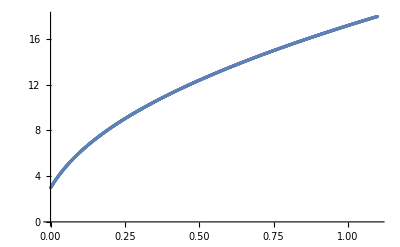

```mathematica
ListPlot[data]
```

```mathematica
Export["C:\\Users\\avish\\OneDrive\\Documents\\USC_PhD\\Spring 2025\\Piezo_Arclength_Data\\Datasets_for_paper_Topic1\\Po_vs_gamma\\gamma_vs_Gm_gating(R0_beta_sb)\\gamma_vs_Gm_Rpflat_beta0.15_sb40.csv",data]
```

C:\Users\avish\OneDrive\Documents\USC_PhD\Spring 2025\Piezo_Arclength_Data\Datasets_for_paper_Topic1\Po_vs_gamma\gamma_vs_Gm_gating(R0_beta_sb)\gamma_vs_Gm_Rpflat_beta0.15_sb40.csv

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["gamma_vs_Gm_Rpflat_beta0.1_sb20.csv"]]]
```

```mathematica
Export["gamma_vs_Gm_R0_Ap_Kp_sb5nm_psifB(sb)-1_open.csv",data]
```

gamma_vs_Gm_R0_Ap_Kp_sb5nm_psifB(sb)-1_open.csv

#### Iterating over Scap

```mathematica
Rdome=15;
Kb=20;
Clear[Scap];
γ=0.0001;
λ=Sqrt[Kb/γ];
Lc=λ;
αB=ArcCos[1-Scap/(2π*Rdome^2)];
RdomeB=Rdome/Lc;
```

```mathematica
sMax=5/Lc;
prfBs=-58.13857966389962;(*For Rdome=15nm, γ=0.0001, Lc=λ, sb = 5nm/Lc, β=0, Scap=450*)
pψfBs=-2.8446386178637764;
Timing[data0=Reap[For[Scap=450,Scap>=390,Scap=Scap-1,

(*Adjust the dimensionless shooting variables so as to satisfy boundary conditions on ψ[s] and pr[s] at s = sb:*)
αB=ArcCos[1-(Scap)/(2 *π *Rdome^2)];
sols=FindRoot[shoot[sMax,pψfBi,prfBi]=={0,0},{pψfBi,pψfBs},{prfBi,prfBs}];

(*Use the values of the shooting variables determined in one interation as initial guesses for next iteration:*)
pψfBs=pψfBi/.sols;
prfBs=prfBi/.sols;

(*dummy=Evaluate[shoot[sMax,pψfBs,prfBs]]; Print[dummy];
(*To check that we indeed have ψfB[sB] = 0 and prfB[sB] = 0 at s = sbB*)*)

(*Assemble solution using the correct values of the shooting variables:*)
ndsol=SolveShapeEqs[sMax,pψfBs,prfBs];

(*(*Calculate bending energy in units of Subscript[k, B] T:*)
ψff[s_]=First[ψfB[s]/.ndsol];
rff[s_]=First[rfB[s]/.ndsol];
en=Kb π rff[s]((D[ψff[s],s]+Sin[ψff[s]]/rff[s])^2+2/λB^2(1-Cos[ψff[s]])); 
Gm=NIntegrate[en,{s,s0B,sMax}];
(*hff=First[hfB[sMax]/.ndsol];*)
Sow[{N[RdomeB*Lc],rff[sMax]*Lc,Gm}] (*Export data*); *)
Sow[{Scap,prfBs,pψfBs}]
]];]

data=data0[[2]][[1]];
```

{1.01563,Null}

```mathematica
data[[-1]]
```

{390,-49.8022,-2.46436}

```mathematica
Rdome=41.82077878168754/2;
Scap=450;
a=Tan[ArcCos[1-Scap/(2π*Rdome^2)]];
r1=Sqrt[Scap/π(1-Scap/(4π*Rdome^2))];
r2=15;
s=Integrate[Sqrt[1+(a*r1/r)^2],{r,r1,r2}];
β=ArcTan[a*r1/r2];
Print[r1]
Print[s]
Print[β]
```

11.4677

4.07112

0.464771

```mathematica
R0=41.82077878168754;
N[{0.443425,0.206519,0.1015,0.160452}*180/π]
N[{ArcCos[1-225/(π*(R0/2)^2)],ArcCos[1-225/(π*R0^2)],ArcCos[1-225/(π*(2*R0)^2)]}*180/π]
```

{25.4064,11.8327,5.81552,9.19322}

{33.2588,16.4534,8.20546}

```mathematica
Sqrt[20/0.00001]*5
```

7071.07

### G as a function of R_P

Here, we’re iterating over different values of R_P. Therefore, a better choice of length scale for the problem would be the decay length λ.

```mathematica
(*Rdome=41.82077878168754(*1/2*)(*2*); (*Radius of curvature of the Piezo dome in units of nm, associated with raw and smoothed data*)*)
Clear[Rdome];
Scap=1.0 450 (*1/2*)(*2/3*);(*Membrane midplane area of the Piezo dome in units of nm^2*)
αB=ArcCos[1-Scap/(2 Pi Rdome^2)]; (*Fix Piezo dome-membrane contact angle*)
Kb=20; (*Lipid bilayer bending rigidity in units of Subscript[k, B] T*)
γ=0.0001; (*Membrane tension in units of Subscript[k, B] T/nm^2*)
λ=(Kb/γ)^(1/2) ;(*Characteristic decay length of membrane shape deformations in units of nm*)
Lc=Rdome*Sin[αB];(*Characteristic length used to obtain dimensionless equations*)
(*r2=15;(*For Catenoidal comparison*)*)
(*r1=Sqrt[Scap/π*(1-Scap/(4π*Rdome^2))];*)
RdomeB=Rdome/Lc;
(*catenoid[sb_]:=FindRoot[NIntegrate[Sqrt[1+((Tan[αB]*r1)/r)^2],{r,r1,r2}]-sb,{r2,20}]*)
λB=λ/Lc;
```

```mathematica
Clear[Rdome];
(*Clear[αB];*)
(*αB=ArcCos[1-Scap/(2π*RdomeB^2*Lc^2)];*)
(*r1=Sqrt[Scap/π*(1-Scap/(4π*RdomeB^2))]*)
(*sMax=5/Lc;*)
(*sMax=Integrate[Sqrt[1+(Tan[αB]*r1/r)^2],{r,Sqrt[Scap/π*(1-Scap/(4π*Lc^2*RdomeB^2))],r2}]/Lc;*)
(*prfBs=-0.013862379662330653;(*At Rdome=42nm,γ=0.0001 Subscript[k, B] T/nm^2,Scap=450,Lc=λ,Kb=20*)
pψfBs=-0.0014491702075504717;*)
sMax=5/Lc;

(*Reference values of shooting variables at γ = 0.01 k_B T/nm^2, Kb = 20 k_B T, Rdome = 41.82077878168754 nm:*)
(*pψfBs=-0.06293440963285328(*-0.063*);
prfBs=-0.013627638563264753(*-0.014*);*)
(*prfBs=-0.12212504367809182;(*Rdome=41.82077878168754 nm, γ=0.5, Lc=λ, Kb=20, Scap=450, sb=5 nm*)
pψfBs=-1.3863582387063256;*)
(*prfBs=-0.12212504367809182;(*Rdome=41.82077878168754 nm, γ=0.5, Lc=λ, Kb=20, Scap=450, sb=5 nm*)
pψfBs=-1.3863582387063256;*)
(*prfBs=-1.2556527712579473;(*Rdome=10nm,γ=0.001,Lc=γ,sb=8.36263nm,β=0,Scap=450*)
-0.5747516686830932;*)
(*prfBs=25.75374958940016;(*Rdome=10nm, γ=0.0001, Lc=λ, sb=8.36263nm, Scap=450*)
pψfBs=1.146468674873994;*)
(*prfBs=-4.108436527829742;(*Rdome=42nm, γ=0.0001, Lc=λ, sb=8.36263nm, β=0, Scap=450*)
pψfBs=-0.597554489955383;*)
(*prfBs=-113.92832616214437;(*Rdome=10.2nm, γ=0.0001, Lc=λ, sb=5nm/Lc, β=0, Scap=390, Kb=20*)
pψfBs=-3.1638807366783825;*)
(*prfBs=-49.802230157602764;(*Rdome=15nm, γ=0.0001, Lc=λ, sb = 5nm/Lc, β=0, Scap=390*) 
pψfBs=-2.4643555703375872;*)
(*prfBs=-0.013862379662330653;(*At Rdome=42nm,γ=0.0001 Subscript[k, B] T/nm^2,Scap=450,Lc=λ*)
pψfBs=-0.0014491702075504717;*)
(*pψfBs = -0.0024518801724742446; (*At Rdome = 20.9207787816876, γ = 0.0001, Scap = 450, Lc = λ*)
prfBs = -0.05270285422469911*Lc/λ;*)
(*pψfBs=-0.02001644196907279;(*Rp=15,γ=0.001,Lc=RdomeSin[αB],Scap=450*)
prfBs=-0.016006020754444083;*)
(*prfBs=-7.09017(*For Rdome = 42 nm, γ = 0.0001, Lc = λ, sb = 5nm/Lc, β=0, Scap=450*)
pψfBs=-1.11485*)
(*prfBs=-58.13857966389962;(*For Rdome=15nm, γ=0.0001, Lc=λ, sb = 5nm/Lc, β=0, Scap=450*)
pψfBs=-2.8446386178637764;*)
(*pψfBs=-0.0026847801542390403;(*For Rdome=15.020778781687616, γ=0.0001, Lc=λ, Scap=450*)
prfBs=-0.09438408558121254;*)
(*prfBs=-0.00011104983460904045;(*Rdome = 199nm, γ=0.001, Lc=Rdome Sin[αB]*)
pψfBs=-0.0022533960244748973;*)
(*prfBs=-0.20625722293890872;(*Rdome = 15, γ=0.001, Lc=λ*)
pψfBs=-0.020016450308550423;*)
(*pψfBs = -0.0007573743166639671; (*At Rdome = 83.72077878168916, γ = 0.0001, Scap = 450, Lc = λ*)
prfBs = -0.003545399972874482;*)
(*pψfBs=-0.13374640636641394;(*At Rdome = 15, γ = 0.01, Scap = 450, Lc = RdomeSin[αB]*)
prfBs=-0.09386430883001758;*)
(*pψfBs=-0.7395226433114312;(*At Rdome = 15, γ = 0.1, Scap = 450, Lc = RdomeSin[αB]*)
prfBs=-0.4318175431731134;*)
(*pψfBs=-3.201926506374947;(*At Rdome = 15, γ = 1, Scap = 450, Lc = RdomeSin[αB]*)
prfBs=-1.5726710585722292;*)
(*pψfBs=-3.201926506374947;(*At Rdome = 15, γ = 1, Scap = 450, Lc = RdomeSin[αB]*)
prfBs=-1.5726710585722292*Lc/(Rdome*Sin[ArcCos[1-Scap/(2π*Rdome^2)]]);*)
(*prfBs=-0.0006283880508549116;(*Rdome = 199nm, γ=0.0001, Lc=λ*)
pψfBs=-0.0003217377869996564;*)
(*prfBs=-0.16199996730878755;(*Rdome = 10.2nm, γ=0.0001, Lc=λ*)
pψfBs=-0.0018310328584764197;*)
(*prfBs=-0.1257739159081641;(*Rdome=11.2nm, γ=0.0001, Lc=λ, Scap=390, Kb=20*)
pψfBs=-0.0021256213359914134;*)
(*prfBs=-0.04773170860792694;(*Rdome=20nm, γ=0.0001, Lc=λ, Scap=390, Kb=20*)
pψfBs=-0.0021322858270209828;*)
(*prfBs=-49.802230157602764;(*Rdome=15nm, γ=0.0001, Lc=λ, sb = 5nm/Lc, β=0, Scap=390*)
pψfBs=-2.4643555703375872;*)
(*prfBs=-0.030140548096101002;(*Rdome=2 Subscript[R, 0], γ=0.5, Lc=λ, Kb=20, Scap=450, sb=5 nm*)
pψfBs=-0.6968623379284999;*)
(*prfBs=-0.4929072737018563;(*Rdome=Subscript[R, 0]/2, γ=0.5, Lc=λ, Kb=20, Scap=450, sb=5 nm*)
pψfBs-2.6536847174496305;*)
(*prfBs=-0.08574863537564927;(*Rdome=41.82077878168754 nm, γ=0.5, Lc=λ, Kb=20, Scap=450, sb=10 nm *)
pψfBs=-0.9446325621940705;*)
(*prfBs=-0.042722133935570485;(*Rdome=42nm, Lc=Rdome*Sin[α], γ=0.5 Subscript[k, B] T/nm^2, sb=20nm*)
pψfBs=-0.862220153582393;*)
(*prfBs=-0.04255780280600476;(*Rdome=42nm, Lc=Rdome*Sin[α], γ=0.5 Subscript[k, B] T/nm^2, sb=40nm*)
pψfBs=-0.8589721478725089;*)
(*prfBs=-0.6253487330343569;(*Rdome=Subscript[R, 0]/2, γ=0.5 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[αB], sb=10nm*)
pψfBs=-1.7906345998146649;*)
(*prfBs=-0.03998298167868952;(*Rdome=2 Subscript[R, 0], γ=0.5 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[αB], sb=10nm*)
pψfBs=-0.47592483746738257;*)
(*prfBs=-0.03662051104364146;(*Rdome=2 Subscript[R, 0], γ=0.5 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[αB], sb=20nm*)
pψfBs=-0.4347041543672748;*)
(*prfBs=-0.5716485198094204;(*Rdome=Subscript[R, 0]/2, γ=0.5 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[αB], sb=20nm*)
pψfBs=-1.6296659525190518;*)
(*prfBs=-0.5694083472790459;(*Rdome=Subscript[R, 0]/2, γ=0.5 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[αB], sb=40nm*)
pψfBs=-1.6233429221939621;*)
(*prfBs=-0.03648029652950334;(*Rdome=2 Subscript[R, 0], γ=0.5 Subscript[k, B] T/nm^2, Lc=Rdome*Sin[αB], sb=40nm*)
pψfBs=-0.43307837716181136;*)
prfBs=-0.04255780280600476;(*Rdome=42nm, Lc=Rdome*Sin[α], γ=0.5 Subscript[k, B] T/nm^2, sb=40nm*)
pψfBs=-0.8589721478725089;
Timing[data0=Reap[For[Rdome=42,Rdome<=84,Rdome=Rdome+0.05,
RdomeB=Rdome/Lc;
(*Adjust the dimensionless shooting variables so as to satisfy boundary conditions on ψ[s] and pr[s] at s = sb:*)
αB=ArcCos[1-Scap/(2π*Rdome^2)];
(*r1=Sqrt[(Scap/π)*(1-Scap/(4π*Rdome^2))];*)
(*Matching the catenoid's r2 for a fixed sb and varying β*)
(*cat=catenoid[10];*)
(*r2s=r2/.cat;*)
(*sols=FindRoot[shoot[sMax,pψfBi,prfBi]=={ArcTan[(Tan[αB]*r1)/r2s],0},{pψfBi,pψfBs},{prfBi,prfBs}];*)
sols=FindRoot[shoot[sMax,pψfBi,prfBi]=={0,0},{pψfBi,pψfBs},{prfBi,prfBs}];

(*Use the values of the shooting variables determined in one interation as initial guesses for next iteration:*)
pψfBs=pψfBi/.sols;
prfBs=prfBi/.sols;

dummy=Evaluate[shoot[sMax,pψfBs,prfBs]]; Print[Rdome,dummy];
(*To check that we indeed have ψfB[sB] = 0 and prfB[sB] = 0 at s = sbB*)

(*Assemble solution using the correct values of the shooting variables:*)
ndsol=SolveShapeEqs[sMax,pψfBs,prfBs];

(*(*Calculate bending energy in units of Subscript[k, B] T:*)
ψff[s_]=First[ψfB[s]/.ndsol];
rff[s_]=First[rfB[s]/.ndsol];
en=Kb π rff[s]((D[ψff[s],s]+Sin[ψff[s]]/rff[s])^2+2/λB^2(1-Cos[ψff[s]])); 
(*encat=Kb π rff[s](D[ψff[s],s]+Sin[ψff[s]]/rff[s])^2;*)
Gm=NIntegrate[en,{s,s0B,sMax}];
(*Gmcat=NIntegrate[encat,{s,s0B,sMax}];*)
(*hff=First[hfB[sMax]/.ndsol];*)
(*Sow[{N[RdomeB*Lc],rff[sMax]*Lc,Gm}] (*Export data*); *)
(*Sow[{N[RdomeB*Lc],prfBs,pψfBs}];*)
(*Sow[{Rdome,Gm}];*)*)
Sow[{N[RdomeB*Lc],prfBs,pψfBs}];
]];]

data=data0[[2]][[1]];
```

{18.0313,Null}

```mathematica
Print[data[[-1]]]
```

{84.,-0.0364803,-0.433078}

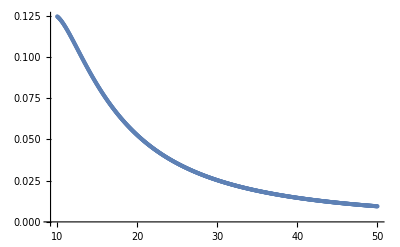

```mathematica
ListPlot[data,PlotRange->All]
```

```mathematica
Export["R_vs_Gm_catenoid_asymp.csv",data]
```

R_vs_Gm_catenoid_asymp.csv

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["R_vs_Gm_catenoid_asymp.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["R_vs_Gm_catenoid_sb10.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["R_vs_Gm_catenoid_sb5.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["SmallRp_vs_Gm_gamma0.0001_r2_15nm_sbUpdated._betaUpdated.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Rp_vs_Gm_gamma0.001_r2_15nm_sbUpdated._betaUpdated.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Rp_vs_Gm_gamma0.0001_r2_15nm_sbUpdated._betaUpdated.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Rp_vs_Gm_gamma1_sb5_flat.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Rp_vs_r2_vs_Gm_gamma1_sb5_beta0.1.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Rp_vs_r2_vs_Gm_gamma0.1_sb5_flat.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Rp_vs_r2_vs_Gm_gamma0.1_sb5_beta0.001.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Rp_vs_r2_vs_Gm_gamma0.1_sb5_beta0.01.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Rp_vs_r2_vs_Gm_gamma0.1_sb5_beta0.1.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Rp_vs_r2_vs_Gm_gamma0.1_sb5_beta1.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Rp_vs_r2_vs_Gm_gamma0.01_sb5_beta1.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Rp_vs_r2_vs_Gm_gamma0.01_sb5_beta0.1.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Rp_vs_r2_vs_Gm_gamma0.01_sb5_beta0.01.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Rp_vs_r2_vs_Gm_gamma0.01_sb5_beta0.001.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Rp_vs_Gm_gamma0.01_sb5_flat.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Rp_vs_Gm_gamma0.01_sb5_flat.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Rp_vs_Gm_gamma0.001_sb5_flat.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Rp_vs_r2_vs_Gm_gamma0.001_sb5_beta0.001.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Rp_vs_r2_vs_Gm_gamma0.001_sb5_beta0.01.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Rp_vs_r2_vs_Gm_gamma0.001_sb5_beta0.1.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Rp_vs_r2_vs_Gm_gamma0.001_sb5_beta1.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Rp_vs_r2_vs_Gm_gamma0.0001_sb5_beta1.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Rp_vs_r2_vs_Gm_gamma0.0001_sb5_beta0.1.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Rp_vs_r2_vs_Gm_gamma0.0001_sb5_beta0.01.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Rp_vs_r2_vs_Gm_gamma0.0001_sb5_beta0.001.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Rp_vs_r2_vs_Gm_gamma0.0001_sb5_beta0.001.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Rp_vs_r2_vs_Gm_gamma0.0001_sb5_beta0.01.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Rp_vs_Gm_0.0001_sb5_beta_0.01.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Rp_vs_Gm_0.0001_sb5_beta_0.001.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Rp_vs_Gm_0.0001_sb5_flat.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Rp_Gm_0.001_asymp.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Rp_Gm_0.0001_asymp.csv"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Rp_Gm_1.csv"]]]
```

```mathematica
RpGm=Import["C:\\Users\\avish\\OneDrive\\Documents\\USC_PhD\\Fall 2024\\Piezo_Arclength_data\\Rp_Gm_0.1.csv"]
Subscript[Gm, 1e-1]=Interpolation[RpGm]
```

{{15.,20.2051},{16.,18.0282},{17.,16.1645},{18.,14.562},{19.,13.1775},{20.,11.9751},{21.,10.9256},{22.,10.0049},{23.,9.19358},{24.,8.47525},{25.,7.83657},{26.,7.26641},{27.,6.75546},{28.,6.29592},{29.,5.88121},{30.,5.50575},{31.,5.1648},{32.,4.8543},{33.,4.57075},{34.,4.31116},{35.,4.07292},{36.,3.85376},{37.,3.65173},{38.,3.46508},{39.,3.29231},{40.,3.13208},{41.,2.98321},{42.,2.84466},{43.,2.7155},{44.,2.59491},{45.,2.48214},{46.,2.37654},{47.,2.27751},{48.,2.18453},{49.,2.09711},{50.,2.01481},{51.,1.93726},{52.,1.86408},{53.,1.79496},{54.,1.7296},{55.,1.66775},{56.,1.60914},{57.,1.55356},{58.,1.50081},{59.,1.45069},{60.,1.40303},{61.,1.35769},{62.,1.3145},{63.,1.27333},{64.,1.23407},{65.,1.19659},{66.,1.16079},{67.,1.12657},{68.,1.09384},{69.,1.06251},{70.,1.03251},{71.,1.00375},{72.,0.976185},{73.,0.949735},{74.,0.924344},{75.,0.899956},{76.,0.87652},{77.,0.853986},{78.,0.832309},{79.,0.811446},{80.,0.791357},{81.,0.772004},{82.,0.753352},{83.,0.735367},{84.,0.718017},{85.,0.701274},{86.,0.685109},{87.,0.669496},{88.,0.65441},{89.,0.639828},{90.,0.625727},{91.,0.612088},{92.,0.598888},{93.,0.586111},{94.,0.573739},{95.,0.561753},{96.,0.550139},{97.,0.538881},{98.,0.527965},{99.,0.517377},{100.,0.507104},{101.,0.497134},{102.,0.487455},{103.,0.478055},{104.,0.468925},{105.,0.460053},{106.,0.451431},{107.,0.443049},{108.,0.434898},{109.,0.42697},{110.,0.419256},{111.,0.41175},{112.,0.404443},{113.,0.397328},{114.,0.3904},{115.,0.383652},{116.,0.377076},{117.,0.370668},{118.,0.364423},{119.,0.358333},{120.,0.352395},{121.,0.346603}}

InterpolatingFunction[…]

```mathematica
data[[-1]]
```

{15.0208,0.819523,0.708086,-0.00268478,-0.00447703,0.082817}

```mathematica
(*pψfBs = -0.00268478142660031;(*For Rdome = 15.02077878168762, γ = 0.0001, Lc = √Scap, Scap = 450*)
prfBs = -0.004477032327309477;*)
(*pψfBs=-0.0026847801542390403;(*For Rdome=15.020778781687616,γ=0.0001,Lc=λ,Scap=450*)
prfBs=-0.09438408558121254;*)
```

```mathematica
Export["Rp_psiB0_rfB0_hfB0_hfB(sMax)_pPsifB(sMax)_prfB(sMax)_Gm_0.01gamma.txt",data]
```

Rp_psiB0_rfB0_hfB0_hfB(sMax)_pPsifB(sMax)_prfB(sMax)_Gm_0.01gamma.txt

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Rp_psiB0_rfB0_hfB0_hfB(sMax)_pPsifB(sMax)_prfB(sMax)_Gm_0.01gamma.txt"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Rp_rfB0_hfB0_Gm_0.01gamma.txt"]]]
```

```mathematica
(*Print[data0]
Print[data]*)
```

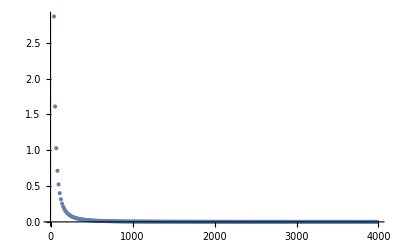

```mathematica
ListPlot[data,PlotRange->All,PlotLegends->{"γ=0.1k_BT/nm^2"}]
```

### G as a function of R_P for γ = 0.01, 0.1, and 1

```mathematica
Scap=1.0 450 (*1/2*)(*2/3*);(*Membrane midplane area of the Piezo dome in units of nm^2*)
(*αB=ArcCos[1-Scap/(2 Pi Rdome^2)]; (*Fix Piezo dome-membrane contact angle*)*)
Kb=20; (*Lipid bilayer bending rigidity in units of Subscript[k, B] T*)
(*pψfBs=-0.063;
prfBs=-0.014;*)

Timing[
data1=Reap[For[γ=0.01,γ<=1,γ=γ*10,
λ=(Kb/γ)^(1/2) ;(*Characteristic decay length of membrane shape deformations in units of nm*)
Lc=λ;                   (*Characteristic length used to obtain dimensionless equations*)
λB=λ/Lc;          (*Scaled decay length*)
Clear[RdomeB];
Clear[αB];
sMax=5*λB;
(*Reference values of shooting variables at γ = 0.01 k_B T/nm^2, Kb = 20 k_B T, Rdome = 41.82077878168754 nm:*)
(*pψfBs=-0.06293440963285328(*-0.063*);
prfBs=-0.013627638563264753(*-0.014*);*)
pψfBs=-0.063;
prfBs=-0.014;
data0=Reap[For[RdomeB=30/Lc,RdomeB<=120/Lc,RdomeB=RdomeB+0.1,
(*Adjust the dimensionless shooting variables so as to satisfy boundary conditions on ψ[s] and pr[s] at s = sb:*)
αB=ArcCos[1-(Scap/(Lc^2))/(2π*RdomeB^2)];
sols=FindRoot[shoot[sMax,pψfBi,prfBi]=={0,0},{pψfBi,pψfBs},{prfBi,prfBs}];

(*Use the values of the shooting variables determined in one interation as initial guesses for next iteration:*)
pψfBs=pψfBi/.sols;
prfBs=prfBi/.sols;

(*dummy=Evaluate[shoot[sMax,pψfBs,prfBs]]; Print[dummy];
(*To check that we indeed have ψfB[sB] = 0 and prfB[sB] = 0 at s = sbB*)*)

(*Assemble solution using the correct values of the shooting variables:*)
ndsol=SolveShapeEqs[sMax,pψfBs,prfBs];

(*Calculate bending energy in units of Subscript[k, B] T:*)
ψff[s_]=First[ψfB[s]/.ndsol];
rff[s_]=First[rfB[s]/.ndsol];
en=Kb π rff[s]((D[ψff[s],s]+Sin[ψff[s]]/rff[s])^2+2/λB^2(1-Cos[ψff[s]])); 
Gm=NIntegrate[en,{s,s0B,sMax}];

Sow[{RdomeB*Lc,Gm}] (*Export data*); 
]];
data=data0[[2]][[1]];
Sow[{data,γ}]
]];]
data2=data1[[2]][[1]];
```

NDSolve::ndsz: At sB == 4.66768, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {5.} lies outside the range of data in the interpolating function. Extrapolation will be used.

{49.8125,Null}

```mathematica
Print[data2[[1]]]
```

{{{30.,1.09479},{34.4721,0.837222},{38.9443,0.660235},{43.4164,0.53364},{47.8885,0.440078},{52.3607,0.369031},{56.8328,0.31384},{61.305,0.270128},{65.7771,0.23493},{70.2492,0.206173},{74.7214,0.18238},{79.1935,0.162473},{83.6656,0.145652},{88.1378,0.13131},{92.6099,0.118984},{97.082,0.108313},{101.554,0.0990147},{106.026,0.090863},{110.498,0.0836773},{114.971,0.0773107},{119.443,0.0716434}},0.01}

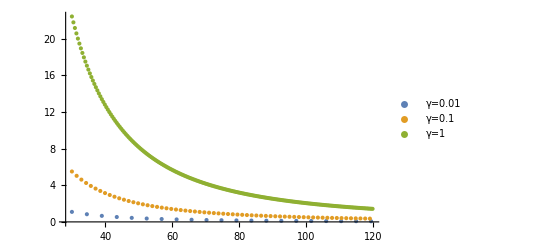

```mathematica
ListPlot[{data2[[1]][[1]],data2[[2]][[1]],data2[[3]][[1]]},PlotLegends->{"γ=0.01","γ=0.1","γ=1"}]
```

```mathematica
Export["Gm0.01.mx",data2[[1]][[1]]];
Export["Gm0.1.mx",data2[[2]][[1]]];
Export["Gm1.mx",data2[[3]][[1]]];
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Gm0.01.mx"]]]
```

```mathematica
Subscript[Gm, 0.01]=Interpolation[data2[[1]][[1]]];
Subscript[Gm, 0.1]=Interpolation[data2[[2]][[1]]];
Subscript[Gm, 1]=Interpolation[data2[[3]][[1]]];
```

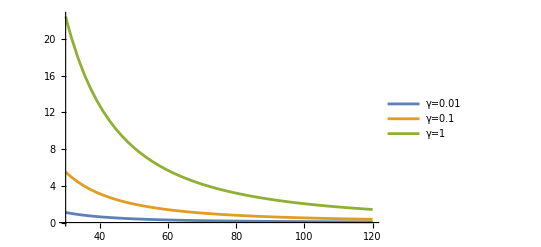

```mathematica
Plot[{Subscript[Gm, 0.01][x],Subscript[Gm, 0.1][x],Subscript[Gm, 1][x]},{x,30,120},PlotRange->All,PlotLegends->{"γ=0.01","γ=0.1","γ=1"}]
```

#### Creating Interpolating function G(R_P,γ) (need to debug)

```mathematica
Clear[γ];
Clear[Rdome];
Clear[αB];
Scap=1.0 450 (*1/2*)(*2/3*);(*Membrane midplane area of the Piezo dome in units of nm^2*)
(*αB=ArcCos[1-Scap/(2 Pi Rdome^2)]; (*Fix Piezo dome-membrane contact angle*)*)
Kb=20; (*Lipid bilayer bending rigidity in units of Subscript[k, B] T*)
(*Rdome=42;*)
(*pψfBs=-0.063;(*For γ=0.01, Rdome=42nm*)
prfBs=-0.014;*)
prfBs=-0.004671030028565507;(*For γ=0.001, Rdome=30nm*)
pψfBs=-0.013678027678573056;
(*prfBs=-0.09946183281906827;(*For γ=0.01, Rdome=30nm*)
pψfBs=-0.08481116532981327;*)
Rdome=30;
αB=ArcCos[1-Scap/(2π*Rdome^2)];

λ=(Kb/γ)^(1/2) ;(*Characteristic decay length of membrane shape deformations in units of nm*)
Lc=Rdome*Sin[αB];(*Characteristic length used to obtain dimensionless equations*)
λB=λ/Lc;          (*Scaled decay length*)
sMax=5*λB;
RdomeB=Rdome/Lc;
(*Reference values of shooting variables at γ = 0.01 k_B T/nm^2, Kb = 20 k_B T, Rdome = 41.82077878168754 nm:*)
(*pψfBs=-0.06293440963285328(*-0.063*);
prfBs=-0.013627638563264753(*-0.014*);*)
(*pψfBs=-0.063;
prfBs=-0.014;*)
Timing[
data0=Reap[For[γ=0.01,γ>=0.001,γ=γ-0.001,
(*Adjust the dimensionless shooting variables so as to satisfy boundary conditions on ψ[s] and pr[s] at s = sb:*)
sols=FindRoot[shoot[sMax,pψfBi,prfBi]=={0,0},{pψfBi,pψfBs},{prfBi,prfBs}];

(*Use the values of the shooting variables determined in one interation as initial guesses for next iteration:*)
pψfBs=pψfBi/.sols;
prfBs=prfBi/.sols;

(*dummy=Evaluate[shoot[sMax,pψfBs,prfBs]]; Print[dummy];
(*To check that we indeed have ψfB[sB] = 0 and prfB[sB] = 0 at s = sbB*)*)

(*Assemble solution using the correct values of the shooting variables:*)
ndsol=SolveShapeEqs[sMax,pψfBs,prfBs];

(*Calculate bending energy in units of Subscript[k, B] T:*)
ψff[s_]=First[ψfB[s]/.ndsol];
rff[s_]=First[rfB[s]/.ndsol];
en=Kb π rff[s]((D[ψff[s],s]+Sin[ψff[s]]/rff[s])^2+2/λB^2(1-Cos[ψff[s]])); 
Gm=NIntegrate[en,{s,s0B,sMax}];
Sow[{γ,Gm}] (*Export data*); 
]];]
(*data=data0[[2]][[1]];
Sow[{data,γ}]*)
data=data0[[2]][[1]];
```

{2.75,Null}

```mathematica
Print[data]
```

{{0.01,1.09479},{0.009,1.01155},{0.008,0.925512},{0.007,0.83626},{0.006,0.743269},{0.005,0.645826},{0.004,0.542918},{0.003,0.432988},{0.002,0.313357},{0.001,0.178283}}

#### Gm as a function of Rp and γ (Redo)

```mathematica
(*Define the ranges and increments for γ and Rp*)
gammaValues=Range[0.0001,1.1,0.005]; (*(0.0001,1.1,0.005)*)
RpValues=Range[15.02,80,1];(*(15,80,1)*)
Print[Length[gammaValues]]
Print[Length[RpValues]]
zigzagPairs=Flatten[
Table[
If[Mod[i,2]==1,(*Odd index:traverse gamma upwards*)
Transpose[{ConstantArray[RpValues[[i]],Length[gammaValues]],gammaValues}],
(*Even index:traverse gamma downwards*)
Transpose[{ConstantArray[RpValues[[i]],Length[gammaValues]],Reverse[gammaValues]}]],
{i,Length[RpValues]}
],
1];
```

220

65

```mathematica
Print[zigzagPairs]
```

```mathematica
Clear[γ];
Clear[RdomeB];
Clear[αB];
Scap=1.0 450 (*1/2*)(*2/3*);(*Membrane midplane area of the Piezo dome in units of nm^2*)
(*αB=ArcCos[1-Scap/(2 Pi Rdome^2)]; (*Fix Piezo dome-membrane contact angle*)*)
Kb=20; (*Lipid bilayer bending rigidity in units of Subscript[k, B] T*)
(*λB=λ/Lc;*)
(*prfBs=-0.004671030028565507;(*For γ=0.001, Rdome=30nm*)
pψfBs=-0.013678027678573056;*)
(*pψfBs=-0.0019242413280364649;(*For γ=0.0001, Rdome=29.920778781687574nm, Lc=λ(γ=0.0001)*)
prfBs=-0.026650095919911163*Lc/Sqrt[20/0.0001];*)
(*pψfBs=-0.0026847801542390403;(*For Rdome=15.020778781687616,γ=0.0001,Lc=λ,Scap=450*)
prfBs=-0.09438408558121254;*)
pψfBs=-0.0026847801542390403;(*For Rdome=15.020778781687616, γ=0.0001, Lc=λ, Scap=450*)
prfBs=-0.09438408558121254;
γ=0.0001;

Timing[data=Reap[For[i=1,i<=Length[zigzagPairs],i++,
If[i%50==0,Print[i],0]; (*Progress Checker*)
γ1=γ;(*Older γ*)
(*Extract the γ and Subscript[R, P] values from the sorted list of tuples*)
{Rdome,γ}=zigzagPairs[[i]];
(*RdomeB=Rdome/Lc;
sMax=5*λB;*)
λ=Sqrt[Kb/γ];
Lc=λ;
RdomeB=Rdome/Lc;
λB=Sqrt[Kb/γ]/Lc;
αB=ArcCos[1-Scap/(2π*Rdome^2)];
sMax=5*λB;

(*Adjust the dimensionless shooting variables so as to satisfy boundary conditions on ψ[s] and pr[s] at s = sb:*)
sols=FindRoot[shoot[sMax,pψfBi,prfBi]=={0,0},{pψfBi,pψfBs},{prfBi,prfBs}];

(*Use the values of the shooting variables determined in one interation as initial guesses for next iteration:*)
pψfBs=(pψfBi/.sols);
prfBs=(prfBi/.sols)*Lc/Sqrt[Kb/γ1];

(*dummy=Evaluate[shoot[sMax,pψfBs,prfBs]]; Print[dummy];
(*To check that we indeed have ψfB[sB] = 0 and prfB[sB] = 0 at s = sbB*)*)

(*Assemble solution using the correct values of the shooting variables:*)
ndsol=SolveShapeEqs[sMax,pψfBs,prfBs];

(*Calculate bending energy in units of Subscript[k, B] T:*)
ψff[s_]=First[ψfB[s]/.ndsol];
rff[s_]=First[rfB[s]/.ndsol];
en=Kb π rff[s]((D[ψff[s],s]+Sin[ψff[s]]/rff[s])^2+2/λB^2(1-Cos[ψff[s]])); 
Gm=NIntegrate[en,{s,s0B,sMax}];
Sow[{Rdome,γ,Gm}] (*Export data*); 
]];]
data1=data[[2]][[1]]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

NDSolve::ndsz: At sB == 3.9724, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {5.} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndsz: At sB == 3.9724, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {5.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndsz: At sB == 3.9724, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

$Aborted

Part::partd: Part specification data⟦2⟧ is longer than depth of object.

data

InterpolatingFunction[…]

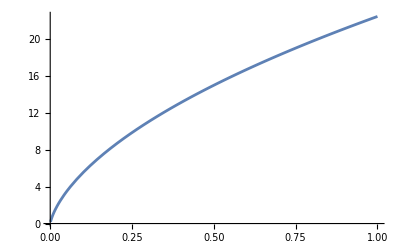

```mathematica
G=Interpolation[data1]
Plot[G[30,g],{g,0.001,1},PlotRange->All]
```

```mathematica
Export["Gm_(Rp_30_120)_(g_0.001_1).txt",data1];
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Gm_(Rp_30_120)_(g_0.001_1).txt"]]]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Gm_(Rp_30_120)_(g_0.001_1).mx"]]]
```

```mathematica
(*Now that we have Subscript[G, M] for Subscript[R, P] ϵ[30,120] and γϵ[0.001,1], we need to construct the probability function*)
```

```mathematica
Print[zigzagPairs[[510]]]
```

{33,0.475}

Now we use this data to construct the interpolating function G(Rp, gamma). This’ll allow us to construct the energy for Piezo’s closed conformation.
Another task is to solve the HCE for a flat dome, which corresponds to the open conformation. In such a limit, the initial conditions change to rfB(s0B)=√(A_P/π),

### G_M vs γ in open configuration

```mathematica
s0B=0;
SolveShapeEqs[sbB_,pψfBi_,prfBi_]:=NDSolve[
{ψfB'[sB]==1/(2 rfB[sB]) (pψfB[sB]-2 Sin[ψfB[sB]]),rfB'[sB]==Cos[ψfB[sB]],hfB'[sB]==Sin[ψfB[sB]],pψfB'[sB]==(pψfB[sB]/rfB[sB]- phfB[sB]) Cos[ψfB[sB]]+((2 rfB[sB])/λB^2+prfB[sB]) Sin[ψfB[sB]],prfB'[sB]==pψfB[sB]/(4 rfB[sB]^2)(pψfB[sB]-4 Sin[ψfB[sB]])+2/λB^2 (1-Cos[ψfB[sB]]),phfB'[sB]==0,
(*Initial conditions:*)
ψfB[s0B]==0,
rfB[s0B]==Sqrt[(Scap/Lc^2)/π],
hfB[s0B]==0,
pψfB[s0B]==pψfBi,
prfB[s0B]==prfBi,
phfB[s0B]==0
},{ψfB,rfB,hfB,pψfB,prfB,phfB},{sB,s0B,sbB}];
```

```mathematica
(*Solve the Hamilton equations in dimensionless form as a function of the shooting variables, and output the boundary values of ψfB[sB] and prfB[sB] at s = sbB (these are the boundary values used to satisfy the boundary conditions at s = sbB):*)
shoot[sbB_?NumberQ,pψfBi_?NumberQ,prfBi_?NumberQ]:=First[{ψfB[sbB],prfB[sbB]}/.SolveShapeEqs[sbB,pψfBi,prfBi]];
(*Use here ?NumberQ to indicate that sbB, pψfB0, and prfB0 are numbers; This is needed for the FindRoot[] comand (see below) to work with shoot[].*)
```

```mathematica
Scap=1.0 450 (*1/2*)(*2/3*);(*Membrane midplane area of the Piezo dome in units of nm^2*)
Kb=20; (*Lipid bilayer bending rigidity in units of Subscript[k, B] T*)
Clear[γ] (*Membrane tension in units of Subscript[k, B] T/nm^2*)
λ=(Kb/γ)^(1/2) ;(*Characteristic decay length of membrane shape deformations in units of nm*)
Lc=Sqrt[Scap];(*Characteristic length used to obtain dimensionless equations*)
λB=λ/Lc;
```

```mathematica
Clear[γ];
Clear[data];
Clear[data0];
sMax=5*λB;

(*Reference values of shooting variables at γ = 0.01 k_B T/nm^2, Kb = 20 k_B T, Rdome = 41.82077878168754 nm:*)
(*pψfBs=-0.06293440963285328(*-0.063*);
prfBs=-0.013627638563264753(*-0.014*);*)
pψfBs=-0.000000065;
prfBs=-0.0000000051;

Timing[data0=Reap[For[γ=0.001,γ<=1(*γ≤1.1*),γ=γ+0.0001(*γ+0.01*),

(*Adjust the dimensionless shooting variables so as to satisfy boundary conditions on ψ[s] and pr[s] at s = sb:*)
sols=FindRoot[shoot[sMax,pψfBi,prfBi]=={0,0},{pψfBi,pψfBs},{prfBi,prfBs}];

(*Use the values of the shooting variables determined in one interation as initial guesses for next iteration:*)
pψfBs=pψfBi/.sols;
prfBs=prfBi/.sols;

(*dummy=Evaluate[shoot[sMax,pψfBs,prfBs]]; Print[dummy];
(*To check that we indeed have ψfB[sB] = 0 and prfB[sB] = 0 at s = sbB*)*)

(*Assemble solution using the correct values of the shooting variables:*)
ndsol=SolveShapeEqs[sMax,pψfBs,prfBs];

(*Calculate bending energy in units of Subscript[k, B] T:*)
ψff[s_]=First[ψfB[s]/.ndsol];
rff[s_]=First[rfB[s]/.ndsol];
en=Kb *π *rff[s]*(D[ψff[s],s])^2; 
G=NIntegrate[en,{s,s0B,sMax}];

Sow[{γ,G}] (*Export data*); 
]];]

data=data0[[2]][[1]];
```

{102.109,Null}

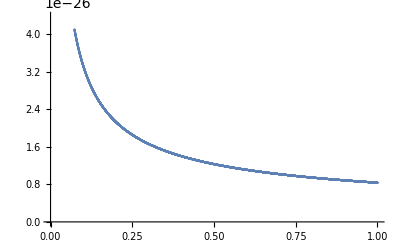

```mathematica
ListPlot[data]
```

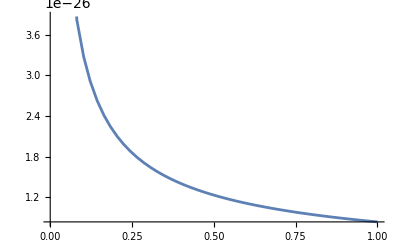

```mathematica
Subscript[Gm, open]=Interpolation[data];
Plot[Subscript[Gm, open][γ],{γ,0.001,1}]
```

## Constructing probability as a function of membrane tension

```mathematica
data1=Import["C:\\Users\\avish\\OneDrive\\Documents\\USC_PhD\\Fall 2024\\Piezo_Arclength_data\\(Rp_30_120)_(g_0.001_1)_Gm.mx"];
fig1=ListPointPlot3D[data1,AxesLabel->{"R_P","γ","G_M^Closed"}]
```

-Graphics3D-

```mathematica
Subscript[Gm, closed]=Interpolation[data1]
fig2=Plot3D[Subscript[Gm, closed][Rp,γ],{Rp,30,120},{γ,0.001,1},AxesLabel->{"R_P","γ","G_M^Closed"},PlotStyle->{Opacity[0.5]},Mesh->{0,0}]
Show[fig1,fig2,AxesLabel->{"R_P","γ","G_M^Closed"}]
```

InterpolatingFunction[…]

-Graphics3D-

-Graphics3D-

```mathematica
Subscript[K, P]=18;
Subscript[R, 0]=42;
Scap=450;
Subscript[G, closed][Rp_,γ_]:=2*Subscript[K, P]*Scap*(1/Rp-1/Subscript[R, 0])^2+Subscript[Gm, closed][Rp,γ];
Subscript[G, open][γ_]:=2*(Subscript[K, P]*Scap)/Subscript[R, 0]^2+Subscript[Gm, open][γ];
Manipulate[Plot[Subscript[G, closed][Rp,γ],{Rp,30,120},PlotRange->Full],{γ,{0.001,0.01,0.1,1},ControlType->Setter}]
(*P[Rp_,γ_]:=1/(1+Exp[Subscript[G, open][γ]-Minimize[{Subscript[G, closed][x,γ],30<=x<=Rp,0.001<=γ<=1},x][[1]]]);
P1[γ_]:=1/(1+Exp[Subscript[G, open][γ]-Subscript[Gm, closed][Subscript[R, 0],γ]]);*)
```

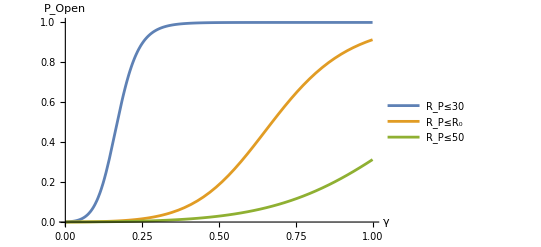

```mathematica
Plot[{P[30,γ],P[Subscript[R, 0],γ],P[50,γ]},{γ,0.001,1},AxesLabel->{"γ","P_Open"},PlotRange->All,PlotLegends->{"R_P≤30","R_P≤R_0","R_P≤50"}]
```

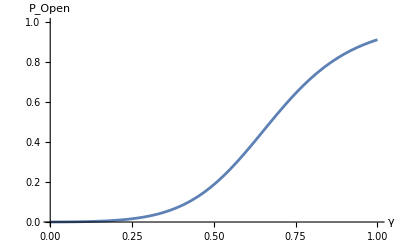

URLRead::invhttp: 
   Failed to connect to www.wolframcloud.com port 443 after 21278 ms: Couldn't
     connect to server.

CloudObjectInformation::cloudnf: No CloudObject found at the given address

First::normal: Nonatomic expression expected at position 1 in First[$Failed].

Part::pspec1: Part specification FileByteCount is not applicable.

URLFetch::invhttp: 
   A library error occurred. The raw details are: "libcurl error (28): 
    Failed to connect to www.wolframcloud.com port 443 after 21272 ms:
     Couldn't connect to server"

CloudObjectInformation::cloudnf: No CloudObject found at the given address

First::normal: Nonatomic expression expected at position 1 in First[$Failed].

Part::pspec1: Part specification FileByteCount is not applicable.

URLRead::invhttp: Send failure: Connection was aborted.

CloudObjectInformation::cloudnf: No CloudObject found at the given address

First::normal: Nonatomic expression expected at position 1 in First[$Failed].

Part::pspec1: Part specification FileByteCount is not applicable.

URLFetch::invhttp: 
   A library error occurred. The raw details are: "libcurl error (28): 
    Send failure: Connection was aborted"

CloudObjectInformation::cloudnf: No CloudObject found at the given address

First::normal: Nonatomic expression expected at position 1 in First[$Failed].

Part::pspec1: Part specification FileByteCount is not applicable.

URLRead::invhttp: Send failure: Connection was aborted.

CloudObjectInformation::cloudnf: No CloudObject found at the given address

First::normal: Nonatomic expression expected at position 1 in First[$Failed].

Part::pspec1: Part specification FileByteCount is not applicable.

URLFetch::invhttp: 
   A library error occurred. The raw details are: "libcurl error (28): 
    Send failure: Connection was aborted"

CloudObjectInformation::cloudnf: No CloudObject found at the given address

First::normal: Nonatomic expression expected at position 1 in First[$Failed].

Part::pspec1: Part specification FileByteCount is not applicable.

```mathematica
Plot[P1[γ],{γ,0.001,1},AxesLabel->{"γ","P_Open"},PlotRange->{All,{0,1}}]
```